```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/AuctionExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
randommm = Take[q, {1, Length[q], 100}];
lrandommm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{7120.,6532.,7636.,6707.,6701.,9813.,6665.,5452.,6778.,9196.,7632.,7973.,5965.,8959.,9580.,4301.,7774.,9131.,6078.,5192.,7353.,10191.,7385.,7577.,6271.,9532.,5585.,6665.,8011.,5179.,6748.,8750.,7377.,7003.,6171.,8421.,4964.,8035.,6829.,7197.,8835.,7394.,8992.,5974.,7595.,4479.,8003.,5444.,7083.,5767.,6696.,6475.,7304.,5323.,8132.,10256.,5593.,9840.,8813.,6349.,4006.,9225.,7178.,8789.,6290.,6346.,5685.,7831.,6701.,8161.,7582.,5767.,8781.,10225.,7901.,9383.,8523.,7478.,6756.,7621.,5724.,6032.,6970.,6440.,7852.,6122.,5382.,6881.,8996.,10269.,5032.,6405.,8476.,7309.,8475.,5658.,5370.,5875.,7977.,6537.}

{6004.,5980.,5349.,4492.,4946.,4706.,5058.,4283.,3896.,5047.,5264.,5395.,5144.,4548.,4535.,5634.,3721.,4673.,4544.,4137.,5016.,5125.,3911.,4413.,4250.,7462.,4533.,4896.,3941.,4686.,4527.,5303.,4333.,4569.,6263.,5280.,6061.,3931.,6361.,5462.,3836.,4983.,5168.,4646.,6250.,4129.,5251.,5504.,5882.,4592.,5700.,4444.,4318.,4674.,4794.,4233.,4658.,4201.,4518.,4699.,4354.,4443.,4687.,6109.,4941.,4514.,4120.,4539.,6760.,4095.,4886.,4068.,4936.,5877.,3800.,4998.,5084.,3696.,5119.,4096.,3701.,6023.,5801.,4073.,4825.,5074.,4546.,3695.,5743.,5744.,4961.,4995.,5088.,4942.,3862.,4377.,5409.,5215.,5066.,5967.}

{4954.,4850.,5694.,3960.,5890.,4639.,4685.,4109.,4186.,4167.,3980.,3881.,5267.,4889.,5259.,4026.,4976.,4759.,4719.,5178.,5469.,4423.,4997.,5265.,5875.,4227.,4752.,4558.,5373.,4587.,4672.,7389.,4287.,4668.,7959.,4493.,4805.,5720.,4322.,3745.,6673.,4414.,3997.,5070.,5725.,6800.,5354.,5830.,5028.,4932.,4763.,5996.,6427.,4748.,4430.,4805.,5134.,6514.,5544.,5230.,7866.,5670.,6754.,4112.,4083.,4172.,4533.,5170.,4849.,5566.,6625.,5875.,3870.,4754.,4568.,5290.,4170.,5131.,5387.,5956.,8147.,5004.,4753.,7294.,4965.,4765.,6455.,4871.,6161.,4178.,6051.,4780.,5526.,5523.,6874.,4411.,5232.,3944.,5455.,3804.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{5965.,4127.,5241.,5055.,5018.,4658.,5380.,5369.,6829.,7408.,5283.,4863.,5010.,4926.,7271.,5567.,8340.,7122.,6240.,6555.,6591.,6942.,5970.,6351.,4469.,7092.,7185.,4817.,6843.,5059.,8156.,7392.,5960.,7684.,4581.,4650.,5923.,6227.,4910.,4827.,4717.,7508.,9125.,5658.,5985.,3910.,5168.,4791.,5870.,6034.,7570.,6226.,5033.,7406.,7882.,7020.,6301.,5945.,5213.,5781.,10171.,11837.,8311.,5867.,7370.,4933.,8235.,9529.,5925.,4598.,7929.,5434.,5293.,8437.,6224.,10777.,4166.,6544.,9436.,4843.,9223.,4779.,5562.,5300.,5482.,7554.,5445.,5862.,6479.,6671.,6589.,5075.,5549.,4798.,5409.,6284.,8823.,5096.,5234.,6501.}

{12019.,9572.,5516.,6240.,6758.,6277.,6589.,6784.,5139.,4422.,9932.,6243.,6090.,4819.,5441.,11588.,8758.,9886.,10614.,10724.,6121.,7724.,7129.,5975.,8417.,6330.,5627.,7083.,6216.,6295.,5461.,7510.,5726.,8899.,4571.,10994.,8010.,7697.,9970.,7345.,5517.,6320.,10188.,7904.,7901.,7736.,6017.,5852.,5644.,9837.,7326.,4408.,5020.,5522.,5996.,5807.,6431.,6091.,6545.,7451.,7612.,5230.,5199.,7720.,5362.,9479.,5650.,5576.,7781.,7673.,5540.,4570.,4951.,9070.,7732.,7529.,5624.,10322.,5995.,11088.,6997.,8542.,7043.,6517.,6018.,6468.,7552.,9129.,9034.,6173.,8031.,7326.,5422.,11642.,10208.,7567.,4456.,5165.,5265.,6401.}

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{5626.,4785.,4592.,4482.,6544.,5372.,5787.,4310.,6539.,4642.,6736.,6059.,4832.,4454.,6997.,4388.,5531.,4439.,4542.,7212.,7408.,5918.,5118.,5814.,8677.,5627.,5773.,6056.,4758.,6403.,5244.,5371.,4092.,5844.,5413.,6248.,6474.,5129.,5946.,4467.,5161.,3954.,4415.,4989.,3910.,4872.,6571.,5275.,6048.,5930.,5053.,4294.,5979.,5012.,5660.,5052.,5172.,4544.,5974.,5343.,7265.,4837.,4621.,4065.,5975.,4446.,8786.,4319.,7292.,3950.,5853.,5209.,5102.,5962.,7809.,5364.,5498.,4671.,5362.,6820.,5171.,5257.,5222.,4604.,4652.,4875.,4820.,6135.,5064.,5077.,4411.,4998.,5824.,5783.,3660.,4864.,5085.,5338.,4627.,7084.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,7120.},{1,6532.},{1,7636.},{1,6707.},{1,6701.},{1,9813.},{1,6665.},{1,5452.},{1,6778.},{1,9196.},{1,7632.},{1,7973.},{1,5965.},{1,8959.},{1,9580.},{1,4301.},{1,7774.},{1,9131.},{1,6078.},{1,5192.},{1,7353.},{1,10191.},{1,7385.},{1,7577.},{1,6271.},{1,9532.},{1,5585.},{1,6665.},{1,8011.},{1,5179.},{1,6748.},{1,8750.},{1,7377.},{1,7003.},{1,6171.},{1,8421.},{1,4964.},{1,8035.},{1,6829.},{1,7197.},{1,8835.},{1,7394.},{1,8992.},{1,5974.},{1,7595.},{1,4479.},{1,8003.},{1,5444.},{1,7083.},{1,5767.},{1,6696.},{1,6475.},{1,7304.},{1,5323.},{1,8132.},{1,10256.},{1,5593.},{1,9840.},{1,8813.},{1,6349.},{1,4006.},{1,9225.},{1,7178.},{1,8789.},{1,6290.},{1,6346.},{1,5685.},{1,7831.},{1,6701.},{1,8161.},{1,7582.},{1,5767.},{1,8781.},{1,10225.},{1,7901.},{1,9383.},{1,8523.},{1,7478.},{1,6756.},{1,7621.},{1,5724.},{1,6032.},{1,6970.},{1,6440.},{1,7852.},{1,6122.},{1,5382.},{1,6881.},{1,8996.},{1,10269.},{1,5032.},{1,6405.},{1,8476.},{1,7309.},{1,8475.},{1,5658.},{1,5370.},{1,5875.},{1,7977.},{1,6537.}}

{{2,6004.},{2,5980.},{2,5349.},{2,4492.},{2,4946.},{2,4706.},{2,5058.},{2,4283.},{2,3896.},{2,5047.},{2,5264.},{2,5395.},{2,5144.},{2,4548.},{2,4535.},{2,5634.},{2,3721.},{2,4673.},{2,4544.},{2,4137.},{2,5016.},{2,5125.},{2,3911.},{2,4413.},{2,4250.},{2,7462.},{2,4533.},{2,4896.},{2,3941.},{2,4686.},{2,4527.},{2,5303.},{2,4333.},{2,4569.},{2,6263.},{2,5280.},{2,6061.},{2,3931.},{2,6361.},{2,5462.},{2,3836.},{2,4983.},{2,5168.},{2,4646.},{2,6250.},{2,4129.},{2,5251.},{2,5504.},{2,5882.},{2,4592.},{2,5700.},{2,4444.},{2,4318.},{2,4674.},{2,4794.},{2,4233.},{2,4658.},{2,4201.},{2,4518.},{2,4699.},{2,4354.},{2,4443.},{2,4687.},{2,6109.},{2,4941.},{2,4514.},{2,4120.},{2,4539.},{2,6760.},{2,4095.},{2,4886.},{2,4068.},{2,4936.},{2,5877.},{2,3800.},{2,4998.},{2,5084.},{2,3696.},{2,5119.},{2,4096.},{2,3701.},{2,6023.},{2,5801.},{2,4073.},{2,4825.},{2,5074.},{2,4546.},{2,3695.},{2,5743.},{2,5744.},{2,4961.},{2,4995.},{2,5088.},{2,4942.},{2,3862.},{2,4377.},{2,5409.},{2,5215.},{2,5066.},{2,5967.}}

{{3,4954.},{3,4850.},{3,5694.},{3,3960.},{3,5890.},{3,4639.},{3,4685.},{3,4109.},{3,4186.},{3,4167.},{3,3980.},{3,3881.},{3,5267.},{3,4889.},{3,5259.},{3,4026.},{3,4976.},{3,4759.},{3,4719.},{3,5178.},{3,5469.},{3,4423.},{3,4997.},{3,5265.},{3,5875.},{3,4227.},{3,4752.},{3,4558.},{3,5373.},{3,4587.},{3,4672.},{3,7389.},{3,4287.},{3,4668.},{3,7959.},{3,4493.},{3,4805.},{3,5720.},{3,4322.},{3,3745.},{3,6673.},{3,4414.},{3,3997.},{3,5070.},{3,5725.},{3,6800.},{3,5354.},{3,5830.},{3,5028.},{3,4932.},{3,4763.},{3,5996.},{3,6427.},{3,4748.},{3,4430.},{3,4805.},{3,5134.},{3,6514.},{3,5544.},{3,5230.},{3,7866.},{3,5670.},{3,6754.},{3,4112.},{3,4083.},{3,4172.},{3,4533.},{3,5170.},{3,4849.},{3,5566.},{3,6625.},{3,5875.},{3,3870.},{3,4754.},{3,4568.},{3,5290.},{3,4170.},{3,5131.},{3,5387.},{3,5956.},{3,8147.},{3,5004.},{3,4753.},{3,7294.},{3,4965.},{3,4765.},{3,6455.},{3,4871.},{3,6161.},{3,4178.},{3,6051.},{3,4780.},{3,5526.},{3,5523.},{3,6874.},{3,4411.},{3,5232.},{3,3944.},{3,5455.},{3,3804.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,5965.},{7,4127.},{7,5241.},{7,5055.},{7,5018.},{7,4658.},{7,5380.},{7,5369.},{7,6829.},{7,7408.},{7,5283.},{7,4863.},{7,5010.},{7,4926.},{7,7271.},{7,5567.},{7,8340.},{7,7122.},{7,6240.},{7,6555.},{7,6591.},{7,6942.},{7,5970.},{7,6351.},{7,4469.},{7,7092.},{7,7185.},{7,4817.},{7,6843.},{7,5059.},{7,8156.},{7,7392.},{7,5960.},{7,7684.},{7,4581.},{7,4650.},{7,5923.},{7,6227.},{7,4910.},{7,4827.},{7,4717.},{7,7508.},{7,9125.},{7,5658.},{7,5985.},{7,3910.},{7,5168.},{7,4791.},{7,5870.},{7,6034.},{7,7570.},{7,6226.},{7,5033.},{7,7406.},{7,7882.},{7,7020.},{7,6301.},{7,5945.},{7,5213.},{7,5781.},{7,10171.},{7,11837.},{7,8311.},{7,5867.},{7,7370.},{7,4933.},{7,8235.},{7,9529.},{7,5925.},{7,4598.},{7,7929.},{7,5434.},{7,5293.},{7,8437.},{7,6224.},{7,10777.},{7,4166.},{7,6544.},{7,9436.},{7,4843.},{7,9223.},{7,4779.},{7,5562.},{7,5300.},{7,5482.},{7,7554.},{7,5445.},{7,5862.},{7,6479.},{7,6671.},{7,6589.},{7,5075.},{7,5549.},{7,4798.},{7,5409.},{7,6284.},{7,8823.},{7,5096.},{7,5234.},{7,6501.}}

{{8,12019.},{8,9572.},{8,5516.},{8,6240.},{8,6758.},{8,6277.},{8,6589.},{8,6784.},{8,5139.},{8,4422.},{8,9932.},{8,6243.},{8,6090.},{8,4819.},{8,5441.},{8,11588.},{8,8758.},{8,9886.},{8,10614.},{8,10724.},{8,6121.},{8,7724.},{8,7129.},{8,5975.},{8,8417.},{8,6330.},{8,5627.},{8,7083.},{8,6216.},{8,6295.},{8,5461.},{8,7510.},{8,5726.},{8,8899.},{8,4571.},{8,10994.},{8,8010.},{8,7697.},{8,9970.},{8,7345.},{8,5517.},{8,6320.},{8,10188.},{8,7904.},{8,7901.},{8,7736.},{8,6017.},{8,5852.},{8,5644.},{8,9837.},{8,7326.},{8,4408.},{8,5020.},{8,5522.},{8,5996.},{8,5807.},{8,6431.},{8,6091.},{8,6545.},{8,7451.},{8,7612.},{8,5230.},{8,5199.},{8,7720.},{8,5362.},{8,9479.},{8,5650.},{8,5576.},{8,7781.},{8,7673.},{8,5540.},{8,4570.},{8,4951.},{8,9070.},{8,7732.},{8,7529.},{8,5624.},{8,10322.},{8,5995.},{8,11088.},{8,6997.},{8,8542.},{8,7043.},{8,6517.},{8,6018.},{8,6468.},{8,7552.},{8,9129.},{8,9034.},{8,6173.},{8,8031.},{8,7326.},{8,5422.},{8,11642.},{8,10208.},{8,7567.},{8,4456.},{8,5165.},{8,5265.},{8,6401.}}

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,5626.},{10,4785.},{10,4592.},{10,4482.},{10,6544.},{10,5372.},{10,5787.},{10,4310.},{10,6539.},{10,4642.},{10,6736.},{10,6059.},{10,4832.},{10,4454.},{10,6997.},{10,4388.},{10,5531.},{10,4439.},{10,4542.},{10,7212.},{10,7408.},{10,5918.},{10,5118.},{10,5814.},{10,8677.},{10,5627.},{10,5773.},{10,6056.},{10,4758.},{10,6403.},{10,5244.},{10,5371.},{10,4092.},{10,5844.},{10,5413.},{10,6248.},{10,6474.},{10,5129.},{10,5946.},{10,4467.},{10,5161.},{10,3954.},{10,4415.},{10,4989.},{10,3910.},{10,4872.},{10,6571.},{10,5275.},{10,6048.},{10,5930.},{10,5053.},{10,4294.},{10,5979.},{10,5012.},{10,5660.},{10,5052.},{10,5172.},{10,4544.},{10,5974.},{10,5343.},{10,7265.},{10,4837.},{10,4621.},{10,4065.},{10,5975.},{10,4446.},{10,8786.},{10,4319.},{10,7292.},{10,3950.},{10,5853.},{10,5209.},{10,5102.},{10,5962.},{10,7809.},{10,5364.},{10,5498.},{10,4671.},{10,5362.},{10,6820.},{10,5171.},{10,5257.},{10,5222.},{10,4604.},{10,4652.},{10,4875.},{10,4820.},{10,6135.},{10,5064.},{10,5077.},{10,4411.},{10,4998.},{10,5824.},{10,5783.},{10,3660.},{10,4864.},{10,5085.},{10,5338.},{10,4627.},{10,7084.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem,alrandommm], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 5 | 5.18816×10^8 | 1.03763×10^8 | 60.0923 | 1.2096×10^-50
Error | 594 | 1.02568×10^9 | 1.72673×10^6 |  | 
Total | 599 | 1.54449×10^9 |  |  | ,CellMeans→All | 6021.18
Model[1] | 7227.87
Model[2] | 4883.88
Model[3] | 5156.62
Model[7] | 6285.73
Model[8] | 7146.83
Model[10] | 5426.14,PostTests→{Model→Tukey | {{1,2},{1,3},{1,7},{2,7},{3,7},{2,8},{3,8},{7,8},{1,10},{2,10},{7,10},{8,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.6,3638.14,4455.56,4688.42,4671.17,4809.63,5055.87,5224.04,5497.82,5840.27,5982.44,6107.79,6186.04,6108.39,6092.23,5953.91,5695.41,5633.79,5735.31,5866.49,6122.88,6301.32,6174.85,6048.6,6052.16,6165.35,6363.32,6514.75,6682.21,6675.68,6664.9,6743.09,6694.84,6823.13,6835.29,6922.63,6828.23,6967.85,6875.23,6889.37,6886.84,6893.76,6866.23,6835.08,6813.29,6837.1,6830.44,6648.26,6681.35,6597.34,6607.1,6420.54,6404.55,6416.63,6527.12,6709.87,6729.26,6734.47,6662.94,6555.46,6627.83,6516.16,6497.36,6382.01,6319.72,6279.61,6106.,6077.12,6046.61,6189.12,6266.9,6457.87,6518.59,6400.29,6293.07,6250.24,6078.88,5843.71,5859.55,5921.03,5879.67,5933.72,6058.19,5947.53,5930.61,5808.39,5745.3,5845.01,5952.28,5944.19,6059.95,6016.27,5952.06,5924.95,5888.43,5986.36,6191.96,6233.13,6157.45,5975.07,5879.13,5925.32,5915.67,5840.85,5849.01,5879.69,5936.28,5682.6,5616.49,5722.76,5783.37,5833.87,5839.1,5813.38,5773.52,5751.26,5711.64,5717.3,5765.95,5812.93,5702.65,5732.49,5780.94,5742.6,5905.73,6071.84,6139.24,6050.04,5914.96,5917.21,5868.48,5778.36,5620.37,5745.9,5891.65,6086.86,6094.13,6059.56,5944.26,5774.14,5761.5,5760.57,5660.77,5706.31,5709.13,5758.07,5583.73,5764.72,5913.53,5902.53,5932.51,5977.12,5853.35,5795.95,5935.58,5952.03,5806.81,5782.42,5683.1,5598.11,5589.87,5755.11,5935.03,5958.69,6018.29,6055.09,5942.43,5794.62,5703.12,5709.12,5876.51,5878.19,5658.62,5503.36,5483.41,5535.2,5578.44,5701.27,5788.7,5933.13,6007.04,5844.35,5778.72,5694.13,5558.93,5687.42,5795.3,6025.36,5959.47,5978.78,5981.6,5976.45,5909.62,5847.64,5828.65,5869.24,5864.93,5717.65,5587.57,5653.83,5796.87,5674.02,5646.78,5580.38,5520.44,5553.77,5587.71,5697.36,5756.92,5659.11,5736.64,5739.12,5807.5,5901.39,5961.45,5925.58,5841.78,5795.51,5918.64,5979.77,5936.44,5733.59,5648.26,5571.87,5533.21,5670.61,5669.29,5609.59,5568.18,5642.7,5849.55,5853.74,5906.94,5792.72,5829.83,5949.62,5898.54,6027.92,6032.37,5972.9,5992.1,5921.22,5967.47,5999.95,6063.03,6100.76,6117.23,5968.62,5825.45,5741.26,5696.43,5668.38,5646.46,5656.68,5858.21,5834.47,5737.47,5773.47,5775.61,5561.95,5581.66,5654.47,5633.03,5683.16,5645.99,5643.56,5648.34,5672.6,5830.65,5785.94,5772.7,5750.12,5704.3,5701.16,5788.34,5701.78,5667.48,5760.18,5795.67,5766.46,5833.58,5766.61,5864.77,5967.19,5970.13,5905.49,5618.2,5618.48,5575.2,5606.2,5610.71,5646.03,5753.78,5719.12,5811.72,5952.16,6024.51,5974.02,5970.3,5912.55,5789.57,5641.91,5455.35,5551.25,5557.67,5694.26,5792.67,5835.08,5752.38,5776.34,5886.77,5961.1,5973.37,5927.66,5847.17,5896.55,5898.19,5985.98,6038.96,6013.04,6009.84,6037.07,5948.81,5944.86,5972.08,6146.51,6298.91,6268.51,6210.34,6179.15,6171.96,6205.33,6028.42,5854.04,5814.53,5800.03,5733.81,5762.5,5835.1,6047.09,6127.16,6188.82,6105.25,5929.58,5881.56,5889.23,5918.02,5893.29,5899.74,5883.71,6049.75,6055.99,5997.86,6055.47,6191.92,6224.21,6204.02,6316.93,6182.93,6133.67,5943.06,5820.67,5738.83,5647.02,5809.76,5956.59,6062.03,5999.16,6007.76,5854.58,5908.24,5951.42,5996.7,6002.27,5987.6,5932.89,5750.33,5800.67,5932.57,5998.41,6021.64,5953.91,5901.37,5812.24,5785.63,5960.01,6092.6,6271.82,6194.26,6203.1,6187.57,6158.17,6369.79,6486.98,6416.49,6367.81,6157.38,6090.89,6020.27,5890.98,6022.61,5973.62,6049.45,6219.58,6053.89,6078.99,5970.77,6065.89,6086.07,5991.92,5872.65,5886.98,6037.99,6185.93,6247.32,6273.58,6187.43,6223.24,6060.24,5910.72,5853.59,5811.57,5849.09,5834.,6037.06,6128.13,6107.41,6032.2,6069.15,6157.8,6090.07,6120.65,6094.78,6089.04,6108.28,6171.4,6214.55,6204.04,6316.52,6306.81,6268.16,6219.2,6094.1,6189.03,6129.4,6019.55,6051.75,5896.77,5767.68,5789.7,5777.95,5744.01,5736.36,5760.79,5951.66,5952.44,5950.93,6021.63,6144.25,6095.84,5951.17,5874.82,5984.85,6143.42,6191.7,6148.97,6053.38,6016.49,5886.7,6086.53,6082.92,6101.96,5927.92,5924.05,6007.63,6029.74,5868.11,5990.47,6088.14,6151.02,6233.19,6405.44,6251.27,6288.61,6304.48,6239.3,6245.21,6255.32,6174.84,6174.04,6147.04,6251.53,6322.74,6279.79,6370.33,6405.94,6323.18,6278.79,6260.42,6359.28,6444.69,6440.04,6415.63,6460.25,6408.96,6374.73,6271.82,6230.41,6286.94,6339.39,6395.4,6320.72,6116.1,6095.61,6047.43,6036.67,6126.16,6205.98,6255.18,6162.06,6371.1,6379.28,6419.36,6503.7,6374.89,6251.09,6094.16,6169.67,6312.5,6273.46,6372.15,6232.79,6029.09,6029.99,6182.18,6175.43,6259.22,6351.11,6401.,6398.7,6325.83,6306.31,6301.7,6122.79,6161.08,6265.33,6345.79,6372.2,6232.13,6116.45,6260.85,6332.09,6384.14,6245.53,6319.72,6286.25,6323.86,6204.66,6340.92,6366.78,6282.26,6237.08,6369.8,6216.54,6196.66,6179.32,6232.2,6196.27,6315.61,6269.98,6145.51,5972.31,6127.59,6097.09,6272.89,6475.15,6497.42,6396.94,6502.42,6367.97,6502.32,6439.92,6374.67,6354.41,6228.29,6032.94,6161.19,6121.28,6280.07,6265.29,6250.59,6207.13,6338.46,6318.75,6346.5,6387.45,6433.06,6267.82,6298.84,6293.67,6211.29,6169.32,6160.94,6216.82,6347.65,6275.87,6174.32,6007.66,6040.03,6093.96,6232.33,6301.01,6322.76,6286.23,6158.32,6038.94,5934.04,5892.35,5850.68,6010.82,6099.24,6192.49,6252.55,6125.49,6007.53,5982.91,6130.75,6234.79,6233.24,6199.46,6256.16,6152.1,6128.17,6145.79,6099.5,6040.68,6204.36,6430.77,6463.12,6502.26,6564.07,6404.35,6369.7,6335.29,6264.,6312.37,6195.59,6369.3,6524.47,6426.17,6319.17,6367.44,6251.75,6284.19,6071.14,6035.74,6042.95,6078.84,6030.84,6150.42,6094.41,6052.64,5919.97,6188.47,6495.25,6665.58,6552.52,6394.04,6331.25,6161.46,6177.74,6251.41,6365.88,6343.09,6248.75,6205.01,6195.74,6236.98,6285.47,6328.47,6368.24,6383.44,6344.45,6429.13,6321.96,6324.87,6393.34,6302.27,6250.05,6211.79,6213.71,6279.62,6389.51,6456.22,6622.4,6460.89,6241.96,6206.69,6170.99,6088.79,6045.95,6260.26,6401.71,6365.2,6453.89,6333.63,6251.98,6278.22,6312.72,6379.84,6360.11,6313.,6205.66,6081.02,6129.16,6155.52,6040.06,6020.17,6057.81,6253.61,6306.96,6261.83,6205.66,6128.8,6122.13,6222.83,6319.62,6280.62,6186.37,6289.35,6290.7,6411.66,6523.42,6479.33,6353.9,6234.22,6322.54,6480.41,6428.35,6412.44,6498.07,6448.,6465.7,6258.77,6096.6,6110.83,6149.25,6170.46,6179.45,6186.16,6253.57,6303.3,6513.55,6624.63,6543.09,6415.81,6391.51,6305.05,6364.64,6421.87,6368.31,6307.64,6347.6,6351.48,6432.07,6457.07,6463.89,6505.52,6298.19,6357.46,6322.92,6406.75,6472.21,6471.81,6369.04,6379.47,6343.24,6349.58,6543.81,6463.64,6386.31,6427.55,6563.18,6692.1,6751.1,6715.58,6488.92,6432.48,6388.67,6460.41,6567.25,6370.49,6315.47,6304.67,6410.64,6405.6,6440.92,6306.9,6383.29,6580.54,6593.13,6672.33,6697.2,6718.37,6743.43,6732.06,6799.69,6569.66,6410.96,6331.51,6311.03,6410.91,6353.42,6287.16,6250.99,6430.4,6464.05,6445.68,6275.53,6374.53,6420.26,6347.66,6299.2,6158.41,6167.41,6154.34,6172.92,6181.27,6045.01,6154.7,6339.88,6484.57,6377.88,6356.09,6453.56,6614.32,6637.38,6588.67,6420.92,6274.23,6269.23,6356.6,6450.06,6538.4,6594.64,6592.01,6628.2,6485.06,6547.96,6603.9,6647.83,6629.32,6579.66,6659.34,6596.07,6481.85,6630.34,6576.99,6542.08,6434.03,6416.91,6504.99,6536.15,6458.98,6546.99,6528.07,6542.76,6504.06,6564.1,6554.19,6482.95,6369.33,6418.08,6326.27,6363.54,6368.35,6396.08,6437.67,6419.85,6571.95,6609.98,6676.67,6522.82,6607.48,6680.39,6662.29,6712.46,6734.31,6643.67,6579.78,6586.62,6443.64,6480.69,6524.97,6597.88,6756.53,6749.12,6680.41,6562.15,6686.72,6729.29,6686.19,6577.48,6560.67,6440.09,6482.82,6542.89,6554.11,6482.39,6523.64,6492.25,6439.5,6432.9,6394.33,6475.88,6491.19,6495.66,6672.92,6678.75,6557.58,6595.82,6595.36,6487.64,6270.13,6309.43,6349.82,6392.16,6480.99,6481.,6350.03,6350.44,6546.83,6573.08,6510.72,6394.85,6312.85,6367.08,6502.87,6710.69,6706.21,6580.82,6597.57,6602.43,6589.35,6597.9,6582.86,6658.81,6677.57,6690.29,6762.68,6854.92,6899.21,6901.64,6869.58,6718.94,6613.97,6683.2,6596.74,6561.61,6600.09,6744.85,6703.42,6753.77,6837.64,6883.24,6831.77,6740.6,6624.66,6518.54,6573.,6808.58,7066.05,7050.74,6959.66,6964.54,7052.03,7088.22,6910.4,6820.52,6817.16,6685.5,6606.06,6727.15,6717.94,6709.5,6611.29,6576.62,6438.06,6497.74,6546.11,6598.49,6592.,6690.35,6685.82,6606.45,6485.23,6352.39,6318.09,6410.32,6495.18,6496.19,6665.72,6574.44,6533.65,6446.35,6450.53,6515.52,6676.73,6622.08,6699.61,6704.81,6558.68,6494.08,6510.76,6560.47,6565.09,6608.24,6701.69,6816.33,6750.27,6475.8,6360.78,6326.58,6162.35,6150.13,6130.8,6159.88,6299.11,6464.41,6423.8,6501.61,6536.67,6654.45,6777.9,6964.76,6851.42,6782.06,6699.79,6510.03,6530.41,6456.71,6331.52,6333.81,6517.96,6664.01,6660.46,6761.04,6960.28,7005.47,6972.98,6851.02,6796.96,6812.16,6822.1,6850.53,6819.89,6772.07,6731.66,6673.49,6643.88,6612.79,6530.27,6677.76,6523.8,6496.51,6565.37,6613.14,6595.6,6688.61,6568.18,6476.,6377.51,6435.19,6493.5,6545.57,6608.12,6640.63,6765.95,6860.52,6730.18,6682.54,6584.82,6640.29,6588.66,6600.57,6567.75,6551.2,6486.34,6328.89,6380.43,6496.7,6599.66,6663.88,6770.93,6808.16,6765.27,6720.45,6685.81,6760.55,6799.19,6623.83,6685.42,6853.48,6931.12,6891.06,6844.58,6675.9,6614.43,6744.01,6894.13,6850.7,6802.53,6661.44,6517.78,6353.02,6286.74,6343.87,6467.14,6563.33,6694.34,6728.3,6778.68,6735.74,6850.37,6905.22,6692.64,6504.8,6491.4,6455.43,6431.81,6446.12,6586.01,6670.63,6707.21,6638.08,6815.5,6710.91,6686.85,6663.93,6544.42,6657.79,6684.31,6539.75,6681.22,6808.29,6743.26,6938.13,6902.42,6834.89,6793.27,6796.12,6781.66,6936.44,7079.11,7111.68,7068.22,7053.62,6915.68,6821.37,6697.82,6642.83,6608.77,6594.83,6598.26,6463.32,6569.26,6814.38,6875.17,6955.67,6821.89,6705.56,6630.87,6584.05,6648.38,6703.18,6681.97,6604.76,6731.48,6832.05,6846.65,6727.67,6876.39,6854.03,6699.75,6588.07,6614.8,6693.62,6744.89,6781.83,6967.77,6966.91,6850.54,6910.18,6745.06,6651.7,6581.64,6560.98,6628.92,6697.45,6604.9,6595.1,6733.12,6643.93,6753.32,6817.44,6888.04,6795.46,6795.7,6723.88,6544.31,6623.82,6564.54,6545.95,6701.18,6662.61,6645.38,6573.68,6497.75,6494.98,6722.01,6912.15,6884.08,6790.51,6712.66,6799.02,6879.3,6810.44,6768.48,6742.8,6754.9,6605.7,6716.28,6678.86,6635.98,6641.22,6534.72,6467.31,6688.89,6767.08,6674.93,6702.29,6779.89,6873.58,6812.09,6774.28,6723.94,6606.66,6487.11,6620.1,6768.66,6861.05,6833.14,6737.45,6611.23,6550.04,6714.79,6798.57,6884.44,6907.77,6722.32,6555.84,6498.02,6638.51,6676.15,6693.23,6754.96,6807.29,6683.78,6801.16,6750.57,6876.81,6844.72,6838.06,6717.3,6595.79,6545.63,6562.67,6580.04,6581.71,6429.92,6442.31,6671.12,6712.76,6716.18,6655.7,6593.48,6484.9,6431.67,6488.6,6573.63,6620.77,6696.92,6799.27,6782.64,6896.33,6916.65,6850.68,6929.65,6902.12,6725.48,6736.4,6849.28,6892.33,6890.38,6703.23,6730.23,6760.96,6881.89,6892.49,6606.8,6589.79,6673.19,6642.69,6560.5,6569.91,6486.27,6501.29,6496.64,6544.86,6452.43,6474.46,6522.11,6503.93,6616.79,6704.33,6888.28,6909.87,6885.35,6996.79,6981.32,6893.57,6772.53,6750.16,6733.28,6699.21,6839.56,6855.79,6968.46,6965.65,6854.83,6762.68,6844.89,6718.77,6621.64,6659.45,6823.55,6820.83,6785.35,6764.22,6631.12,6637.92,6618.49,6619.69,6734.75,6828.34,6915.64,6920.54,6730.01,6614.72,6570.81,6423.25,6501.56,6542.36,6569.12,6685.76,6704.69,6789.48,6823.05,6895.26,6888.84,6887.38,6777.28,6869.94,6766.65,6782.61,6709.2,6761.78,6919.07,7068.27,7208.68,7182.95,6973.37,6960.31,6922.5,6787.53,6872.05,6900.83,7009.39,6923.51,6903.8,6894.32,6883.35,6921.17,6985.19,6870.27,6790.41,6775.05,6744.15,6678.68,6815.49,6863.47,6806.71,6931.59,6868.59,6679.42,6728.81,6697.41,6793.83,6830.23,6635.05,6582.71,6629.53,6681.81,6520.95,6588.72,6600.92,6734.71,6759.24,6831.94,6855.29,6891.44,6901.3,6822.58,6772.47,6729.53,6648.95,6542.21,6661.43,6906.82,6969.54,6845.94,6783.62,6691.89,6556.83,6460.88,6475.6,6249.09,6322.19,6506.28,6523.37,6603.56,6511.4,6535.88,6734.5,6795.92,6561.26,6658.12,6762.48,6654.72,6776.8,6833.38,6834.71,6719.83,6683.33,6792.29,6934.16,6743.04,6781.4,6660.46,6692.78,6708.4,6792.51,6867.01,6954.36,7111.68,7066.59,6974.3,6954.52,6921.94,6879.71,6916.76,6884.44,6954.77,7028.19,6991.23,6907.91,6830.78,6939.04,7056.71,7080.8,7011.33,6995.27,6947.79,6764.46,6699.13,6508.11,6408.18,6634.39,6762.49,6881.69,6852.11,6859.71,6873.69,6851.64,6949.23,7112.61,7178.1,7257.72,7185.24,7033.72,7001.77,7087.93,6924.27,6907.77,6895.63,7120.16,7143.8,7101.46,7024.77,6838.08,6790.5,6712.22,6638.43,6681.63,6618.66,6647.17,6574.59,6648.55,6813.96,6867.47,6904.7,6873.15,6873.76,7031.96,7097.15,7157.06,7174.14,6977.77,6695.64,6609.44,6412.15,6587.66,6796.17,6939.91,6862.92,6761.97,6649.46,6573.08,6524.78,6417.53,6288.87,6434.9,6466.24,6488.23,6570.29,6714.38,6738.29,6571.4,6565.77,6556.17,6708.46,6698.58,6688.2,6741.87,6540.03,6481.68,6415.33,6476.8,6603.33,6633.39,6640.92,6612.32,6672.78,6791.44,6821.93,6713.07,6721.91,6772.33,6759.64,6718.33,6550.64,6601.82,6645.42,6647.77,6661.8,6713.32,6694.1,6717.91,6661.55,6742.52,6629.66,6848.29,6867.88,6847.27,6722.67,6555.86,6767.08,6752.95,6650.98,6600.9,6678.18,6849.53,7048.68,7111.4,7040.72,6791.77,6755.34,6784.89,6637.96,6663.19,6741.24,6839.45,6966.57,6768.1,6592.1,6651.34,6560.82,6590.76,6666.41,6661.17,6661.52,6678.17,6780.89,6884.,7022.11,6848.78,6797.79,6675.99,6742.25,6987.22,7039.16,7170.87,6999.4,6882.22,6757.71,6628.99,6456.11,6506.39,6565.06,6711.2,6743.62,6644.81,6629.13,6814.02,6869.79,6885.2,6850.6,6939.3,6971.73,6794.98,6805.69,6895.79,6849.1,6956.16,6860.36,6668.73,6512.83,6503.37,6742.39,6865.47,6977.01,6885.62,6755.29,6832.05,6958.06,7093.89,7129.,7175.48,6933.33,6716.78,6680.,6592.64,6774.64,6954.54,6887.26,6911.48,6873.39,6916.46,6844.62,6916.82,6882.17,7004.92,7060.96,6946.27,6851.24,6909.06,6787.55,6822.97,6761.86,6824.59,6641.39,6639.15,6765.43,6798.84,6668.73,6740.37,6738.31,6783.87,6838.15,6981.39,6970.14,6944.54,7089.35,7108.48,6970.65,6943.27,6921.46,6800.33,6751.55,6697.2,6802.35,6787.96,6700.77,6626.07,6487.81,6534.44,6545.68,6645.49,6634.61,6607.38,6389.22,6425.27,6760.33,6914.05,6963.12,6810.68,6848.79,6825.94,6945.52,7075.06,7137.07,6987.64,6826.33,6838.8,6861.65,6836.52,6999.1,6942.98,6940.6,7014.53,7116.96,7119.07,7104.12,7001.83,6849.07,6731.66,6911.02,6897.36,6945.17,6863.07,6727.46,6578.72,6653.73,6940.59,7096.42,7203.58,7210.24,7007.01,6980.25,7082.94,7041.7,7041.84,7054.46,6986.71,7065.79,6814.42,6600.24,6579.63,6561.62,6581.08,6758.82,6802.9,7041.62,7044.31,7016.77,7009.4,7069.43,7053.79,6982.25,7062.34,7066.79,6940.98,6926.3,6928.03,6836.95,6836.17,6982.96,7038.57,7038.33,6847.95,6759.96,6763.79,6692.54,6784.39,6834.17,6706.82,6702.18,6633.22,6622.05,6634.73,6694.89,6790.79,6752.84,6830.91,6982.22,7101.46,7088.91,6985.25,6945.42,6935.6,7004.14,7191.92,7159.82,7034.25,7047.33,6993.93,6941.58,6911.7,6968.92,6997.93,6857.3,6940.59,6965.58,7024.93,6968.57,6993.28,7160.24,7164.86,7038.04,6937.01,6955.19,6841.25,6881.47,7081.47,7099.24,6997.03,7072.18,7022.21,7094.93,7076.72,7044.67,6804.89,6757.76,6634.5,6738.02,6839.8,6694.66,6823.63,6926.3,6962.65,7027.67,7118.21,7046.66,6896.63,6909.55,7004.44,6875.18,6855.1,6803.02,6707.85,6724.56,6726.63,6638.17,6542.7,6503.52,6624.39,6698.64,6596.41,6626.51,6656.44,6849.78,6850.76,6822.98,6940.96,6950.51,6699.19,6632.93,6724.68,6745.9,6695.49,6755.17,6937.81,6953.77,6976.54,6841.7,6822.2,6715.04,6828.39,7001.46,7180.03,7378.6,7301.45,6972.93,6814.94,6902.28,7009.32,7085.97,7174.06,7204.51,7271.72,7264.03,7012.68,6976.36,7029.76,7048.84,6859.,6833.06,6784.44,6965.86,6935.5,6860.35,6813.66,6865.6,6906.48,7031.3,7041.76,7146.43,7204.76,7193.9,7180.32,7011.58,6872.68,6841.34,6801.09,6899.04,7073.85,7078.86,7040.96,6893.8,6797.61,6863.99,6867.31,6915.69,6983.74,7095.67,7009.54,6867.38,6779.31,6969.28,6974.58,6845.97,6854.25,6921.29,6972.64,6940.8,6824.69,7025.42,6963.95,6934.63,6909.97,6863.76,6995.57,7122.48,7007.07,6933.27,6976.08,6831.,6926.33,6905.43,6837.25,6668.66,6637.64,6783.71,6879.98,6952.05,6974.6,6900.23,6888.44,6991.89,6949.98,6992.93,7126.79,7227.77,7243.5,7310.08,7320.71,7208.84,7095.23,7036.02,6897.54,6826.51,6894.52,6913.,6979.47,7082.18,6945.02,6901.75,6886.02,6979.81,7104.6,7049.49,7095.21,6950.18,6893.96,6975.25,6899.68,7042.99,7320.36,7305.56,7396.93,7299.96,6973.52,6734.51,6935.64,6837.51,6859.17,6962.46,7012.29,7176.9,7146.83},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

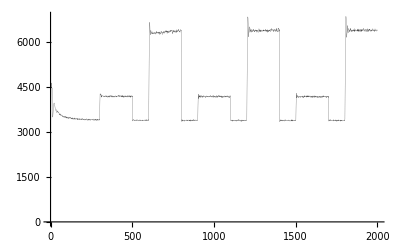

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.98,3819.55,5228.13,6245.51,6895.81,7191.77,7297.62,7235.07,7207.73,7034.23,6985.77,6939.89,6740.1,6485.41,6299.65,6103.5,5942.26,5914.65,5832.41,5803.05,5807.97,5923.93,6242.32,6293.47,6195.08,6180.,6037.25,5867.22,5660.19,5595.74,5669.33,5835.92,5829.09,5798.9,5867.75,5826.5,5797.66,5845.82,5926.87,5903.24,5818.84,5714.67,5496.49,5556.08,5522.27,5480.57,5488.79,5382.14,5311.39,5311.14,5297.77,5251.92,5215.03,5157.42,5152.61,5076.65,5074.41,4999.73,5014.79,4978.91,4972.04,4876.28,4961.58,4920.28,4883.42,4926.23,4890.13,4841.69,4778.24,4755.41,4766.83,4747.22,4716.41,4747.36,4707.03,4640.39,4663.84,4593.07,4695.29,4648.71,4606.79,4657.58,4629.62,4555.94,4526.97,4530.32,4493.5,4505.26,4541.48,4539.42,4507.33,4495.85,4528.95,4564.45,4603.91,4655.74,4696.37,4676.39,4657.58,4629.76,4618.41,4584.87,4580.4,4545.32,4577.24,4498.3,4502.22,4504.6,4424.39,4462.86,4495.86,4507.13,4504.11,4560.98,4555.36,4554.37,4539.5,4575.26,4629.16,4603.1,4623.79,4603.32,4532.55,4483.69,4541.08,4548.79,4627.46,4583.04,4553.73,4551.39,4645.22,4635.23,4564.7,4522.2,4519.08,4442.77,4402.55,4462.27,4510.62,4564.21,4523.55,4508.74,4561.42,4658.27,4745.95,4725.21,4689.05,4699.08,4708.58,4795.2,4775.08,4651.06,4685.,4755.43,4702.36,4622.58,4684.5,4643.55,4626.77,4649.06,4634.41,4646.41,4629.63,4641.75,4665.63,4777.22,4723.69,4793.08,4732.72,4666.39,4668.66,4688.36,4696.05,4692.58,4563.96,4557.94,4632.88,4725.71,4765.99,4804.74,4726.95,4683.36,4643.3,4633.2,4638.57,4571.29,4656.36,4629.13,4655.43,4633.57,4711.05,4715.47,4716.22,4730.23,4682.11,4725.7,4877.,4874.39,4856.64,4848.11,4969.45,4794.08,4760.82,4849.28,4900.97,4831.68,4818.56,4774.41,4768.03,4780.75,4859.28,4787.33,4738.99,4781.95,4707.39,4827.67,4731.65,4867.51,4935.37,5013.32,4983.91,4900.5,4807.34,4928.97,5050.26,5014.32,4891.08,4863.54,4902.66,4904.98,4917.59,4841.85,4755.19,4847.79,4854.49,4843.49,4929.97,4877.66,4911.17,4898.9,4882.74,4861.03,4857.4,4878.16,4960.89,4960.95,4977.31,4962.27,4865.88,4912.49,4918.88,4939.01,4953.74,4942.16,4898.83,4934.82,4989.86,5029.17,4919.23,4940.05,4972.36,4911.66,4811.28,4811.87,4840.83,4858.27,4859.45,4867.15,4889.25,4913.63,4869.92,4872.42,4843.08,4926.88,4992.71,5033.56,4998.29,4990.67,5039.13,5086.07,5171.31,5157.6,5113.9,5098.05,5100.36,5092.57,5095.88,5056.52,5060.85,4961.49,4880.38,4892.79,4826.65,4881.32,4846.84,4892.86,5020.27,4985.95,4990.5,5018.06,5014.57,5133.76,5173.65,5129.62,5044.71,5017.82,5055.42,5133.04,5135.21,5130.96,5163.28,5221.9,5179.33,5193.38,5171.56,5128.11,5149.85,5153.59,5113.22,4983.52,4979.69,4901.34,4951.81,5008.98,5119.56,5068.96,4995.49,4883.27,4839.89,4946.53,4996.,4960.3,4898.51,5010.,4959.41,5017.04,5142.53,5092.67,5040.37,5067.29,4981.43,4924.57,4949.56,4944.07,4949.65,4971.02,4950.43,4930.18,4988.69,5072.75,5084.78,4990.47,5037.58,5045.15,5129.48,5045.33,5026.16,5096.49,5176.51,5206.29,5181.35,5145.93,5218.29,5298.57,5188.68,5210.12,5243.48,5212.81,5079.57,5151.42,5117.63,5151.85,5157.54,5144.7,5105.13,5066.27,5138.73,5182.94,5249.8,5227.28,5236.01,5227.21,5120.51,5124.48,5192.93,5211.84,5113.59,4986.45,4945.6,4994.41,5041.86,5079.75,5128.82,5116.07,5114.01,5028.49,5103.36,5147.74,5226.44,5291.27,5255.02,5213.75,5219.3,5248.29,5291.74,5297.04,5322.16,5227.12,5191.74,5097.03,5058.97,5068.34,5099.73,5051.84,5033.52,5008.55,5103.76,5064.19,5081.99,5154.32,5187.95,5112.91,5194.9,5327.33,5385.54,5327.73,5250.99,5162.6,5186.34,5231.69,5239.58,5228.49,5242.86,5255.33,5240.55,5252.08,5303.06,5342.29,5401.09,5336.76,5353.84,5226.06,5217.66,5232.49,5243.39,5258.61,5241.45,5153.56,5153.68,5184.07,5193.32,5188.94,5228.63,5147.14,5234.03,5254.19,5288.05,5274.36,5283.7,5341.99,5347.53,5409.95,5496.19,5447.15,5437.99,5420.83,5396.6,5430.39,5413.96,5288.98,5245.56,5234.25,5245.21,5290.78,5290.47,5226.98,5251.93,5311.74,5394.77,5356.68,5371.14,5342.66,5298.01,5277.08,5351.38,5478.76,5492.92,5555.31,5426.5,5323.06,5330.17,5420.59,5393.03,5394.87,5283.93,5344.91,5386.02,5333.8,5390.12,5484.91,5484.94,5439.6,5410.64,5405.82,5336.65,5231.95,5257.12,5269.73,5271.21,5317.39,5354.33,5362.87,5274.47,5200.46,5135.17,5145.83,5236.65,5229.81,5374.6,5344.99,5260.97,5265.33,5296.9,5213.36,5156.75,5161.05,5201.04,5177.,5216.65,5165.58,5278.26,5382.86,5352.96,5261.74,5247.93,5260.94,5366.76,5469.58,5482.22,5486.99,5580.01,5617.24,5688.31,5659.73,5545.8,5431.47,5440.3,5466.63,5416.13,5422.36,5413.76,5465.81,5504.08,5477.51,5511.22,5425.26,5427.03,5433.43,5488.58,5439.38,5392.59,5481.13,5422.78,5520.53,5531.67,5394.05,5441.52,5502.13,5505.58,5545.19,5519.29,5356.74,5232.1,5271.55,5421.74,5546.69,5547.5,5462.88,5435.29,5547.89,5621.72,5555.97,5486.58,5302.81,5327.38,5188.74,5295.87,5408.49,5341.74,5385.14,5283.32,5298.99,5259.77,5301.01,5367.75,5416.24,5515.12,5540.76,5494.31,5454.76,5463.33,5561.81,5423.91,5368.04,5463.59,5573.19,5533.09,5470.99,5419.64,5481.45,5649.86,5731.72,5719.34,5621.72,5586.66,5571.18,5557.27,5682.14,5674.81,5673.9,5515.55,5511.62,5530.36,5466.21,5522.99,5579.66,5701.21,5718.45,5737.86,5525.87,5448.71,5477.14,5460.5,5463.16,5465.21,5456.7,5455.32,5529.04,5443.88,5474.09,5491.18,5511.38,5574.68,5541.24,5517.26,5440.2,5511.37,5592.09,5651.01,5539.13,5501.57,5512.58,5577.52,5564.95,5502.81,5485.85,5584.15,5720.85,5649.59,5556.25,5580.41,5568.61,5618.55,5583.16,5560.37,5534.94,5557.63,5559.93,5563.45,5565.45,5637.44,5559.55,5508.62,5500.05,5628.52,5564.13,5599.47,5560.14,5560.69,5574.42,5563.1,5581.62,5413.28,5433.17,5391.58,5470.39,5454.13,5558.78,5546.7,5535.54,5565.98,5461.78,5472.6,5546.78,5553.45,5508.26,5412.51,5509.34,5555.45,5507.33,5641.02,5626.07,5616.65,5560.45,5609.28,5663.28,5717.29,5828.54,5886.43,5829.16,5717.24,5713.73,5721.33,5685.5,5551.21,5589.79,5494.32,5668.44,5758.21,5789.87,5705.21,5673.39,5655.7,5633.55,5733.06,5817.8,5857.6,5896.89,5864.74,5770.82,5704.31,5645.02,5747.19,5686.77,5741.57,5752.91,5581.41,5471.8,5471.86,5542.79,5692.98,5736.8,5722.2,5626.16,5666.97,5656.85,5666.92,5715.9,5596.32,5598.46,5554.69,5588.44,5579.13,5668.21,5638.95,5638.72,5570.22,5507.12,5522.44,5609.72,5615.01,5594.35,5569.11,5564.03,5666.22,5787.59,5804.95,5673.79,5758.96,5886.4,5840.58,5789.53,5827.49,5799.46,5748.52,5785.01,5903.3,5817.19,5704.11,5675.32,5745.62,5786.72,5838.44,5821.91,5812.57,5867.54,5877.33,5713.12,5596.28,5464.64,5484.27,5550.51,5621.43,5809.06,5907.71,5906.94,5843.7,5678.37,5645.94,5652.87,5616.76,5720.56,5764.32,5603.46,5557.11,5619.56,5614.51,5606.88,5666.53,5564.69,5553.96,5457.99,5520.24,5541.15,5584.86,5586.39,5545.02,5474.7,5525.6,5553.67,5687.33,5679.87,5620.72,5683.41,5774.94,5792.17,5718.81,5566.75,5569.19,5482.44,5553.65,5609.4,5594.85,5594.15,5735.48,5784.68,5731.85,5746.77,5782.1,5801.78,5837.55,5891.61,5903.18,5842.64,5770.54,5646.66,5726.46,5893.85,5901.66,5869.66,5743.1,5727.04,5743.17,5738.78,5825.51,5787.91,5728.08,5673.43,5738.24,5773.57,5861.05,5976.3,5900.67,5879.04,5825.4,5918.97,5735.26,5669.48,5622.75,5645.2,5830.46,5788.18,5761.07,5711.82,5650.58,5709.48,5807.22,5699.01,5585.86,5678.18,5708.62,5811.09,5888.23,5855.57,5861.59,5839.74,5843.29,5936.04,5941.99,5831.16,5883.3,5852.23,5962.31,5916.53,5888.26,5842.13,5892.29,6042.75,6046.22,5961.66,5938.4,5895.52,5960.18,5864.18,5689.72,5603.3,5709.28,5761.51,5742.63,5764.92,5780.49,5875.75,5796.25,5763.32,5811.38,5807.43,5711.76,5572.13,5625.88,5635.89,5592.44,5735.3,5712.77,5716.93,5684.47,5809.58,5833.13,5887.74,5839.16,5894.83,5953.44,6036.16,5966.28,5934.23,5932.86,5892.95,5848.99,5886.7,5809.34,5812.09,5922.47,6012.98,6122.12,6041.93,5936.61,6010.22,5920.81,5888.85,5827.9,5743.87,5806.9,5969.28,6044.19,6028.79,5864.67,5692.52,5789.26,5914.29,5825.37,5759.94,5826.76,5954.14,5896.35,5801.84,5676.66,5669.06,5683.21,5840.22,5883.03,5809.59,5752.92,5661.31,5639.97,5674.31,5778.51,5755.59,5776.,5673.24,5717.11,5647.54,5680.17,5780.78,5937.29,5890.29,5885.59,5879.4,5931.16,6015.15,6081.63,6105.45,6029.13,5890.43,5885.18,5919.95,6045.3,5953.92,5910.69,5940.88,5982.09,5826.02,5818.28,5925.89,5940.04,5983.5,5940.85,5914.64,5796.73,5745.85,5736.11,5745.6,5899.2,5929.68,5994.58,5932.61,5936.42,5921.71,5898.14,5861.88,5764.55,5780.18,5693.84,5782.47,5833.38,5841.44,5804.77,5802.8,5763.16,5644.1,5526.74,5526.42,5523.65,5626.14,5804.48,5864.49,5886.07,5772.,5728.05,5699.31,5788.37,5885.28,5982.47,6035.2,5954.1,5960.7,5876.42,5909.74,6002.83,6210.03,6224.13,6180.58,6208.99,6059.68,5999.19,5890.33,5939.96,6025.64,6030.28,6049.29,6059.39,5931.75,5931.81,5934.07,6077.68,6102.65,6081.24,5892.25,5924.87,5883.94,5904.2,5866.9,5848.49,5843.72,5893.94,5927.77,5893.86,5914.72,5875.11,5992.15,6029.84,5975.51,5806.72,5849.85,5966.71,6131.64,5922.81,5823.36,5968.53,6026.12,5871.52,5862.93,5788.13,5901.3,5912.35,6038.36,5989.12,6007.1,6042.09,5975.9,6104.81,6109.61,6000.1,5939.91,5943.82,5866.4,5896.95,5917.55,5955.86,6054.48,6091.35,6096.3,6168.55,6128.99,6100.85,5898.15,5802.53,5782.25,5792.9,5875.34,5938.26,5762.15,5723.27,5864.45,5822.91,5844.72,5917.8,5951.23,5976.8,5904.64,5796.5,5763.6,5777.2,5953.57,5842.97,5892.72,5861.12,5955.08,6012.52,5993.25,5938.04,5826.26,5780.74,5962.93,6027.61,5984.18,5804.75,5805.23,5804.07,5730.47,5789.49,5813.6,5951.88,6033.02,6053.7,5965.5,5961.98,5877.5,5836.1,5751.52,5765.65,5903.74,5965.79,5869.25,5937.79,5951.27,5862.27,5778.93,5746.97,5851.,5895.49,5851.15,5942.32,6028.16,5896.99,5856.26,5915.37,5955.53,5853.31,5830.96,5802.41,5846.65,5934.,5936.01,6024.87,5981.51,6091.93,6108.34,6187.08,6123.65,6032.27,6063.2,6028.9,5976.6,6033.65,6024.,5986.75,6071.68,6068.86,6077.3,6042.23,5973.77,5988.03,6054.61,6112.57,6111.38,6024.81,5942.07,5793.08,5833.26,5904.39,5873.14,5959.06,6055.28,6174.92,6157.1,6079.81,5937.31,5782.97,5768.13,5915.03,5940.28,6010.71,5911.52,5889.29,5900.32,6099.08,6172.17,6098.06,6037.17,6088.88,6058.85,6144.44,6193.,6061.73,6066.7,6193.96,6220.3,6284.68,6201.58,6057.04,6045.,6059.77,6155.35,6204.3,6160.22,6116.95,5941.74,5775.89,5854.09,5993.02,6060.53,6118.23,6224.35,6301.35,6281.37,6195.94,6154.28,6177.13,6157.33,6148.4,6145.66,6145.31,6156.91,6086.35,6031.06,6010.8,6016.4,6014.34,5820.07,5827.46,5952.65,6085.27,6099.83,6132.23,6103.73,6087.65,6184.81,6220.62,6138.25,6057.63,6157.93,6228.24,6151.18,6047.56,5921.98,6050.08,6148.08,6102.41,6034.48,6110.32,6007.56,5899.52,5925.8,6002.99,6060.85,6064.49,5941.87,5966.54,6056.92,6117.81,6088.18,5969.89,5904.53,5981.6,6091.79,6079.65,6187.6,6255.92,6284.81,6243.06,6066.78,6058.3,5939.5,5921.56,5953.6,6053.4,6135.48,6247.82,6222.11,6176.18,6015.97,5833.24,5979.55,6083.65,6074.08,6007.07,6043.97,6023.17,5971.99,5922.93,6039.3,6155.,6164.19,6233.75,6224.23,6018.98,5982.07,6028.73,6045.93,6121.41,6171.44,6265.22,6196.22,6072.52,6058.28,6008.55,6169.15,6277.64,6214.82,6190.14,6071.57,6107.27,6119.71,6063.88,6140.33,6165.66,6115.77,6210.13,6093.17,6134.92,6158.61,6058.61,6030.26,6122.66,6107.01,6092.07,6065.53,6032.12,6078.15,6205.4,6148.64,6030.53,6007.62,5958.19,5863.65,5858.86,5925.97,5941.,6054.07,6239.,6282.36,6221.61,6126.91,6038.19,5982.35,6094.07,6072.53,6045.46,6038.32,5968.08,5963.09,5932.93,5995.28,6007.06,6025.45,6036.32,6076.36,5923.42,6006.71,6146.87,6148.17,6099.1,6143.08,6195.6,6163.83,5980.52,6002.88,5903.63,5908.02,5959.97,6019.31,6022.2,6098.9,6215.69,6090.32,6030.72,5888.78,5954.8,5984.89,5946.22,5950.36,5941.67,5951.41,6016.57,6093.05,6191.64,6242.03,6053.34,5951.24,5882.76,5962.79,6037.16,6052.27,6256.41,6405.41,6541.53,6418.81,6411.47,6361.86,6346.13,6233.14,6226.11,6273.87,6344.36,6395.85,6382.75,6304.39,6279.09,6290.6,6311.74,6106.31,6144.82,6284.18,6181.68,6092.51,6196.03,6231.02,6181.99,6162.19,6178.61,6229.78,6262.31,6118.92,6114.92,6129.73,6186.11,6146.64,6143.11,6110.52,6020.13,6091.4,6084.32,6123.02,6122.97,6191.43,6281.26,6235.51,6298.95,6256.39,6296.02,6239.5,6273.87,6206.99,6263.1,6252.58,6297.02,6313.72,6239.64,6291.7,6486.42,6503.74,6408.34,6324.92,6082.87,5980.24,5919.27,6054.21,6096.,6118.82,6182.93,6276.33,6367.44,6380.9,6265.15,6232.07,6070.17,6025.47,6056.2,5976.65,6032.28,5969.5,6015.23,6059.03,6026.77,6070.14,6119.25,6021.43,6046.61,6071.5,5998.62,5969.41,5998.7,6088.21,6055.79,6075.04,6168.59,6147.59,6187.27,6097.25,6214.59,6082.72,5991.22,6071.71,6105.42,6018.72,5995.23,5939.01,5782.68,5926.36,6013.04,6173.29,6149.67,6088.42,6057.12,6128.53,6234.79,6258.09,6226.07,6211.56,6188.2,6160.05,6190.03,6139.52,6205.96,6282.33,6295.58,6376.24,6197.09,6168.28,6095.18,6103.26,6131.33,6196.82,6200.13,6280.33,6318.65,6275.6,6334.9,6271.03,6301.18,6361.88,6316.47,6200.24,5994.07,6187.7,6464.59,6616.5,6494.46,6352.37,6262.64,6195.45,6299.27,6333.46,6458.25,6480.84,6358.94,6265.82,6296.37,6244.36,6304.66,6226.27,6265.17,6312.63,6093.95,6052.31,6011.58,5931.33,5920.9,6034.15,6061.88,6037.95,6020.94,6060.93,6087.71,6129.21,6173.2,6371.2,6292.85,6240.19,6107.18,6185.28,6168.19,6153.41,6163.8,6172.59,6170.53,6121.73,6173.07,6177.07,6184.75,6185.07,6119.89,6147.62,6117.59,6106.53,6189.66,6192.46,6257.43,6171.27,6080.8,6124.6,6115.71,6199.98,6134.84,6160.31,6201.65,6289.54,6247.28,6252.59,6206.78,6082.62,5962.14,5922.39,6044.06,6071.95,6111.22,6171.37,6153.46,6054.13,6144.27,6137.9,6129.03,6159.06,6228.62,6365.86,6338.04,6244.82,6205.97,6270.06,6397.25,6412.94,6190.98,6091.53,6219.06,6288.03,6292.21,6279.15,6407.26,6387.55,6385.63,6423.57,6415.2,6315.78,6177.85,6182.41,6145.84,6141.6,6190.89,6216.85,6402.7,6331.98,6316.92,6334.42,6298.8,6284.,6338.24,6287.91,6282.78,6340.58,6350.2,6417.67,6342.73,6321.61,6256.32,6251.25,6344.44,6487.18,6511.66,6452.37,6300.75,6207.29,6282.32,6402.02,6396.25,6468.94,6378.98,6313.01,6189.73,6178.86,6158.25,6173.88,6250.54,6200.97,6279.42,6334.77,6412.15,6427.2,6402.22,6513.5,6383.98,6425.97,6466.87,6355.71,6266.01,6312.58,6192.96,6185.07,6268.56,6338.56,6374.32,6525.37,6410.37,6251.53,6224.95,6168.19,6129.89,6168.95,6224.55,6314.02,6411.54,6417.39,6451.79,6457.36,6512.49,6528.02,6401.6,6394.81,6288.16,6281.53,6355.55,6309.69,6364.01,6379.41,6391.33,6382.53,6428.16,6275.54,6161.29,6141.62,6111.15,6132.03,6297.83,6288.44,6422.58,6476.84,6585.17,6488.99,6331.89,6329.13,6264.89,6400.05,6498.77,6545.81,6352.85,6323.71,6325.78,6305.46,6306.64,6492.38,6467.26,6507.81,6576.71,6650.61,6671.6,6512.41,6474.6,6324.16,6367.75,6489.61,6316.47,6306.77,6350.18,6398.91,6437.1,6429.87,6478.89,6433.52,6298.3,6137.17,6118.69,6237.,6374.79,6431.64,6464.36,6409.35,6422.99,6413.23,6365.71,6410.47,6485.14,6477.66,6521.46,6367.5,6348.54,6275.19,6223.95,6223.82,6133.24,6164.31,6119.96,6216.87,6278.23,6175.8,6246.72,6152.38,6192.67,6362.4,6457.9,6418.1,6349.91,6292.97,6261.12,6292.89,6285.75,6251.8,6272.63,6272.26,6363.73,6296.24,6319.8,6369.27,6433.43,6328.07,6286.79,6226.7,6147.66,6174.87,6163.58,6290.38,6466.73,6567.2,6486.88,6280.83,6356.58,6288.43,6300.27,6193.04,6113.87,6197.19,6263.25,6403.17,6384.08,6262.35,6329.7,6331.69,6337.65,6473.73,6415.65,6414.13,6349.25,6231.23,6323.9,6312.76,6278.59,6243.42,6365.88,6361.69,6245.23,6141.6,6128.94,6175.99,6206.92,6197.64,6249.55,6254.48,6199.32,6384.63,6284.54,6259.75,6304.01,6221.2,6376.86,6472.22,6538.67,6454.75,6347.17,6097.04,6107.84,6215.98,6352.31,6449.26,6339.4,6188.3,6154.17,6239.7,6162.09,6133.19,6115.47,6048.49,6189.73,6145.5,6161.88,6254.41,6267.41,6189.06,6212.33,6232.57,6317.42,6199.23,6211.59,6200.26,6273.69,6371.67,6335.27,6487.5,6489.16,6483.98,6384.63,6381.86,6256.55,6272.76,6343.91,6271.6,6301.74,6312.81,6407.06,6365.77,6310.44,6311.76,6153.4,6233.33,6296.2,6392.53,6353.02,6410.29,6417.28,6473.39,6468.37,6450.1,6362.32,6325.45,6353.54,6390.89,6347.56,6397.94,6348.46,6313.21,6180.79,6155.67,6146.68,6291.52,6319.97,6432.71,6457.82,6458.73,6460.39,6408.51,6377.28,6250.65,6161.49,6230.96,6289.2,6338.18,6442.29,6472.68,6440.22,6288.02,6166.14,6191.28,6133.41,6080.05,6211.33,6288.73,6376.55,6380.1,6218.34,6127.53,6254.42,6297.4,6357.55,6331.54,6303.77,6412.47,6503.77,6498.91,6477.3,6451.74,6416.45,6330.69,6282.65,6285.73},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in {2031.91`, 3229.9500000000003`, 3710.7200000000003`, 3813.1`, 3858.27`, 4023.76`, 4195.85`, 4282.6`, 4441.58`, 4639.39`, 4858.18`, 4900.97`, 5008.91`, 5036.75`, 5070.3`, 5259.12`, 5322.53`, « 17 », 6571.93`, 6664.4800000000005`, 6544.24`, 6247.2`, 6376.67`, 6298.37`, 6575.93`, 6586.46`, 6627.08`, 6675.6900000000005`, 6481.55`, 6538.78`, 6747.9800000000005`, 6583.62`, 6519.24`, 6564.26`, « 1950 »}, « 2 », PlotStyle → {InterpretationBox[ButtonBox[« 1 », Rule[Appearance, None], Rule[BaseStyle, List[]], Rule[BaselinePosition, Baseline], Rule[DefaultBaseStyle, List[]], RuleDelayed[ButtonFunction, With[List[Set[Typeset`box$, EvaluationBox[]]], If[Not[AbsoluteCurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.91,3229.95,3710.72,3813.1,3858.27,4023.76,4195.85,4282.6,4441.58,4639.39,4858.18,4900.97,5008.91,5036.75,5070.3,5259.12,5322.53,5404.44,5421.22,5344.94,5628.13,5626.54,5678.12,5698.12,5691.72,5900.59,5837.41,5882.88,5984.96,6094.48,6051.77,6125.09,6258.89,6333.28,6571.93,6664.48,6544.24,6247.2,6376.67,6298.37,6575.93,6586.46,6627.08,6675.69,6481.55,6538.78,6747.98,6583.62,6519.24,6564.26,6761.43,6810.92,6816.61,6765.3,6660.39,6845.85,6788.61,6726.62,6667.03,6491.4,6739.27,7058.13,6895.21,6824.73,6929.69,7057.54,6980.82,6836.9,6822.9,6837.49,6891.01,6906.58,6947.19,7011.88,7191.54,7072.45,7127.38,7128.04,7022.13,6999.55,7031.86,7221.34,7220.72,7040.8,6902.68,7142.32,7363.69,7322.94,7259.34,7244.79,7378.88,7286.01,7454.53,7240.76,7236.44,7069.74,6927.14,6936.81,6965.67,6995.54,7263.68,7160.01,7142.81,7096.98,6870.84,6827.13,7003.56,7098.93,7155.5,7172.61,7142.99,7120.34,7105.53,7283.43,7214.66,7144.16,7080.33,6974.96,7010.35,6975.53,7012.2,7006.58,7120.75,7165.57,7291.9,7204.95,7350.87,7339.1,7434.92,7360.28,7374.62,7231.51,7035.5,7057.24,7329.32,7143.54,7081.57,7215.54,7381.14,7354.87,7214.04,7212.94,7223.02,7241.93,7137.14,7141.73,7214.,7216.49,7222.47,7250.51,7216.93,7299.85,7255.84,7187.98,7227.23,7178.95,7241.6,7517.65,7385.75,7451.4,7383.12,7296.59,7341.56,7443.45,7277.91,7229.67,7258.37,7213.45,7071.29,7182.89,7247.42,7104.14,7067.58,7255.9,7254.72,7332.73,7153.86,7225.28,7389.77,7462.13,7151.8,7050.98,6973.63,7043.31,7059.22,7288.07,7155.45,7395.33,7391.91,7344.76,7274.47,6920.46,7087.83,7115.83,6957.4,7033.25,6989.43,6939.32,6921.25,7240.5,7437.81,7369.55,7382.39,7337.08,7597.6,7313.12,7201.17,7498.24,7393.09,7445.46,7486.54,7530.35,7585.71,7439.03,7253.49,7366.42,7245.52,7285.77,7278.93,7374.59,7346.47,7291.95,7192.69,7156.22,7185.74,7025.37,7154.57,7262.3,7348.36,7116.75,7033.66,7231.94,7009.27,6950.66,7104.32,7260.28,7277.25,7057.21,7031.77,7095.51,7057.4,7120.22,7082.92,7183.73,7162.54,7324.19,7322.47,7460.26,7449.83,7365.97,7406.62,7367.26,7299.49,7211.49,7204.53,7105.14,7076.84,7227.07,7443.19,7492.01,7376.6,7393.12,7371.24,7272.63,7384.5,7294.58,7349.97,7209.12,7245.67,7257.04,7185.38,7311.93,7298.27,7159.6,7051.83,7074.06,7246.83,7322.43,7187.92,7441.34,7334.72,7156.39,7211.31,7231.57,7035.59,7200.29,7467.38,7441.01,7442.93,7330.37,7269.41,7287.13,7214.97,7309.2,7196.11,7148.83,7221.,7426.21,7436.6,7299.46,7119.05,7005.79,7116.16,7206.44,7183.49,7149.88,7171.98,7477.57,7450.67,7287.81,7343.13,7416.55,7716.92,7706.24,7441.39,7290.82,7433.24,7309.34,7495.51,7314.68,7217.91,7171.36,7132.25,7008.75,7385.92,7380.01,7189.53,7188.06,7362.3,7287.72,7415.32,7472.84,7246.17,7202.7,7321.23,7423.66,7672.16,7739.79,7545.89,7395.27,7421.8,7310.36,7465.76,7483.6,7352.76,7316.28,7203.58,7172.06,6974.43,7301.1,7409.99,7401.93,7399.07,7219.64,7338.51,7397.33,7667.55,7588.33,7297.22,7364.04,7579.45,7650.71,7731.65,7617.3,7465.58,7470.33,7462.12,7596.74,7636.07,7529.78,7338.88,7343.72,7300.23,7331.39,7443.91,7526.99,7397.2,7492.07,7444.24,7404.61,7215.77,7213.83,7339.84,7407.99,7453.23,7464.86,7376.99,7455.93,7344.72,7371.63,7485.85,7441.56,7643.58,7534.51,7377.51,7403.63,7328.89,7362.21,7580.72,7558.29,7476.8,7464.8,7411.32,7364.49,7349.01,7381.5,7298.85,7341.68,7248.69,7074.97,7122.93,7248.89,7341.41,7327.62,7378.51,7255.71,7418.66,7659.14,7885.15,7763.56,7454.89,7581.36,7665.44,7540.39,7308.25,7050.23,7110.2,7257.4,7448.89,7343.13,7263.76,7370.5,7339.82,7455.07,7562.64,7627.15,7585.8,7587.85,7677.42,7558.52,7269.75,7203.,7227.27,7314.88,7212.25,7173.07,7265.69,7623.62,7385.62,7347.2,7267.06,7339.05,7282.29,7290.38,7324.36,7354.32,7337.62,7402.92,7385.8,7350.23,7539.74,7488.62,7306.81,7368.67,7407.15,7461.06,7270.2,7251.87,7014.64,7001.4,7166.68,7177.26,7045.26,7135.83,7125.08,7131.24,7284.52,7320.98,7216.14,7195.17,7257.39,7048.29,6924.74,7135.38,7285.54,7339.86,7528.01,7509.61,7555.72,7687.26,7409.51,7209.79,7299.02,7348.,7584.72,7485.42,7192.77,7210.47,7419.74,7587.9,7711.27,7588.72,7558.97,7390.09,7192.22,7310.98,7396.33,7367.15,7332.74,7168.39,7105.61,7236.33,7245.3,7205.21,7242.06,7132.32,7220.3,7330.99,7084.75,7182.33,7274.38,7239.26,7174.61,7340.86,7366.09,7341.37,7390.27,7557.9,7444.35,7602.82,7530.41,7363.94,7131.5,7287.09,7395.93,7316.37,7331.58,7342.37,7337.03,7210.01,7360.02,7377.53,7328.64,7224.08,7232.14,7214.07,7136.22,7220.36,7279.63,7306.6,7311.54,7273.33,7236.31,7113.09,7164.37,7270.3,7153.46,7332.7,7347.21,7245.21,7199.08,7504.48,7296.13,7226.2,7404.42,7185.85,7202.37,7303.61,7258.27,7283.32,7214.58,7321.04,7362.49,7286.05,7239.55,7446.53,7640.56,7517.76,7312.33,7375.33,7474.25,7388.87,7399.21,7413.69,7462.03,7554.,7441.69,7497.45,7553.79,7622.93,7491.89,7327.6,7344.25,7473.42,7252.38,7270.05,7162.68,7204.64,7291.92,7216.28,7340.65,7554.86,7669.68,7704.26,7491.54,7399.15,7294.27,7332.59,7452.01,7367.39,7388.4,7188.,7494.4,7425.85,7337.29,7365.52,7371.04,7300.79,7277.49,7229.21,7297.4,7529.82,7393.19,7401.46,7357.01,7296.69,7388.58,7216.47,7035.09,7116.24,7291.51,7493.24,7513.53,7561.33,7462.18,7562.77,7588.49,7419.27,7438.09,7388.31,7493.89,7595.33,7395.68,7228.24,7081.32,7049.8,7173.92,7261.2,7495.3,7652.58,7741.02,7622.03,7478.34,7437.18,7277.54,7156.95,7347.74,7438.85,7376.89,7507.86,7566.94,7488.31,7289.35,7151.52,7201.54,7440.41,7466.39,7416.09,7496.1,7333.07,7307.46,7350.79,7565.06,7509.52,7504.67,7428.91,7643.48,7555.36,7566.98,7586.61,7337.82,7233.53,7243.89,7204.26,7211.63,7084.06,7184.6,7341.86,7559.29,7556.74,7445.13,7312.94,7223.23,7256.48,7405.62,7435.33,7314.19,7193.49,7403.21,7541.77,7372.17,7389.12,7429.71,7431.71,7493.31,7516.02,7182.54,7209.91,7092.55,7141.66,7151.76,7134.82,7172.62,7280.,7308.12,7349.28,7210.71,7324.88,7401.08,7455.37,7223.99,7263.34,7259.15,7127.39,7123.63,7334.52,7222.84,7089.39,7117.78,7187.83,7205.15,7194.4,7220.71,7261.37,7347.6,7423.99,7532.47,7482.06,7424.91,7211.,7029.06,7278.47,7154.12,7156.14,7081.09,7322.42,7437.09,7561.03,7768.95,7530.41,7445.24,7485.77,7375.6,7448.82,7576.08,7558.05,7676.91,7529.91,7330.89,7460.47,7506.62,7283.43,7246.08,7266.72,7320.66,7360.93,7344.83,7156.1,7045.7,7118.31,7159.72,7357.33,7433.27,7358.93,7301.87,7310.16,7470.75,7514.29,7255.12,7323.18,7450.45,7442.48,7555.8,7302.04,7239.28,7222.4,7511.68,7484.26,7618.14,7336.49,7297.89,7263.13,7399.66,7474.69,7521.17,7346.39,7246.15,7302.,7312.74,7233.01,7401.09,7155.26,7206.21,7334.73,7338.05,7398.59,7264.13,7182.19,7064.25,7082.83,7122.44,7119.46,7185.67,7345.58,7254.47,7280.65,7261.33,7263.43,7287.58,7169.43,7204.78,7383.64,7419.06,7254.29,7251.01,7197.69,7112.62,7114.88,7088.71,7125.52,7335.78,7398.62,7184.71,7159.4,7447.92,7419.46,7239.78,7211.22,7337.97,7436.97,7381.45,7148.64,7173.71,7173.95,7247.36,7096.54,7291.91,7109.36,7287.82,7350.27,7264.62,7184.98,7274.47,7274.37,7218.43,7105.82,7048.47,7070.12,7164.06,7243.3,7233.94,7092.22,7099.24,7060.64,7303.42,7484.32,7219.79,7193.75,7184.82,7037.81,7088.89,7088.82,7242.93,7276.94,7384.41,7443.87,7196.32,7159.21,7231.44,7361.59,7295.27,7273.52,7178.2,7189.57,7107.96,7302.78,7423.72,7211.66,7268.37,7304.18,7439.62,7320.96,7365.5,7299.13,7247.34,7114.22,7070.2,7027.22,7029.57,7132.71,7011.72,7057.73,7188.56,7189.57,7228.89,7184.08,7153.29,7107.44,7199.97,7141.81,7031.83,7162.93,7303.69,7141.84,6937.18,7199.27,7383.46,7108.17,7035.78,7051.32,6952.23,6761.37,6887.56,7134.4,7141.12,6976.48,7061.73,7188.14,7188.45,7134.76,7218.1,7147.67,7310.06,7216.1,7239.15,7323.53,7207.37,7192.51,7240.94,7168.5,7322.48,7250.2,7173.58,7088.33,6993.84,7161.19,7246.18,7184.91,7071.02,7193.15,7088.2,7185.48,7228.06,7120.5,7240.5,7391.43,7260.29,7095.44,7060.86,7288.35,7579.46,7453.39,7437.15,7479.81,7359.62,7257.49,7501.13,7394.85,7421.7,7697.6,7487.34,7259.82,7147.93,7071.55,7218.7,7272.76,7205.02,7231.63,7353.77,7449.99,7372.74,7304.69,7477.72,7491.8,7402.94,7238.87,7292.44,7488.66,7416.64,7577.25,7492.42,7331.68,7412.25,7390.55,7564.62,7430.96,7451.29,7315.01,7280.59,7532.08,7581.11,7800.78,7578.05,7366.12,7290.39,7435.06,7421.42,7407.71,7240.98,7250.35,7250.98,7232.94,7160.66,7280.33,7212.61,7054.35,7097.93,7272.42,7436.06,7317.79,7225.47,7281.97,7476.7,7519.56,7327.42,7327.59,7460.24,7448.55,7513.9,7350.48,7233.81,7263.97,7238.07,7347.96,7378.1,7365.58,7448.72,7507.04,7510.11,7311.97,7482.07,7527.11,7473.61,7464.43,7552.68,7403.81,7333.64,7309.74,7268.92,7395.44,7329.94,7226.58,7293.42,7192.97,7215.5,7249.17,7333.29,7427.89,7455.38,7403.3,7570.44,7568.17,7418.9,7397.39,7271.31,7256.45,7402.28,7362.42,7094.37,7402.35,7505.24,7388.65,7363.17,7354.72,7567.06,7635.15,7732.66,7484.96,7266.31,7245.2,7249.13,7382.16,7485.13,7594.22,7562.49,7408.79,7178.71,7066.66,7140.5,7163.09,7106.24,6976.31,7164.18,7209.17,7147.82,7221.59,7252.19,7499.12,7537.18,7415.62,7463.36,7323.69,7305.3,7337.43,7237.02,7125.27,6919.77,7359.59,7397.53,7250.5,7331.95,7267.54,7277.88,7349.28,7544.91,7336.04,7132.28,7251.34,7401.74,7353.71,7254.08,7254.88,7554.14,7629.66,7629.84,7721.56,7468.78,7258.42,7241.01,7404.06,7483.76,7574.69,7514.98,7412.63,7450.58,7379.5,7312.16,7328.67,7083.06,7305.6,7412.67,7450.87,7466.57,7491.25,7439.68,7319.57,7531.75,7594.68,7572.36,7843.88,7895.03,7435.61,7327.07,7316.66,7373.38,7431.18,7487.67,7359.45,7416.81,7376.43,7461.32,7254.23,7216.06,7288.81,7403.79,7412.85,7397.39,7392.74,7287.81,7415.05,7484.52,7571.06,7535.36,7483.71,7556.61,7442.48,7504.52,7528.41,7417.27,7472.35,7296.76,7086.35,7254.4,7497.47,7458.89,7699.73,7696.63,7407.07,7358.82,7579.42,7423.87,7430.14,7470.79,7390.27,7328.48,7300.08,7338.52,7364.17,7454.86,7451.79,7355.55,7370.69,7589.52,7325.54,7334.05,7425.64,7547.41,7731.71,7779.11,7777.4,7862.05,7828.44,7608.83,7423.89,7362.09,7497.06,7502.07,7443.49,7497.29,7410.99,7456.12,7461.51,7382.34,7362.47,7277.68,7230.53,7491.68,7503.74,7457.32,7349.58,7579.43,7739.83,7606.09,7583.01,7426.72,7196.73,7210.78,7280.73,7271.05,7279.29,7259.38,7428.11,7350.42,7508.9,7590.36,7527.66,7413.99,7425.93,7277.87,7373.55,7369.71,7492.36,7526.34,7416.93,7344.17,7520.09,7548.79,7536.92,7460.81,7548.85,7438.71,7292.61,7188.52,7206.51,7129.51,7192.19,7061.74,7309.73,7243.95,7224.81,7187.46,7118.92,7239.98,7360.3,7476.05,7538.01,7351.39,7318.84,7360.28,7407.26,7390.21,7299.14,7398.9,7431.63,7287.66,7203.81,7260.97,7282.95,7245.02,7397.82,7529.62,7606.2,7397.08,7058.62,6986.27,7123.77,7264.71,7367.72,7520.76,7389.58,7028.18,7027.82,7105.02,7279.43,7380.63,7268.35,7273.68,7186.56,7288.87,7133.45,7289.39,7050.54,7028.07,7014.43,7033.18,7016.05,7180.92,7331.3,7375.9,7269.53,7271.52,7034.27,7046.1,7061.52,7280.63,7465.37,7251.93,7106.47,7298.68,7245.12,7319.07,7192.39,7324.89,7335.73,7188.04,7329.71,7318.34,7285.77,7309.69,7379.55,7401.48,7272.26,7400.73,7519.06,7078.29,7109.17,7290.43,7256.55,7285.78,7394.11,7345.26,7246.16,7199.73,7234.01,7193.88,7193.17,7295.61,7273.46,7165.72,6980.78,7181.59,7246.75,7409.73,7404.59,7432.61,7304.26,7136.68,7067.86,7140.93,7529.96,7561.35,7490.65,7269.35,7229.43,7408.72,7344.59,7517.5,7468.63,7361.64,7220.21,7343.81,7415.56,7421.13,7336.85,7361.3,7215.27,7180.76,7291.88,6973.76,7042.43,7130.16,7265.77,7113.65,7231.18,7186.28,7406.69,7408.55,7396.3,7305.72,7207.06,7469.91,7292.68,7358.25,7357.86,7377.92,7306.41,7286.93,7355.02,7345.75,7440.86,7389.88,7595.86,7365.2,7296.98,7232.01,7243.26,7164.67,7235.58,7557.1,7516.56,7507.51,7398.93,7422.16,7439.93,7452.04,7481.74,7654.5,7675.03,7381.15,7300.78,7236.48,7367.32,7345.1,7270.,7145.07,7221.24,7379.36,7165.25,7293.47,7291.76,7230.86,7407.08,7461.34,7284.47,7165.35,7341.49,7358.85,7183.57,7038.72,6889.94,7086.01,7212.92,7188.52,7261.25,7223.65,7379.34,7376.73,7337.93,7413.08,7321.31,7370.52,7126.43,7286.52,7375.35,7505.19,7791.83,7769.08,7586.49,7298.67,7344.27,7523.34,7568.82,7492.93,7475.83,7329.38,7283.89,7323.39,7376.93,7421.96,7531.59,7515.,7383.01,7194.98,7285.45,7163.61,7246.89,7280.71,7342.1,7378.75,7557.66,7396.76,7466.08,7207.4,7237.4,6955.02,7079.66,7020.05,7146.55,7194.13,7320.02,7232.71,7122.32,7106.98,7131.35,7212.67,7158.03,7070.34,7130.49,7228.49,7439.72,7266.84,7105.11,7138.12,7067.64,7019.12,7187.38,7475.8,7485.1,7470.59,7193.59,7324.02,7380.67,7303.34,7329.81,7262.75,7269.84,7381.88,7386.33,7157.47,7203.1,7179.6,7002.75,7170.64,7077.85,7122.39,7151.74,7297.87,7251.7,7433.44,7623.35,7440.18,7435.99,7261.41,7355.29,7286.16,7232.02,7331.85,7364.83,7390.93,7510.98,7436.77,7265.13,7208.67,7284.16,7424.6,7360.92,7243.23,7106.89,6970.64,6915.15,7155.92,7329.32,7038.06,6921.01,6982.41,7076.59,7106.02,7331.34,7257.95,7188.71,7187.32,7138.27,7048.45,6956.88,7139.12,7264.68,7072.18,7303.45,7241.26,7157.15,7239.48,7570.08,7480.14,7309.96,7147.62,7174.13,7392.96,7413.48,7340.1,7343.53,7287.65,7412.63,7401.64,7521.52,7457.92,7574.35,7520.62,7382.4,7332.21,7122.76,7179.3,7239.54,7044.41,7240.14,7248.86,7242.21,7239.69,7154.71,7171.1,7015.34,7048.25,7109.05,7083.51,7146.69,7028.38,7047.54,7294.05,7436.13,7574.,7552.13,7538.5,7266.95,7210.42,7265.43,7381.27,7254.08,7212.07,7257.74,7120.15,7087.95,7272.9,7392.73,7129.66,7132.76,7094.81,7308.41,7238.55,7146.63,7196.7,7345.17,7325.45,7165.04,7292.34,7212.89,6989.9,6949.78,7074.61,7321.92,7202.51,7343.76,7480.82,7481.17,7112.05,7402.03,7360.35,7196.27,7216.29,7329.03,7476.73,7417.92,7350.02,7280.8,7340.82,7305.25,7494.05,7177.87,7098.51,7065.57,7136.45,7217.33,7283.87,7204.66,7187.59,7112.3,7153.38,7108.05,7081.78,7160.33,7102.38,7087.23,6891.34,7056.78,7079.65,7142.78,7273.92,7306.5,7274.28,7167.51,7157.73,7305.14,7256.,7271.18,7202.31,7112.33,7349.17,7382.15,7310.87,7345.56,7325.3,7228.27,7143.45,7077.95,7170.91,7192.1,7498.46,7539.07,7374.28,7230.83,7189.25,7279.99,7339.59,7419.84,7545.98,7420.06,7471.37,7228.28,7212.37,7210.71,7289.51,7403.28,7464.38,7446.22,7545.07,7519.05,7307.75,7387.5,7264.21,7068.17,7185.65,7170.34,7374.,7257.32,7285.25,7098.12,7296.12,7208.71,7244.77,7350.8,7373.47,7194.94,7220.34,7305.49,7275.81,7111.79,7036.62,6910.33,6984.35,7224.89,7008.85,6899.57,6937.91,7056.21,7150.98,7273.61,7411.62,7446.17,7274.21,7108.85,7179.38,7233.64,7103.95,7194.04,7240.69,7159.85,7213.69,7272.3,7252.54,7333.79,7364.58,7464.58,7534.52,7488.34,7349.41,7341.76,7393.43,7161.9,7004.05,7038.32,7299.72,7334.22,7068.56,7190.92,7390.75,7336.39,7395.12,7452.86,7428.1,7412.56,7453.37,7223.95,7068.07,6793.38,6958.35,7147.06,7252.6,7256.64,7298.25,7214.18,7116.48,7081.38,7041.64,7046.57,7085.72,7223.86,7466.11,7447.17,7434.34,7366.98,7569.05,7516.76,7520.22,7465.33,7333.76,7321.73,7246.22,7136.2,7150.87,7328.27,7235.63,7407.95,7275.41,7283.54,7265.45,7366.63,7377.08,7253.99,7245.87,7104.69,7216.86,7352.53,7219.92,7401.44,7413.03,7215.3,7203.55,7130.47,7269.51,7296.23,7308.12,7322.67,7250.04,7241.21,7234.21,7320.32,7567.26,7544.36,7596.04,7486.35,7327.15,7542.88,7311.11,7373.5,7596.31,7503.01,7461.24,7447.08,7451.63,7392.46,7471.26,7442.28,7709.16,7574.77,7518.96,7491.8,7381.02,7395.4,7490.06,7538.36,7314.38,7246.66,7374.62,7285.11,7333.46,7451.6,7522.54,7711.09,7411.14,7150.44,7173.74,7115.59,7109.33,7251.22,7353.44,7376.86,7311.77,7444.07,7240.1,7258.55,7407.43,7401.46,7453.23,7368.,7078.26,7215.28,7232.89,7288.9,7277.76,7238.26,7088.33,7221.46,7151.44,7194.01,7113.96,7153.73,6976.03,7042.55,7374.88,7269.99,6964.53,6730.73,6833.92,6810.98,6924.87,7087.61,7154.53,7295.62,7260.51,7213.08,7251.35,7216.49,7147.08,7353.88,7479.4,7608.39,7408.09,7123.25,7107.59,7308.06,7519.92,7287.5,7366.09,7315.66,7165.26,7004.83,6970.9,7130.71,7087.9,7155.73,7159.12,7182.77,7180.14,7217.33,7174.94,7077.56,6851.27,7036.82,7137.96,7283.46,7288.3,7123.8,7319.69,7498.34,7362.86,7383.84,7325.9,7525.8,7518.11,7253.87,7312.15,7279.76,7306.6,7398.33,7378.11,7440.29,7422.9,7523.35,7388.5,7365.17,7355.11,7474.99,7337.84,7269.4,7144.19,7243.86,7270.51,7538.,7424.75,7171.74,7210.51,7462.17,7548.16,7377.47,7407.56,7520.6,7372.57,7244.23,7346.25,7296.22,7260.05,7301.12,7263.65,7433.7,7344.79,7276.25,7172.7,7163.58,7288.45,7179.02,7248.05,7227.87},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2031.55, 3802.78, 5158.83, 6048.83, 6556.62, 6102.59, 5324.48, 4838.02, 4523.07, 4437.6, 4339.69, 4335.37, 4259.89, 4337.92, 4261.34, 4256.32, 4326.67, « 17 », 4507.59, 4489.56, 4535.98, 4559.86, 4543.08, 4573.6, 4528.49, 4463.74, 4427.88, 4515.09, 4456.17, 4549.92, 4610.15, 4597.43, 4581.04, 4655.98, « 1950 »}, « 1 », « 1 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.55,3802.78,5158.83,6048.83,6556.62,6102.59,5324.48,4838.02,4523.07,4437.6,4339.69,4335.37,4259.89,4337.92,4261.34,4256.32,4326.67,4366.73,4341.14,4368.13,4348.27,4442.15,4409.16,4536.33,4453.6,4372.27,4450.27,4485.14,4496.5,4502.19,4476.77,4552.22,4554.58,4504.3,4507.59,4489.56,4535.98,4559.86,4543.08,4573.6,4528.49,4463.74,4427.88,4515.09,4456.17,4549.92,4610.15,4597.43,4581.04,4655.98,4559.73,4474.56,4517.8,4536.22,4579.74,4561.17,4483.99,4554.08,4553.51,4554.85,4542.35,4555.66,4582.29,4657.58,4600.52,4645.16,4688.,4731.39,4746.33,4704.27,4766.84,4737.33,4706.72,4728.16,4780.93,4726.16,4673.8,4614.68,4686.44,4794.14,4810.4,4727.62,4831.4,4831.48,4826.91,4901.36,4840.22,4914.04,4961.9,4970.87,4879.03,4854.45,4798.63,4833.37,4807.2,4852.85,4785.24,4817.44,4745.31,4778.55,4767.8,4725.09,4713.77,4730.03,4847.27,4876.87,4894.49,4900.99,4816.18,4829.91,4775.28,4830.25,4750.28,4663.5,4696.34,4757.76,4814.67,4783.22,4850.98,4888.15,4826.29,4778.28,4751.,4844.76,4899.99,4747.55,4796.42,4816.51,4819.75,4770.41,4811.38,4799.07,4789.67,4774.31,4684.33,4706.4,4738.52,4823.28,4756.92,4852.17,4870.98,4897.95,4810.63,4805.43,4799.53,4850.41,4813.54,4769.52,4738.03,4811.98,4826.06,4792.53,4858.05,4805.45,4802.64,4848.33,4928.09,4969.34,4960.22,4858.6,4840.47,4780.89,4766.83,4752.12,4739.57,4790.74,4875.26,4917.91,4845.43,4835.41,4888.23,4859.94,4805.69,4803.62,4821.15,4841.05,4773.86,4853.56,4830.39,4851.71,4873.16,4870.01,4855.74,4890.58,4908.03,4907.37,4990.52,5084.06,5029.75,4957.43,4933.9,4937.72,4945.56,4924.3,4863.91,4841.29,4772.09,4813.41,4816.92,4878.76,4824.72,4827.61,4840.02,4887.74,4823.37,4826.83,4922.63,5052.05,5124.,5019.34,4995.01,5016.37,5074.98,4954.83,4845.25,4779.76,4814.86,4889.19,4844.81,4811.31,4764.64,4777.33,4817.35,4839.75,4863.01,4843.28,4893.44,4931.48,4906.48,4961.6,4919.65,5039.9,4991.54,5020.61,5051.71,5029.64,5013.65,4970.98,4842.52,4873.98,4813.32,4812.88,4816.07,4744.12,4797.03,4819.77,4806.73,4836.75,4822.35,4873.75,4892.68,4925.56,4897.04,4753.98,4692.21,4803.59,4820.44,4771.83,4712.08,4663.53,4645.98,4777.84,4725.1,4796.22,4930.64,4870.91,4900.29,4884.59,4957.35,4906.43,4912.39,4850.61,4895.1,4859.53,4892.51,4873.33,4916.74,4926.64,4861.64,4905.92,4897.8,4951.26,4935.13,4822.04,4845.38,4837.68,4821.57,4847.77,4797.64,4782.2,4810.03,4747.53,4801.9,4811.69,4849.52,4783.65,4841.09,4851.19,4851.36,4843.09,4900.3,4838.3,4803.44,4851.45,4824.95,4832.94,4830.39,4857.45,4833.4,4818.6,4808.81,4879.01,4957.13,4953.33,4965.09,4954.62,4920.57,4936.64,4930.24,4962.34,4973.28,4987.59,4972.45,4968.86,4990.29,4904.22,4837.27,4803.11,4796.9,4850.52,4868.28,4861.23,4798.36,4849.12,4872.94,4921.58,5057.25,5055.82,4985.16,4936.18,5049.95,5110.13,5018.2,4999.92,5061.11,4982.54,5029.5,5010.11,5038.02,5058.66,4932.74,4887.92,4886.02,4986.6,4975.34,4925.74,4878.35,4852.62,4846.59,4873.18,4912.85,4941.9,4854.75,4892.64,4891.84,4968.64,4964.85,5046.77,5021.46,5029.84,5086.61,4955.31,4946.02,4878.83,5003.63,5022.09,5047.64,5094.97,5048.85,5079.18,5103.46,5012.46,4875.73,4885.67,4836.83,4945.23,4887.2,4963.21,4945.53,4966.72,5022.11,5023.13,5006.9,4982.57,4921.47,4922.03,4891.67,4967.14,5069.06,4976.26,4875.65,4900.57,4869.51,4872.4,4909.03,4941.95,4885.63,4996.62,5019.45,5075.53,5056.35,5001.93,5047.94,4979.89,4932.78,4942.78,4883.4,4846.29,4790.75,4778.09,4813.5,4870.86,4844.35,4841.68,4919.05,4959.24,4928.13,4956.2,4969.57,4954.28,4909.95,4920.69,4959.59,4968.31,4935.79,4831.09,4753.71,4922.49,5104.31,5063.34,4906.53,4905.54,4929.55,4865.95,4839.17,4882.25,4919.63,4961.04,4966.43,4882.34,4860.46,4800.17,4790.19,4788.87,4831.75,4903.04,4899.14,4936.43,4802.18,4770.11,4819.69,4907.6,4907.18,4879.57,4755.15,4782.65,4815.11,4844.98,4776.51,4777.71,4785.18,4831.38,4821.26,4840.38,4853.41,4951.31,4932.69,4873.25,4845.11,4821.96,4855.86,4890.55,4865.95,4838.34,4767.95,4811.18,4796.13,4805.2,4836.35,4842.37,4780.21,4800.03,4813.89,4892.33,4883.6,4847.49,4875.2,4953.52,4983.07,5012.66,5045.17,5072.27,4957.04,4943.68,4960.14,4963.53,4959.31,4967.12,4911.18,4878.88,4889.37,4906.97,4826.45,4862.13,4951.95,4998.24,4904.87,4778.57,4830.69,4811.86,4743.09,4853.53,4840.85,4944.93,4929.92,5006.1,5001.77,5035.38,4992.28,5002.74,5034.95,4965.32,4872.11,4830.97,4861.21,4943.9,4979.85,4983.27,4929.03,4936.14,5033.76,4989.49,4850.19,4824.19,4878.12,4953.7,4982.91,5079.46,4985.29,4958.5,4948.64,4905.98,4897.15,4888.65,4996.65,5041.32,5071.69,4978.06,4946.5,4925.96,4948.39,4922.79,4914.9,4856.97,4880.29,4896.06,4990.58,4994.36,4959.07,4890.37,4773.09,4779.16,4785.63,4806.56,4799.51,4858.25,4811.15,4766.17,4831.72,4906.54,4819.91,4854.73,4888.5,4829.18,4856.69,4817.61,4815.21,4924.01,5025.56,4995.73,5021.03,4865.01,4747.69,4857.2,4843.98,4847.62,4766.56,4706.11,4751.19,4779.5,4809.46,4732.23,4774.74,4790.06,4750.23,4833.5,4869.67,4837.4,4790.37,4930.54,4905.31,4828.46,4853.85,4884.37,5001.46,4999.95,4929.45,4935.37,4922.89,4896.45,4928.41,4877.18,4865.87,4934.19,4969.33,4890.,4940.12,4940.18,5062.96,5047.58,4996.74,4898.22,4844.9,4839.65,4886.51,5011.78,5117.88,4985.13,4903.58,4857.61,4855.34,4988.46,4911.22,4873.95,4857.2,4892.92,4828.83,4895.35,4893.16,4909.62,4887.64,4831.6,4791.86,4787.25,4841.34,4958.65,4944.04,4985.28,4979.46,4863.6,4849.12,4970.38,4968.39,4941.86,4924.12,4875.68,4858.01,4955.19,4964.49,4833.67,4952.24,5035.26,5057.88,5028.6,4988.38,4885.69,4888.09,4768.91,4802.38,4720.61,4746.97,4873.48,4830.31,4783.6,4891.41,4928.8,4864.39,4872.01,4780.7,4802.56,4911.2,4851.88,4874.26,4782.56,4786.84,4851.95,4798.61,4986.52,5001.63,4895.17,4923.81,5012.4,5010.55,5012.67,4924.92,4927.63,4940.04,4965.23,4975.72,4919.48,4936.06,4901.46,4889.49,4828.41,4914.87,4899.21,4803.43,4799.57,4804.76,4770.32,4750.23,4812.02,4828.87,4813.61,4854.66,4872.53,4830.88,4866.49,4833.79,4852.62,4799.63,4797.53,4900.57,4906.37,4900.64,5027.23,4976.84,4972.07,4817.94,4795.38,4905.24,4959.42,4961.25,4864.31,4917.34,4880.89,4943.92,4907.26,5017.68,5015.41,5026.21,4889.82,4926.98,4961.,4862.61,4846.35,4885.39,4917.15,4944.95,4878.34,4921.34,5008.97,5008.17,5037.72,5022.94,4967.09,4932.13,4934.23,4971.36,4897.25,4874.39,4762.04,4910.38,4935.,4921.23,5019.67,4911.65,4767.06,4787.48,4830.87,4944.18,4902.15,4885.41,4874.7,4897.05,4907.32,4872.2,4837.07,4798.54,4871.26,4888.15,4875.35,4897.88,4994.81,5051.35,5070.27,4955.1,4976.88,5032.22,5040.82,5012.78,4998.83,5011.77,4926.94,4858.11,4848.52,4876.06,4775.92,4786.79,4811.79,4833.32,4734.28,4713.67,4665.49,4715.04,4815.21,4883.82,4797.45,4732.62,4693.56,4757.41,4796.82,4680.73,4752.35,4834.64,4863.31,4773.85,4783.51,4872.9,4928.83,4968.22,4817.05,4847.39,4848.91,4953.42,4920.17,4767.72,4818.7,4818.83,4835.87,4830.03,4805.79,4792.5,4774.12,4814.89,4827.5,4826.51,4778.76,4840.66,4838.27,4837.13,4765.09,4821.02,4927.55,4890.09,4844.2,4750.87,4749.51,4885.92,4872.27,4960.,4918.3,4860.46,4813.41,4792.39,4782.48,4826.7,4912.76,4875.32,4914.23,4958.21,4836.08,4830.01,4796.24,4880.99,4946.84,4965.09,4899.92,4908.33,4831.81,4879.39,5025.5,5087.68,4997.01,4991.25,4973.05,4984.19,4970.87,4918.31,4885.13,4905.29,5005.72,4938.96,4880.35,4911.42,4942.08,5014.04,5000.66,4958.05,4919.,4900.12,4875.34,4791.28,4788.29,4833.06,4810.39,4833.07,4804.13,4864.69,4865.15,4932.47,4902.63,4923.94,4944.48,4975.89,4981.46,5003.14,4932.15,4982.44,5007.51,5054.43,5033.03,5056.12,5020.38,5014.34,4912.63,4924.91,4898.,4897.11,4963.97,4961.78,5079.17,5023.04,5083.53,5072.4,4999.81,4947.79,4936.59,4953.63,4929.21,5006.66,4909.17,4903.81,4923.83,4966.44,4999.14,4901.52,4946.88,4902.1,4974.29,4951.41,5023.47,5049.26,5024.1,4967.27,4864.92,4823.9,4804.44,4913.9,4885.74,4744.94,4726.61,4743.61,4761.47,4813.29,4811.31,4774.78,4717.28,4668.17,4705.77,4733.45,4801.74,4758.73,4817.04,4892.87,5018.16,4952.82,4974.25,4941.42,4903.6,4934.16,4942.79,5013.68,5032.76,5066.52,5041.86,5004.49,4955.14,4965.05,4859.98,4954.5,5051.96,5012.53,4895.42,4882.58,4930.51,4983.46,4991.47,4948.51,4820.78,4875.24,4871.41,4846.9,4942.11,4861.58,4881.75,4865.89,4862.46,4770.8,4750.44,4807.02,4792.88,4835.18,4940.23,4889.22,4843.19,4850.18,4818.63,4755.61,4770.02,4789.12,4820.88,4750.16,4768.36,4720.04,4731.16,4857.55,4884.18,4834.88,4868.45,4891.31,4838.68,4860.66,4809.78,4781.24,4876.79,4864.07,4904.79,4789.1,4831.98,4858.63,4909.22,4922.6,4857.56,4855.47,4914.92,4899.64,4883.34,4926.,4914.38,4833.74,4898.04,4924.95,4854.45,4998.47,5128.16,5080.03,4988.39,4988.26,5025.86,5006.92,5027.83,4982.35,4933.56,4940.29,4943.68,4849.,5028.47,5015.27,5003.19,5006.55,4955.58,4989.08,5089.34,4968.9,4995.74,4971.35,4945.28,5011.29,5036.42,5036.99,4994.25,4921.05,4870.33,4876.53,4852.07,4817.72,4956.54,4860.79,4960.88,4982.66,4961.68,4896.99,4945.74,4845.77,4922.22,4879.33,4855.19,4861.49,5000.31,4989.23,4993.85,4915.34,4889.23,4980.25,4924.87,4911.95,4872.86,4903.5,4952.2,5024.41,4984.77,5032.25,5083.54,5071.5,5048.33,5121.5,5176.69,4976.68,4972.47,5024.99,4936.56,4844.74,4870.13,4886.81,4918.7,4894.36,4892.68,4918.36,4829.6,4785.62,4818.16,4824.16,4870.36,4965.84,4919.89,4949.94,4986.75,5028.9,4909.93,4882.3,4804.18,4863.05,4923.88,4899.03,4828.3,4893.99,4928.46,4933.15,4936.66,4981.47,4960.01,4886.21,4969.84,4924.28,4904.75,4929.08,4903.32,4891.1,4979.07,4999.6,5061.7,5036.22,4881.16,4876.12,4942.89,5012.56,4970.2,4975.99,5005.02,5076.04,5078.84,4942.09,4910.32,4966.28,4862.08,4843.17,4895.94,4909.96,4896.17,4867.17,4865.37,4892.89,4906.68,4970.8,4924.55,5017.58,4958.15,4946.59,4922.52,4918.8,4921.14,4966.1,4937.08,4946.19,4941.18,5038.98,5062.25,5071.33,4955.31,5009.,5021.53,5134.12,5043.23,5047.69,4994.57,5012.08,5014.,4982.48,4889.79,4962.22,4889.9,4853.44,4791.39,4892.95,4951.49,4934.93,4925.74,4785.14,4836.95,4897.91,4842.82,4881.12,4869.49,4798.65,4878.57,4912.26,5018.8,5005.16,4868.45,4856.34,4811.13,4880.75,4903.79,4929.61,4880.21,4873.76,4919.24,4825.5,4826.15,4873.9,4881.3,4905.19,4902.33,4795.98,4786.34,4856.02,4879.87,4906.56,4911.86,4925.35,5018.74,5036.9,5100.37,4943.62,4863.37,4986.81,5022.32,4989.05,4926.87,4953.34,4909.78,4925.61,4902.82,4955.27,4900.02,4921.59,4872.96,4982.69,4974.4,4884.72,4849.6,4859.03,4914.65,4917.87,4978.06,4943.32,5027.22,4910.49,4934.24,4970.49,5048.52,5041.25,5000.53,4900.3,4960.22,4961.69,4922.11,4932.26,4895.,4870.58,4890.71,4940.92,4870.38,4938.76,4889.18,4984.23,4976.78,4925.59,4839.7,4873.04,4934.49,4977.19,5017.63,4959.23,4962.1,4973.88,4970.48,5050.05,4934.1,4971.96,4933.43,4920.95,4911.54,4925.54,4879.79,4887.09,4923.33,4939.04,4912.72,4894.44,4850.71,4884.79,4990.72,5035.07,4908.02,4873.,4868.55,5002.29,4916.95,4831.71,4884.17,4868.58,4953.22,4973.7,5051.46,4985.05,5036.24,5027.07,4918.49,4887.17,4954.7,4877.92,4958.73,4891.59,4848.36,4815.17,4865.17,4851.12,4896.48,4931.16,4957.36,4975.37,4971.07,4972.52,5013.74,4918.33,4996.35,5021.98,4950.27,4979.74,4908.93,4881.14,4886.09,4894.84,4912.26,4890.31,4846.06,4787.52,4849.98,4813.7,4765.16,4733.24,4777.74,4890.58,4938.79,4880.48,4904.68,4946.,4908.63,4995.05,4955.77,4896.71,4927.,4801.2,4826.07,4869.27,4915.16,4967.34,4918.43,4894.,4897.7,4909.86,4880.14,4846.83,4956.28,5013.45,4991.25,4990.67,4968.49,4969.33,4952.61,4963.76,5059.24,5105.58,5052.38,5113.91,5014.83,4996.07,4994.46,4986.76,5040.25,4973.08,4902.19,4973.34,5013.47,5075.08,5131.4,5106.87,5027.11,5056.28,5096.99,5143.55,5123.33,5183.93,5162.8,5098.51,5082.96,5029.08,5025.81,4943.72,4932.41,4961.25,4947.26,4847.17,4867.74,4983.99,5011.02,5036.98,5034.71,4952.65,4923.38,5051.98,5038.4,5016.09,5063.6,5184.4,5167.96,5129.31,5238.27,5119.67,4951.93,4914.99,5032.27,5165.94,5061.05,5053.15,4989.37,4921.27,4845.09,4913.86,4927.17,4978.59,4950.7,4940.92,4884.85,4885.92,4927.63,4932.53,4968.85,4850.73,4842.36,4887.22,4851.69,4960.87,5002.78,5010.23,4932.89,5032.74,5026.25,4922.01,4894.41,4894.69,5008.72,5107.65,5113.24,5095.04,5065.44,5029.41,5074.34,5083.8,5044.76,4991.21,4990.49,5076.48,5124.57,5142.55,5137.2,5189.7,5136.5,5147.75,5130.31,5003.29,4941.77,4868.28,4882.42,4897.32,4850.27,4915.23,4810.75,4800.69,4872.19,4893.79,4886.11,4858.87,4901.85,5020.62,5058.71,4982.95,4924.2,4839.08,4953.36,5071.61,5053.91,5095.35,5165.97,5222.02,5269.64,5134.22,5000.47,4840.46,4787.25,4850.58,4829.87,4895.5,4930.04,4956.77,4984.72,4868.19,4865.15,4867.08,4844.42,4955.71,4869.3,4875.2,4845.7,4769.06,4773.52,4857.1,4901.06,4928.89,4982.,4933.86,4978.66,4938.9,4995.47,5017.49,5042.86,5051.22,5068.01,5069.06,5021.93,5000.47,5076.7,5005.87,5083.97,5014.6,5035.29,5002.83,4968.92,5039.64,5045.99,5047.85,5036.39,4989.33,5029.13,5038.,5014.6,4995.72,4982.02,4877.17,4919.14,5001.3,5019.43,5027.71,5035.96,4983.49,4946.1,5075.41,5061.71,4993.38,5005.95,5039.54,4945.72,5011.21,4944.99,4956.7,4931.39,5019.97,5145.4,5088.82,4987.12,4850.63,4909.59,4929.02,4993.3,4967.53,5022.39,5033.12,5026.97,5004.19,4965.,5011.66,4990.95,5054.97,5043.54,4932.05,4920.29,4891.12,4942.65,4940.88,4986.64,5031.78,4968.44,4946.12,5010.68,4857.55,4783.82,4876.95,4796.64,4781.15,4764.25,4787.55,4728.59,4844.38,4909.51,4987.54,5016.21,5009.47,5017.03,4983.35,5011.93,4975.18,4968.45,4951.15,4912.23,4923.99,4938.83,4924.56,4869.09,4866.32,4839.62,4859.42,4854.23,4833.46,4870.75,4926.33,4932.99,4923.37,4929.64,4995.89,4985.08,5024.51,4963.19,5008.92,5020.82,4969.13,5008.5,5042.31,4972.23,4885.48,4823.59,4756.58,4797.25,4813.55,4882.61,4909.56,4810.64,4804.38,4967.11,4918.51,4901.23,4840.36,4826.43,4873.23,4749.54,4690.54,4698.02,4706.03,4784.4,4767.34,4714.39,4648.88,4704.46,4720.78,4784.67,4789.67,4825.56,4836.16,4879.05,4890.66,4893.67,4904.72,4910.14,4933.58,4929.3,4812.9,4798.26,4850.71,4924.47,4911.79,5041.55,5079.92,5019.08,4902.83,4814.17,4802.95,4825.23,4816.41,4891.81,4856.73,4848.23,4818.35,4834.72,4772.39,4804.3,4941.53,4914.87,4964.09,4884.81,4942.22,4941.07,4952.83,4860.62,4885.57,4965.96,4910.41,4880.93,4959.52,4897.72,4968.,4804.51,4832.65,4905.4,4827.06,4855.72,4877.57,4862.5,4884.53,4924.82,4962.54,4977.38,4955.76,5004.83,5021.08,4955.12,4946.41,4899.66,4922.28,4983.74,4871.99,4853.57,4884.68,5042.87,5045.94,4953.92,4894.12,4852.97,4904.57,4929.15,4922.66,4866.57,4760.39,4809.08,4885.3,4895.65,4859.52,4834.25,4816.13,4824.34,4951.21,4897.38,4887.13,4876.83,4884.31,4809.41,4796.67,4793.45,4893.47,4953.59,4947.29,4947.4,4996.02,4993.97,4967.65,4958.68,4922.82,4808.3,4765.05,4919.62,4985.4,5038.48,5087.34,5117.24,5100.2,5111.8,4969.63,4854.42,4828.07,4843.4,4915.13,4968.69,4795.02,4802.05,4832.14,4861.64,4857.46,4841.84,4842.17,4885.08,4872.63,4927.,4965.81,4966.78,5004.43,4957.76,4939.9,4932.38,4996.57,5036.22,4962.56,4908.37,4938.86,4968.76,4947.95,4978.58,4905.24,4939.35,4943.52,4808.42,4876.14,4789.9,4958.61,4970.39,4964.99,4942.47,4928.01,5027.04,5054.95,5064.12,5024.57,4968.78,4881.25,4956.29,4896.3,4896.82,4877.98,4927.59,5002.36,4948.84,4993.98,4973.87,4907.3,4912.33,4828.17,4712.11,4787.63,4903.68,4902.46,4847.94,4850.02,4873.52,4920.17,4817.55,4801.18,4889.58,4846.25,4817.27,4815.02,4864.52,4938.21,4980.96,4865.49,4889.52,4907.64,4936.96,4965.95,4917.36,4939.77,4984.89,4853.07,4796.59,4848.16,4825.16,4817.81,4796.47,4910.08,4951.15,4906.6,4882.47,4867.26,4883.24,4992.79,5093.91,5024.5,4959.63,4952.55,4934.32,4943.61,4903.83,4918.08,4964.36,5026.78,5026.43,5026.17,5056.54,4984.16,4928.42,4819.02,4864.22,4980.58,4930.35,4919.75,4799.4,4890.12,4928.41,4985.74,4932.32,4960.45,4919.76,4870.31,4815.19,4824.41,4839.81,4828.25,4870.91,4894.53,4910.02,4886.6,4945.59,4960.79,4941.45,4985.17,4979.3,4998.07,4977.22,4960.77,4966.58,4887.,4891.41,4826.63,4878.87,4936.04,4942.38,4897.2,4855.05,4856.51,4842.1,4921.29,4875.73,4870.56,4942.13,4958.09,4967.03,4944.48,4975.33,4916.46,4942.46,4934.73,4890.58,4894.15,4949.85,4953.95,4918.79,4970.88,5055.15,5116.98,5062.67,5084.92,5100.93,5138.43,5124.1,5180.,5119.74,5138.04,5076.25,5070.62,5095.31,5118.51,5075.55,5065.14,4926.96,4891.53,4908.82,4919.5,4934.65,4896.39,4860.77,4884.02,4883.88},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2030.78, 3819.28, 5229.2, 6244.29, 6905.89, 7198.7, 7317.12, 7277.3, 7276.34, 7165., 7149.47, 7109.14, 6965.9, 6741.3, 6577.65, 6380.61, 6365.03, 6314.39, « 15 », 6421.34, 6349.63, 6230.23, 6219.6, 6046.8, 6131.15, 6134.9, 6320.57, 6441.21, 6392.3, 6375.6, 6442.52, 6390.29, 6255.27, 6212.45, 6164.57, 6185.68, « 1950 »}, « 2 », « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.78,3819.28,5229.2,6244.29,6905.89,7198.7,7317.12,7277.3,7276.34,7165.,7149.47,7109.14,6965.9,6741.3,6577.65,6380.61,6365.03,6314.39,6225.15,6234.97,6391.27,6576.3,6624.7,6500.22,6412.08,6497.04,6509.89,6278.83,6340.22,6466.17,6636.41,6612.31,6496.18,6421.34,6349.63,6230.23,6219.6,6046.8,6131.15,6134.9,6320.57,6441.21,6392.3,6375.6,6442.52,6390.29,6255.27,6212.45,6164.57,6185.68,6217.07,6355.46,6342.15,6434.45,6374.85,6123.73,6107.36,5879.74,5857.51,5861.36,5814.74,5731.31,5751.09,5761.77,5882.46,5914.64,6023.08,6110.03,6015.29,6020.93,5962.36,5910.32,5964.22,5901.91,5799.83,5907.3,5803.3,5759.04,5734.82,5764.13,5903.36,5793.2,5745.76,5662.77,5716.3,5616.15,5598.06,5634.55,5607.6,5677.44,5539.05,5508.01,5403.32,5269.55,5322.18,5329.78,5522.63,5486.77,5496.53,5414.61,5342.65,5295.26,5295.84,5305.94,5318.07,5326.7,5256.58,5259.95,5264.31,5141.76,5203.1,5184.59,5142.63,5101.15,5060.01,5075.78,5043.49,5088.65,5083.96,5062.75,5032.6,5111.01,5043.82,5148.35,5120.2,5103.91,5067.25,5073.87,5069.15,5037.44,5028.21,5079.65,5044.6,5060.64,4991.73,5059.22,5070.,5039.2,4984.05,5032.09,4879.95,5034.32,5101.38,4997.89,5054.38,5064.59,5087.7,5058.59,5038.34,5067.01,5087.23,4993.02,4983.16,5053.34,5105.29,5030.27,5020.39,4914.25,4950.89,4944.33,5041.39,4941.73,4913.94,4854.07,4876.17,4884.67,4859.67,4965.23,4871.84,4852.,4830.77,4862.95,4904.24,4855.31,4829.54,4733.47,4799.51,4793.33,4916.51,4874.61,4875.14,4896.92,4856.21,4869.75,4824.12,4863.73,4968.31,4973.39,4898.25,4810.23,4779.29,4870.42,4844.5,4867.44,4899.2,4931.36,4983.98,4943.62,4882.25,4851.84,4762.34,4815.79,4974.07,4966.31,4918.34,4829.99,4835.98,4889.25,4814.03,4792.94,4788.02,4834.39,4840.59,4831.66,4833.22,4895.95,4928.43,4820.32,4837.01,4987.24,4923.98,4912.38,4835.24,4836.81,4840.95,4825.98,4763.59,4738.23,4784.77,4811.41,4848.62,4858.4,4773.89,4660.,4719.59,4810.42,4763.79,4802.75,4777.73,4822.26,4818.75,4840.18,4816.6,4807.82,4771.15,4821.47,4870.92,4880.9,4813.86,4796.89,4722.37,4696.76,4632.29,4658.15,4737.52,4765.03,4785.33,4785.13,4681.08,4726.02,4789.98,4756.29,4778.23,4771.23,4774.89,4798.45,4740.9,4774.6,4797.35,4856.41,4895.47,4937.5,4856.84,4836.86,4850.46,4842.41,4868.27,4864.67,4866.07,4878.03,4893.78,4930.69,4875.86,4817.49,4748.8,4815.1,4853.,4867.04,4809.99,4756.85,4692.61,4751.52,4694.84,4776.44,4860.47,4816.43,4827.24,4814.81,4832.03,4798.13,4826.18,4816.92,4876.72,4705.77,4733.43,4733.27,4814.42,4740.14,4727.38,4728.4,4676.06,4764.82,4742.68,4675.44,4662.1,4678.45,4728.05,4807.79,4833.87,4721.76,4690.21,4770.58,4856.9,4860.05,4812.23,4805.94,4831.62,4848.74,4787.97,4774.99,4754.32,4744.64,4738.92,4808.23,4753.61,4692.78,4723.23,4713.69,4740.7,4773.35,4758.25,4705.32,4695.16,4815.01,4772.79,4783.02,4800.6,4866.04,4898.29,4905.03,4894.77,4868.73,4851.68,4870.73,4855.16,4807.49,4793.88,4797.81,4804.17,4758.56,4720.56,4797.92,4835.74,4884.74,4838.74,4720.39,4733.13,4799.29,4758.78,4768.74,4842.47,4771.35,4712.94,4791.72,4822.35,4726.5,4783.64,4776.22,4786.8,4865.65,4799.83,4771.13,4879.99,4929.71,4852.17,4812.99,4737.41,4782.74,4767.27,4771.43,4841.38,4778.84,4811.18,4812.74,4726.55,4742.95,4763.19,4714.73,4783.75,4795.32,4740.05,4791.27,4844.59,4798.2,4762.28,4710.64,4773.72,4827.74,4807.79,4792.33,4784.19,4875.84,4906.89,4941.03,4869.59,4901.23,4788.12,4804.97,4787.21,4802.38,4865.64,4895.18,4880.5,4862.42,4820.77,4966.41,5024.25,4914.22,4950.45,4908.52,4836.02,4851.82,4905.3,4828.32,4786.27,4806.2,4814.67,4832.47,4875.05,4898.46,4956.77,4899.98,4924.01,4916.66,4975.3,4923.6,4889.69,4902.71,4856.28,4851.26,4740.8,4768.52,4732.22,4655.95,4696.3,4790.57,4827.47,4759.25,4778.1,4738.83,4805.63,4810.35,4770.75,4747.38,4732.85,4746.12,4795.22,4726.77,4701.02,4802.68,4785.11,4762.56,4793.07,4727.73,4793.91,4837.14,4863.96,4796.33,4801.94,4854.69,4835.44,4856.35,4870.28,4851.36,4906.78,4841.86,4831.28,4690.26,4728.84,4837.5,4772.72,4747.25,4703.4,4803.35,4747.33,4721.02,4845.42,4832.9,4806.39,4816.85,4800.83,4846.16,4849.99,4816.21,4822.37,4757.23,4813.38,4821.4,4782.96,4804.44,4879.63,4911.72,4837.93,4792.27,4889.02,4941.99,4847.71,4813.99,4910.24,4881.54,4938.98,4947.24,4885.37,4793.04,4778.57,4911.12,4992.49,4948.17,4933.92,4917.6,4811.64,4850.71,4918.37,4972.73,4966.98,4895.93,4817.17,4823.25,4857.92,4873.24,4839.,4812.27,4807.08,4877.72,4797.88,4797.85,4759.76,4850.99,4865.97,4867.27,4897.8,4844.71,4816.19,4782.93,4866.25,4775.38,4719.8,4703.66,4796.29,4750.18,4745.88,4768.83,4769.5,4741.44,4790.82,4871.55,4853.06,4758.92,4824.65,4917.29,4911.22,4914.95,4822.25,4816.15,4815.44,4766.99,4707.98,4713.93,4714.66,4645.1,4606.1,4629.1,4713.66,4740.18,4783.67,4759.02,4742.91,4730.92,4754.67,4905.36,4986.83,4994.53,4920.96,4919.69,4949.64,4805.94,4829.41,4853.65,4826.95,4802.26,4789.68,4772.55,4823.76,4689.74,4666.33,4724.76,4784.24,4908.42,4896.85,4825.07,4817.16,4832.33,4872.75,4926.9,4891.89,4992.48,5037.71,5099.36,5052.31,4943.53,4868.39,4878.84,4709.21,4744.3,4791.82,4827.22,4956.23,4934.02,4845.12,4849.07,4853.33,4803.61,4772.89,4856.27,4821.95,4878.51,4878.,4948.43,4890.56,4860.26,4832.12,4816.59,4742.17,4723.28,4759.07,4757.06,4710.03,4778.74,4811.8,4845.36,4796.37,4804.7,4827.77,4865.99,4853.92,4821.1,4797.36,4904.14,4906.83,4903.24,4971.66,5013.77,4981.24,5024.7,4883.35,4875.93,4931.1,4882.85,4908.06,4901.35,4881.08,4822.46,4808.44,4772.41,4740.95,4779.92,4814.42,4830.48,4833.63,4842.99,4807.81,4767.41,4867.06,4880.49,4838.56,4902.56,4914.66,4904.18,4849.24,4901.48,4895.71,4809.41,4821.7,4820.55,4858.52,4857.28,4845.41,4862.39,4833.57,4838.47,4772.92,4754.15,4823.3,4830.46,4851.73,4854.5,4852.39,4821.87,4852.69,4857.83,4855.64,4837.65,4831.99,4808.26,4737.6,4803.83,4811.52,4836.74,4865.67,4851.53,4896.15,4757.98,4760.91,4834.44,4838.69,4793.3,4786.08,4798.55,4702.33,4705.6,4777.78,4854.8,4911.86,4877.03,4871.59,4940.71,4950.03,4820.57,4778.48,4805.88,4889.67,4744.67,4759.9,4800.37,4794.58,4841.96,4917.04,4913.97,4903.57,4862.2,4929.2,4880.53,4810.25,4835.51,4873.57,4919.59,4929.61,4933.18,4932.49,4878.58,4915.39,4961.66,4926.41,4940.14,4903.1,4850.48,4773.44,4798.26,4799.32,4831.21,4847.95,4792.37,4720.68,4759.08,4815.14,4824.47,4826.23,4838.33,4768.04,4741.66,4793.19,4760.95,4830.84,4842.28,4856.41,4909.34,4864.88,4833.8,4818.68,4881.86,5012.56,4978.72,4897.29,4872.24,4981.99,4903.59,4904.05,4878.2,4863.15,4935.35,4857.64,4773.02,4780.45,4810.27,4900.95,4948.31,4854.15,4851.62,4855.7,4921.17,4871.12,4907.42,4886.07,4905.91,4952.49,4980.63,4973.78,4983.08,5049.73,5097.83,5045.92,4944.99,4852.61,4785.58,4714.78,4834.25,4941.72,4893.5,4874.33,4881.43,4939.89,4949.8,4884.67,4786.29,4763.94,4792.7,4818.63,4893.74,4896.43,4897.38,4924.93,4925.06,4903.86,4844.6,4868.42,4855.54,4797.96,4810.99,4813.74,4844.98,4826.84,4818.51,4753.45,4683.83,4674.45,4687.81,4722.53,4739.66,4770.05,4724.85,4719.73,4724.62,4720.8,4698.43,4752.93,4730.4,4870.38,4920.27,4832.46,4825.5,4847.42,4897.48,4892.74,5007.51,5096.86,5020.15,4944.21,4984.4,4932.6,4916.12,4970.97,4836.38,4804.84,4831.03,4840.37,4785.38,4780.75,4802.01,4807.95,4892.93,4870.18,4905.01,4869.45,4880.99,4857.76,4912.32,4892.2,4962.58,4974.37,5022.76,5001.74,4936.88,4837.21,4826.4,4828.5,4840.36,4893.63,4888.74,4951.4,4911.31,4890.54,4900.55,4866.01,4922.22,4895.95,4888.58,4913.49,4957.58,4979.27,4959.86,4883.46,4913.46,4912.57,4857.18,4989.29,4936.32,4938.34,4890.73,4868.72,4888.58,4921.62,4930.13,4863.34,4940.14,4953.94,4833.62,4850.42,4856.94,4964.97,5049.91,5098.5,5125.1,4993.55,4918.8,4892.5,4883.68,4775.4,4791.68,4835.08,4880.96,4842.34,4847.03,4792.93,4811.99,4821.78,4834.62,4855.87,4900.79,4976.34,4961.33,4927.95,4954.58,4908.99,4930.19,4958.88,4995.98,5013.93,4946.86,4923.86,4879.64,4811.2,4873.03,4939.93,4960.81,4934.28,4940.25,4921.1,4759.42,4776.05,4780.4,4896.66,5038.73,5097.47,5132.5,5075.91,4915.64,4856.48,4849.44,4928.23,4805.34,4860.18,4879.42,4802.05,4823.36,4896.01,4929.9,5033.42,5036.74,5152.1,5178.96,5290.34,5220.82,5071.67,4955.54,4953.98,4887.9,4891.35,4911.76,4918.87,4894.44,4929.16,4910.76,4971.46,4977.82,4932.72,4896.17,4886.65,4906.06,4899.25,4896.85,4955.74,4978.19,4903.34,4882.18,4869.97,4849.1,4860.23,4901.36,4931.79,4917.38,4895.8,4992.36,5035.03,5000.96,4887.21,4923.1,4871.34,5007.45,4947.,4850.62,4814.11,4872.36,4893.54,5006.59,4940.67,4875.04,4862.75,4881.53,4869.98,4780.98,4845.59,4879.64,4853.52,4880.98,4826.19,4854.94,4973.36,5045.52,4990.01,4994.06,5032.,5043.98,5001.4,5024.03,5012.97,4913.7,4913.17,4940.26,4873.38,4937.77,4942.93,4878.45,4877.92,4960.49,5006.36,5063.39,5094.66,5091.95,5073.41,5046.13,4992.66,4993.67,4943.61,4928.79,4913.96,4974.3,5032.7,5031.63,5068.37,4904.17,4925.86,4854.31,4872.94,4931.7,4920.28,4877.1,4855.53,4929.28,4884.92,4885.82,4926.75,4947.82,5014.23,4995.03,5032.98,5030.39,5048.01,4930.19,4847.81,4837.62,4900.54,4843.9,4908.8,4894.45,4928.01,5072.8,5152.95,5046.96,5044.55,4874.,4895.33,4986.03,4930.75,4906.95,4937.74,5043.94,4997.19,5025.96,4983.29,4944.78,4919.77,4991.21,4887.72,4889.29,4844.77,4919.52,4972.82,4979.14,4982.54,4913.24,4899.52,4952.53,5037.63,5052.64,5069.78,5010.77,4949.02,4967.75,4928.83,4939.8,4906.8,4916.81,4907.24,4903.86,4973.73,5004.2,4933.04,4949.82,4973.69,4922.18,4843.64,4805.56,4866.22,4881.33,4843.63,4816.66,4818.17,4801.5,4826.23,4795.36,4847.68,4882.09,4862.73,4852.62,4818.83,4890.82,4910.08,4891.07,4924.66,4903.58,4941.66,4886.7,4901.32,4870.2,4910.38,4987.6,5025.05,5033.35,5000.89,5069.19,5053.88,5049.82,4999.48,4927.78,4874.96,4864.88,4923.19,4968.,5041.26,4936.61,4885.98,4907.83,4877.39,4898.24,4965.59,4946.37,4972.73,5016.39,4989.89,4953.75,4983.33,5035.77,5023.39,4960.64,4930.05,4895.25,4962.02,4998.53,5040.99,5102.28,5045.84,4944.37,4885.73,4877.92,4898.62,4960.72,5007.79,4945.69,4996.5,5041.04,5015.09,5051.8,5020.99,4991.09,5019.09,5017.35,4970.91,4949.96,4925.14,4941.28,5076.27,5072.3,5043.25,5007.16,4983.44,4987.28,4962.72,4898.98,4844.61,4873.14,4913.57,4999.52,5048.64,5067.22,4973.15,4910.38,4889.64,4812.98,4897.71,4881.31,4865.43,4954.4,5017.91,4990.26,4974.64,4988.23,4965.22,4921.47,5008.08,4956.65,4959.77,4856.11,4789.95,4754.1,4817.04,4811.57,4824.85,4864.71,4869.99,4871.19,4817.6,4869.84,4879.06,4902.9,4879.46,4947.87,5013.73,4924.53,4820.47,4828.9,4825.4,4930.66,4990.29,4905.42,4976.29,4931.38,4982.31,4956.04,4948.32,4927.01,4892.62,4891.3,4863.46,4864.8,4951.27,5040.52,5069.08,5025.02,4967.06,4990.15,4962.31,4966.15,4941.38,4877.53,4880.5,4867.81,4975.57,4949.81,5054.22,5051.45,4959.9,4997.31,5055.76,5132.97,5100.4,5027.06,5062.33,5043.41,5064.49,5102.38,5148.47,5098.85,5036.65,5058.58,5050.61,5070.86,5035.05,5038.48,5039.05,5013.98,5096.3,5183.37,5110.49,5033.03,5018.99,5109.65,5069.59,5098.2,5094.13,5082.71,5128.01,5021.5,4934.28,4896.83,4881.91,4927.83,5023.55,5001.63,4931.38,4906.82,4972.07,4911.34,4874.62,4861.93,4833.81,4904.47,4954.05,5006.85,4931.14,4951.69,4906.38,4878.92,4895.62,4992.93,4901.49,4853.96,4841.3,4959.48,4919.42,5006.1,4997.11,5055.11,5127.35,5017.73,4956.17,4972.86,4958.11,4960.46,4880.51,4907.76,4969.22,4954.77,4833.92,4836.93,4912.12,4973.77,4940.18,4924.64,4992.33,5039.05,5013.03,4999.51,4883.34,4816.49,4829.22,4869.82,4941.07,5035.21,5053.1,5058.64,5015.14,4913.22,4930.17,4987.49,4990.53,5017.85,5053.14,5011.69,5011.22,4970.82,5027.76,5026.42,5071.12,5003.59,5030.81,5041.16,5032.9,5050.82,5057.09,5052.39,4978.16,5027.65,5034.44,5019.4,4952.1,4978.92,4942.12,4900.96,4964.61,4981.86,4984.51,4991.28,5010.85,4946.69,4966.96,4936.51,4947.76,4860.52,4898.33,4815.07,4935.93,4911.89,4998.48,5002.06,4923.04,4896.09,4929.46,4948.15,4932.96,5017.28,4977.63,4978.47,4903.52,4931.07,4920.71,4968.15,4954.44,4909.81,4971.1,4987.45,5034.94,5095.87,5071.97,4959.89,4883.07,4918.9,5026.32,5028.27,4965.06,4913.86,4937.43,5035.68,5000.07,5058.12,4990.42,4935.79,4852.95,4976.32,5049.58,5028.92,5068.,5147.33,5120.92,5074.94,5076.67,5078.38,5083.63,5077.4,5032.61,5018.72,4846.52,4836.45,4955.5,4948.96,5008.9,4932.62,4843.56,4877.28,4922.89,4953.24,4868.14,4844.93,4895.7,4942.56,4930.9,5006.65,5012.82,4980.53,4888.61,4904.12,4883.49,4954.23,4955.07,4986.4,4908.71,4803.22,4963.82,4965.53,4945.22,5067.49,5186.76,5154.59,5019.16,4984.46,5025.08,4956.07,4949.57,4977.86,5061.27,5070.27,5098.9,5057.31,4916.52,4995.43,5061.58,5056.12,4990.11,5020.8,4884.17,4891.45,4946.68,4912.75,4962.4,4976.42,5038.97,4946.21,4919.63,4900.14,4941.67,5010.16,5019.54,4981.4,4976.81,4967.77,5009.1,4905.52,4944.44,5021.66,5039.92,5108.83,5081.68,5027.42,4994.44,4902.36,4893.09,5017.67,5076.57,5081.13,5108.39,5099.26,5012.08,5027.45,5063.06,5059.94,5010.17,5041.81,5017.78,5009.82,5016.06,4998.23,4921.72,4917.98,4860.24,4905.67,4941.3,4938.93,4879.73,4950.19,4927.86,5003.07,5020.05,5003.4,4976.14,5010.55,5083.78,5099.83,5084.21,5107.82,5057.93,5013.17,5024.6,5020.85,5026.88,5087.5,5057.56,5029.45,5152.74,5223.,5108.03,5122.05,5173.6,5172.17,5066.23,4981.24,4936.2,5038.3,5024.,5036.35,5009.77,4948.21,5061.88,5069.65,4959.39,4936.4,4902.65,4942.88,4941.12,4888.27,4873.15,4887.11,4843.85,4811.26,4897.61,4933.61,4950.39,4954.27,5019.96,5153.2,5129.29,5095.58,4980.02,4948.45,4988.3,5016.27,4920.26,4919.38,4922.9,4849.08,4932.56,4913.15,4871.78,4929.02,4881.09,4872.64,4919.52,4978.22,4887.06,4915.66,4970.85,4933.81,4961.87,4965.07,4992.64,5048.9,5055.14,5083.88,5061.43,5087.5,5106.12,5048.18,4997.52,4975.81,5046.84,5071.29,5027.71,4958.85,4967.88,4963.27,4981.69,5041.13,5003.8,4959.35,5012.78,4995.49,5049.43,4994.83,4993.42,5000.64,4985.32,4944.71,4955.35,4905.81,4953.08,4922.64,4959.75,4984.68,5015.95,4971.24,4862.81,4825.18,4843.78,4888.28,5017.8,5032.47,4976.91,4905.67,4971.58,5003.33,5012.34,4957.09,4931.75,4836.72,4838.07,4847.8,4956.81,4900.42,4903.86,4907.48,4926.08,5046.07,5165.3,5066.55,4867.47,4804.18,4809.57,4928.5,4957.2,5037.98,5065.09,4986.41,4952.34,5033.29,5103.95,4963.69,4801.22,4837.48,4884.09,5018.5,5074.79,5071.11,5002.79,4890.63,4926.4,4999.52,5074.52,5040.04,5095.9,5038.97,4973.86,5042.61,5046.93,5045.54,5018.33,5056.83,5190.84,5115.06,5035.29,5054.23,5032.34,5069.96,5147.54,5099.8,5050.96,5046.57,5022.38,5068.03,5005.18,4959.58,5000.88,4992.88,4962.55,5004.74,5037.14,5067.55,5042.44,5058.8,5023.21,4872.66,4890.03,4948.25,4998.71,4896.36,4905.81,4961.42,4983.36,4944.57,4947.15,5056.22,5102.22,5028.29,4921.11,4828.42,4973.8,4995.39,5081.06,5117.02,5035.72,5063.2,4876.18,4791.61,4813.27,4962.32,5006.99,5003.89,5009.07,4978.8,4978.64,4927.08,5001.78,5098.69,5194.57,5126.19,5039.75,5043.25,5037.37,5025.62,5041.1,5027.95,4969.33,5013.09,5052.14,5019.95,4974.11,4901.29,5018.18,5019.36,5055.51,5061.,5112.16,5099.37,5071.26,5001.,4991.08,4941.73,4983.14,5028.26,5091.42,5169.27,5147.98,5096.98,5021.93,4932.76,4946.69,4996.74,4929.94,4967.41,5014.64,5017.15,5037.11,5080.39,5032.25,5043.78,5038.7,4965.48,4902.38,4890.27,4937.82,5054.72,5109.35,5081.72,4951.36,4925.14,4854.29,4921.07,5026.1,5078.47,5040.94,5068.53,5075.66,5190.05,5209.17,5106.12,4930.5,4955.37,4957.83,5084.1,5045.23,5032.97,5129.9,4986.73,4885.17,4835.9,4867.57,4888.4,4937.85,4972.35,5010.49,4995.84,5037.13,5121.72,5162.43,5120.21,5022.14,4899.24,4929.86,4922.62,5013.13,4980.1,4974.43,4998.46,5058.23,5108.26,5064.35,5150.11,5189.44,5206.16,5131.9,5147.66,5092.38,5042.98,5071.84,5003.65,4971.1,4939.96,4935.52,4938.64,4944.37,5023.34,5018.69,5015.66,5026.52,4986.07,4984.47,4980.44,4942.1,4854.82,4854.04,4957.19,4911.46,4958.34,4861.89,4943.88,4947.05,4930.68,4885.27,4920.98,4921.06,4963.46,5000.68,4960.14,4963.75,4970.82,4965.74,4921.94,4894.37,4949.08,4998.44,4915.24,5040.61,5084.47,5091.72,5031.64,4973.28,4865.74,4858.83,4840.67,4885.78,4936.69,5100.83,5101.39,5062.37,4993.87,5026.07,5043.84,5103.7,5173.91,5161.54,5058.84,5062.31,5084.59,4994.85,4999.94,4969.91,5009.14,5083.76,5085.31,5066.49,4937.36,4947.74,4950.23,4991.86,4989.4,5017.63,4981.42,5006.75,5044.92,4969.33,4981.58,5092.83,5156.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2030.98,3819.55,5228.13,6245.51,6895.81,7191.77,7297.62,7235.07,7207.73,7034.23,6985.77,6939.89,6740.1,6485.41,6299.65,6103.5,5942.26,5914.65,5832.41,5803.05,5807.97,5923.93,6242.32,6293.47,6195.08,6180.,6037.25,5867.22,5660.19,5595.74,5669.33,5835.92,5829.09,5798.9,5867.75,5826.5,5797.66,5845.82,5926.87,5903.24,5818.84,5714.67,5496.49,5556.08,5522.27,5480.57,5488.79,5382.14,5311.39,5311.14,5297.77,5251.92,5215.03,5157.42,5152.61,5076.65,5074.41,4999.73,5014.79,4978.91,4972.04,4876.28,4961.58,4920.28,4883.42,4926.23,4890.13,4841.69,4778.24,4755.41,4766.83,4747.22,4716.41,4747.36,4707.03,4640.39,4663.84,4593.07,4695.29,4648.71,4606.79,4657.58,4629.62,4555.94,4526.97,4530.32,4493.5,4505.26,4541.48,4539.42,4507.33,4495.85,4528.95,4564.45,4603.91,4655.74,4696.37,4676.39,4657.58,4629.76,4618.41,4584.87,4580.4,4545.32,4577.24,4498.3,4502.22,4504.6,4424.39,4462.86,4495.86,4507.13,4504.11,4560.98,4555.36,4554.37,4539.5,4575.26,4629.16,4603.1,4623.79,4603.32,4532.55,4483.69,4541.08,4548.79,4627.46,4583.04,4553.73,4551.39,4645.22,4635.23,4564.7,4522.2,4519.08,4442.77,4402.55,4462.27,4510.62,4564.21,4523.55,4508.74,4561.42,4658.27,4745.95,4725.21,4689.05,4699.08,4708.58,4795.2,4775.08,4651.06,4685.,4755.43,4702.36,4622.58,4684.5,4643.55,4626.77,4649.06,4634.41,4646.41,4629.63,4641.75,4665.63,4777.22,4723.69,4793.08,4732.72,4666.39,4668.66,4688.36,4696.05,4692.58,4563.96,4557.94,4632.88,4725.71,4765.99,4804.74,4726.95,4683.36,4643.3,4633.2,4638.57,4571.29,4656.36,4629.13,4655.43,4633.57,4711.05,4715.47,4716.22,4730.23,4682.11,4725.7,4877.,4874.39,4856.64,4848.11,4969.45,4794.08,4760.82,4849.28,4900.97,4831.68,4818.56,4774.41,4768.03,4780.75,4859.28,4787.33,4738.99,4781.95,4707.39,4827.67,4731.65,4867.51,4935.37,5013.32,4983.91,4900.5,4807.34,4928.97,5050.26,5014.32,4891.08,4863.54,4902.66,4904.98,4917.59,4841.85,4755.19,4847.79,4854.49,4843.49,4929.97,4877.66,4911.17,4898.9,4882.74,4861.03,4857.4,4878.16,4960.89,4960.95,4977.31,4962.27,4865.88,4912.49,4918.88,4939.01,4953.74,4942.16,4898.83,4934.82,4989.86,5029.17,4919.23,4940.05,4972.36,4911.66,4811.28,4811.87,4840.83,4858.27,4859.45,4867.15,4889.25,4913.63,4869.92,4872.42,4843.08,4926.88,4992.71,5033.56,4998.29,4990.67,5039.13,5086.07,5171.31,5157.6,5113.9,5098.05,5100.36,5092.57,5095.88,5056.52,5060.85,4961.49,4880.38,4892.79,4826.65,4881.32,4846.84,4892.86,5020.27,4985.95,4990.5,5018.06,5014.57,5133.76,5173.65,5129.62,5044.71,5017.82,5055.42,5133.04,5135.21,5130.96,5163.28,5221.9,5179.33,5193.38,5171.56,5128.11,5149.85,5153.59,5113.22,4983.52,4979.69,4901.34,4951.81,5008.98,5119.56,5068.96,4995.49,4883.27,4839.89,4946.53,4996.,4960.3,4898.51,5010.,4959.41,5017.04,5142.53,5092.67,5040.37,5067.29,4981.43,4924.57,4949.56,4944.07,4949.65,4971.02,4950.43,4930.18,4988.69,5072.75,5084.78,4990.47,5037.58,5045.15,5129.48,5045.33,5026.16,5096.49,5176.51,5206.29,5181.35,5145.93,5218.29,5298.57,5188.68,5210.12,5243.48,5212.81,5079.57,5151.42,5117.63,5151.85,5157.54,5144.7,5105.13,5066.27,5138.73,5182.94,5249.8,5227.28,5236.01,5227.21,5120.51,5124.48,5192.93,5211.84,5113.59,4986.45,4945.6,4994.41,5041.86,5079.75,5128.82,5116.07,5114.01,5028.49,5103.36,5147.74,5226.44,5291.27,5255.02,5213.75,5219.3,5248.29,5291.74,5297.04,5322.16,5227.12,5191.74,5097.03,5058.97,5068.34,5099.73,5051.84,5033.52,5008.55,5103.76,5064.19,5081.99,5154.32,5187.95,5112.91,5194.9,5327.33,5385.54,5327.73,5250.99,5162.6,5186.34,5231.69,5239.58,5228.49,5242.86,5255.33,5240.55,5252.08,5303.06,5342.29,5401.09,5336.76,5353.84,5226.06,5217.66,5232.49,5243.39,5258.61,5241.45,5153.56,5153.68,5184.07,5193.32,5188.94,5228.63,5147.14,5234.03,5254.19,5288.05,5274.36,5283.7,5341.99,5347.53,5409.95,5496.19,5447.15,5437.99,5420.83,5396.6,5430.39,5413.96,5288.98,5245.56,5234.25,5245.21,5290.78,5290.47,5226.98,5251.93,5311.74,5394.77,5356.68,5371.14,5342.66,5298.01,5277.08,5351.38,5478.76,5492.92,5555.31,5426.5,5323.06,5330.17,5420.59,5393.03,5394.87,5283.93,5344.91,5386.02,5333.8,5390.12,5484.91,5484.94,5439.6,5410.64,5405.82,5336.65,5231.95,5257.12,5269.73,5271.21,5317.39,5354.33,5362.87,5274.47,5200.46,5135.17,5145.83,5236.65,5229.81,5374.6,5344.99,5260.97,5265.33,5296.9,5213.36,5156.75,5161.05,5201.04,5177.,5216.65,5165.58,5278.26,5382.86,5352.96,5261.74,5247.93,5260.94,5366.76,5469.58,5482.22,5486.99,5580.01,5617.24,5688.31,5659.73,5545.8,5431.47,5440.3,5466.63,5416.13,5422.36,5413.76,5465.81,5504.08,5477.51,5511.22,5425.26,5427.03,5433.43,5488.58,5439.38,5392.59,5481.13,5422.78,5520.53,5531.67,5394.05,5441.52,5502.13,5505.58,5545.19,5519.29,5356.74,5232.1,5271.55,5421.74,5546.69,5547.5,5462.88,5435.29,5547.89,5621.72,5555.97,5486.58,5302.81,5327.38,5188.74,5295.87,5408.49,5341.74,5385.14,5283.32,5298.99,5259.77,5301.01,5367.75,5416.24,5515.12,5540.76,5494.31,5454.76,5463.33,5561.81,5423.91,5368.04,5463.59,5573.19,5533.09,5470.99,5419.64,5481.45,5649.86,5731.72,5719.34,5621.72,5586.66,5571.18,5557.27,5682.14,5674.81,5673.9,5515.55,5511.62,5530.36,5466.21,5522.99,5579.66,5701.21,5718.45,5737.86,5525.87,5448.71,5477.14,5460.5,5463.16,5465.21,5456.7,5455.32,5529.04,5443.88,5474.09,5491.18,5511.38,5574.68,5541.24,5517.26,5440.2,5511.37,5592.09,5651.01,5539.13,5501.57,5512.58,5577.52,5564.95,5502.81,5485.85,5584.15,5720.85,5649.59,5556.25,5580.41,5568.61,5618.55,5583.16,5560.37,5534.94,5557.63,5559.93,5563.45,5565.45,5637.44,5559.55,5508.62,5500.05,5628.52,5564.13,5599.47,5560.14,5560.69,5574.42,5563.1,5581.62,5413.28,5433.17,5391.58,5470.39,5454.13,5558.78,5546.7,5535.54,5565.98,5461.78,5472.6,5546.78,5553.45,5508.26,5412.51,5509.34,5555.45,5507.33,5641.02,5626.07,5616.65,5560.45,5609.28,5663.28,5717.29,5828.54,5886.43,5829.16,5717.24,5713.73,5721.33,5685.5,5551.21,5589.79,5494.32,5668.44,5758.21,5789.87,5705.21,5673.39,5655.7,5633.55,5733.06,5817.8,5857.6,5896.89,5864.74,5770.82,5704.31,5645.02,5747.19,5686.77,5741.57,5752.91,5581.41,5471.8,5471.86,5542.79,5692.98,5736.8,5722.2,5626.16,5666.97,5656.85,5666.92,5715.9,5596.32,5598.46,5554.69,5588.44,5579.13,5668.21,5638.95,5638.72,5570.22,5507.12,5522.44,5609.72,5615.01,5594.35,5569.11,5564.03,5666.22,5787.59,5804.95,5673.79,5758.96,5886.4,5840.58,5789.53,5827.49,5799.46,5748.52,5785.01,5903.3,5817.19,5704.11,5675.32,5745.62,5786.72,5838.44,5821.91,5812.57,5867.54,5877.33,5713.12,5596.28,5464.64,5484.27,5550.51,5621.43,5809.06,5907.71,5906.94,5843.7,5678.37,5645.94,5652.87,5616.76,5720.56,5764.32,5603.46,5557.11,5619.56,5614.51,5606.88,5666.53,5564.69,5553.96,5457.99,5520.24,5541.15,5584.86,5586.39,5545.02,5474.7,5525.6,5553.67,5687.33,5679.87,5620.72,5683.41,5774.94,5792.17,5718.81,5566.75,5569.19,5482.44,5553.65,5609.4,5594.85,5594.15,5735.48,5784.68,5731.85,5746.77,5782.1,5801.78,5837.55,5891.61,5903.18,5842.64,5770.54,5646.66,5726.46,5893.85,5901.66,5869.66,5743.1,5727.04,5743.17,5738.78,5825.51,5787.91,5728.08,5673.43,5738.24,5773.57,5861.05,5976.3,5900.67,5879.04,5825.4,5918.97,5735.26,5669.48,5622.75,5645.2,5830.46,5788.18,5761.07,5711.82,5650.58,5709.48,5807.22,5699.01,5585.86,5678.18,5708.62,5811.09,5888.23,5855.57,5861.59,5839.74,5843.29,5936.04,5941.99,5831.16,5883.3,5852.23,5962.31,5916.53,5888.26,5842.13,5892.29,6042.75,6046.22,5961.66,5938.4,5895.52,5960.18,5864.18,5689.72,5603.3,5709.28,5761.51,5742.63,5764.92,5780.49,5875.75,5796.25,5763.32,5811.38,5807.43,5711.76,5572.13,5625.88,5635.89,5592.44,5735.3,5712.77,5716.93,5684.47,5809.58,5833.13,5887.74,5839.16,5894.83,5953.44,6036.16,5966.28,5934.23,5932.86,5892.95,5848.99,5886.7,5809.34,5812.09,5922.47,6012.98,6122.12,6041.93,5936.61,6010.22,5920.81,5888.85,5827.9,5743.87,5806.9,5969.28,6044.19,6028.79,5864.67,5692.52,5789.26,5914.29,5825.37,5759.94,5826.76,5954.14,5896.35,5801.84,5676.66,5669.06,5683.21,5840.22,5883.03,5809.59,5752.92,5661.31,5639.97,5674.31,5778.51,5755.59,5776.,5673.24,5717.11,5647.54,5680.17,5780.78,5937.29,5890.29,5885.59,5879.4,5931.16,6015.15,6081.63,6105.45,6029.13,5890.43,5885.18,5919.95,6045.3,5953.92,5910.69,5940.88,5982.09,5826.02,5818.28,5925.89,5940.04,5983.5,5940.85,5914.64,5796.73,5745.85,5736.11,5745.6,5899.2,5929.68,5994.58,5932.61,5936.42,5921.71,5898.14,5861.88,5764.55,5780.18,5693.84,5782.47,5833.38,5841.44,5804.77,5802.8,5763.16,5644.1,5526.74,5526.42,5523.65,5626.14,5804.48,5864.49,5886.07,5772.,5728.05,5699.31,5788.37,5885.28,5982.47,6035.2,5954.1,5960.7,5876.42,5909.74,6002.83,6210.03,6224.13,6180.58,6208.99,6059.68,5999.19,5890.33,5939.96,6025.64,6030.28,6049.29,6059.39,5931.75,5931.81,5934.07,6077.68,6102.65,6081.24,5892.25,5924.87,5883.94,5904.2,5866.9,5848.49,5843.72,5893.94,5927.77,5893.86,5914.72,5875.11,5992.15,6029.84,5975.51,5806.72,5849.85,5966.71,6131.64,5922.81,5823.36,5968.53,6026.12,5871.52,5862.93,5788.13,5901.3,5912.35,6038.36,5989.12,6007.1,6042.09,5975.9,6104.81,6109.61,6000.1,5939.91,5943.82,5866.4,5896.95,5917.55,5955.86,6054.48,6091.35,6096.3,6168.55,6128.99,6100.85,5898.15,5802.53,5782.25,5792.9,5875.34,5938.26,5762.15,5723.27,5864.45,5822.91,5844.72,5917.8,5951.23,5976.8,5904.64,5796.5,5763.6,5777.2,5953.57,5842.97,5892.72,5861.12,5955.08,6012.52,5993.25,5938.04,5826.26,5780.74,5962.93,6027.61,5984.18,5804.75,5805.23,5804.07,5730.47,5789.49,5813.6,5951.88,6033.02,6053.7,5965.5,5961.98,5877.5,5836.1,5751.52,5765.65,5903.74,5965.79,5869.25,5937.79,5951.27,5862.27,5778.93,5746.97,5851.,5895.49,5851.15,5942.32,6028.16,5896.99,5856.26,5915.37,5955.53,5853.31,5830.96,5802.41,5846.65,5934.,5936.01,6024.87,5981.51,6091.93,6108.34,6187.08,6123.65,6032.27,6063.2,6028.9,5976.6,6033.65,6024.,5986.75,6071.68,6068.86,6077.3,6042.23,5973.77,5988.03,6054.61,6112.57,6111.38,6024.81,5942.07,5793.08,5833.26,5904.39,5873.14,5959.06,6055.28,6174.92,6157.1,6079.81,5937.31,5782.97,5768.13,5915.03,5940.28,6010.71,5911.52,5889.29,5900.32,6099.08,6172.17,6098.06,6037.17,6088.88,6058.85,6144.44,6193.,6061.73,6066.7,6193.96,6220.3,6284.68,6201.58,6057.04,6045.,6059.77,6155.35,6204.3,6160.22,6116.95,5941.74,5775.89,5854.09,5993.02,6060.53,6118.23,6224.35,6301.35,6281.37,6195.94,6154.28,6177.13,6157.33,6148.4,6145.66,6145.31,6156.91,6086.35,6031.06,6010.8,6016.4,6014.34,5820.07,5827.46,5952.65,6085.27,6099.83,6132.23,6103.73,6087.65,6184.81,6220.62,6138.25,6057.63,6157.93,6228.24,6151.18,6047.56,5921.98,6050.08,6148.08,6102.41,6034.48,6110.32,6007.56,5899.52,5925.8,6002.99,6060.85,6064.49,5941.87,5966.54,6056.92,6117.81,6088.18,5969.89,5904.53,5981.6,6091.79,6079.65,6187.6,6255.92,6284.81,6243.06,6066.78,6058.3,5939.5,5921.56,5953.6,6053.4,6135.48,6247.82,6222.11,6176.18,6015.97,5833.24,5979.55,6083.65,6074.08,6007.07,6043.97,6023.17,5971.99,5922.93,6039.3,6155.,6164.19,6233.75,6224.23,6018.98,5982.07,6028.73,6045.93,6121.41,6171.44,6265.22,6196.22,6072.52,6058.28,6008.55,6169.15,6277.64,6214.82,6190.14,6071.57,6107.27,6119.71,6063.88,6140.33,6165.66,6115.77,6210.13,6093.17,6134.92,6158.61,6058.61,6030.26,6122.66,6107.01,6092.07,6065.53,6032.12,6078.15,6205.4,6148.64,6030.53,6007.62,5958.19,5863.65,5858.86,5925.97,5941.,6054.07,6239.,6282.36,6221.61,6126.91,6038.19,5982.35,6094.07,6072.53,6045.46,6038.32,5968.08,5963.09,5932.93,5995.28,6007.06,6025.45,6036.32,6076.36,5923.42,6006.71,6146.87,6148.17,6099.1,6143.08,6195.6,6163.83,5980.52,6002.88,5903.63,5908.02,5959.97,6019.31,6022.2,6098.9,6215.69,6090.32,6030.72,5888.78,5954.8,5984.89,5946.22,5950.36,5941.67,5951.41,6016.57,6093.05,6191.64,6242.03,6053.34,5951.24,5882.76,5962.79,6037.16,6052.27,6256.41,6405.41,6541.53,6418.81,6411.47,6361.86,6346.13,6233.14,6226.11,6273.87,6344.36,6395.85,6382.75,6304.39,6279.09,6290.6,6311.74,6106.31,6144.82,6284.18,6181.68,6092.51,6196.03,6231.02,6181.99,6162.19,6178.61,6229.78,6262.31,6118.92,6114.92,6129.73,6186.11,6146.64,6143.11,6110.52,6020.13,6091.4,6084.32,6123.02,6122.97,6191.43,6281.26,6235.51,6298.95,6256.39,6296.02,6239.5,6273.87,6206.99,6263.1,6252.58,6297.02,6313.72,6239.64,6291.7,6486.42,6503.74,6408.34,6324.92,6082.87,5980.24,5919.27,6054.21,6096.,6118.82,6182.93,6276.33,6367.44,6380.9,6265.15,6232.07,6070.17,6025.47,6056.2,5976.65,6032.28,5969.5,6015.23,6059.03,6026.77,6070.14,6119.25,6021.43,6046.61,6071.5,5998.62,5969.41,5998.7,6088.21,6055.79,6075.04,6168.59,6147.59,6187.27,6097.25,6214.59,6082.72,5991.22,6071.71,6105.42,6018.72,5995.23,5939.01,5782.68,5926.36,6013.04,6173.29,6149.67,6088.42,6057.12,6128.53,6234.79,6258.09,6226.07,6211.56,6188.2,6160.05,6190.03,6139.52,6205.96,6282.33,6295.58,6376.24,6197.09,6168.28,6095.18,6103.26,6131.33,6196.82,6200.13,6280.33,6318.65,6275.6,6334.9,6271.03,6301.18,6361.88,6316.47,6200.24,5994.07,6187.7,6464.59,6616.5,6494.46,6352.37,6262.64,6195.45,6299.27,6333.46,6458.25,6480.84,6358.94,6265.82,6296.37,6244.36,6304.66,6226.27,6265.17,6312.63,6093.95,6052.31,6011.58,5931.33,5920.9,6034.15,6061.88,6037.95,6020.94,6060.93,6087.71,6129.21,6173.2,6371.2,6292.85,6240.19,6107.18,6185.28,6168.19,6153.41,6163.8,6172.59,6170.53,6121.73,6173.07,6177.07,6184.75,6185.07,6119.89,6147.62,6117.59,6106.53,6189.66,6192.46,6257.43,6171.27,6080.8,6124.6,6115.71,6199.98,6134.84,6160.31,6201.65,6289.54,6247.28,6252.59,6206.78,6082.62,5962.14,5922.39,6044.06,6071.95,6111.22,6171.37,6153.46,6054.13,6144.27,6137.9,6129.03,6159.06,6228.62,6365.86,6338.04,6244.82,6205.97,6270.06,6397.25,6412.94,6190.98,6091.53,6219.06,6288.03,6292.21,6279.15,6407.26,6387.55,6385.63,6423.57,6415.2,6315.78,6177.85,6182.41,6145.84,6141.6,6190.89,6216.85,6402.7,6331.98,6316.92,6334.42,6298.8,6284.,6338.24,6287.91,6282.78,6340.58,6350.2,6417.67,6342.73,6321.61,6256.32,6251.25,6344.44,6487.18,6511.66,6452.37,6300.75,6207.29,6282.32,6402.02,6396.25,6468.94,6378.98,6313.01,6189.73,6178.86,6158.25,6173.88,6250.54,6200.97,6279.42,6334.77,6412.15,6427.2,6402.22,6513.5,6383.98,6425.97,6466.87,6355.71,6266.01,6312.58,6192.96,6185.07,6268.56,6338.56,6374.32,6525.37,6410.37,6251.53,6224.95,6168.19,6129.89,6168.95,6224.55,6314.02,6411.54,6417.39,6451.79,6457.36,6512.49,6528.02,6401.6,6394.81,6288.16,6281.53,6355.55,6309.69,6364.01,6379.41,6391.33,6382.53,6428.16,6275.54,6161.29,6141.62,6111.15,6132.03,6297.83,6288.44,6422.58,6476.84,6585.17,6488.99,6331.89,6329.13,6264.89,6400.05,6498.77,6545.81,6352.85,6323.71,6325.78,6305.46,6306.64,6492.38,6467.26,6507.81,6576.71,6650.61,6671.6,6512.41,6474.6,6324.16,6367.75,6489.61,6316.47,6306.77,6350.18,6398.91,6437.1,6429.87,6478.89,6433.52,6298.3,6137.17,6118.69,6237.,6374.79,6431.64,6464.36,6409.35,6422.99,6413.23,6365.71,6410.47,6485.14,6477.66,6521.46,6367.5,6348.54,6275.19,6223.95,6223.82,6133.24,6164.31,6119.96,6216.87,6278.23,6175.8,6246.72,6152.38,6192.67,6362.4,6457.9,6418.1,6349.91,6292.97,6261.12,6292.89,6285.75,6251.8,6272.63,6272.26,6363.73,6296.24,6319.8,6369.27,6433.43,6328.07,6286.79,6226.7,6147.66,6174.87,6163.58,6290.38,6466.73,6567.2,6486.88,6280.83,6356.58,6288.43,6300.27,6193.04,6113.87,6197.19,6263.25,6403.17,6384.08,6262.35,6329.7,6331.69,6337.65,6473.73,6415.65,6414.13,6349.25,6231.23,6323.9,6312.76,6278.59,6243.42,6365.88,6361.69,6245.23,6141.6,6128.94,6175.99,6206.92,6197.64,6249.55,6254.48,6199.32,6384.63,6284.54,6259.75,6304.01,6221.2,6376.86,6472.22,6538.67,6454.75,6347.17,6097.04,6107.84,6215.98,6352.31,6449.26,6339.4,6188.3,6154.17,6239.7,6162.09,6133.19,6115.47,6048.49,6189.73,6145.5,6161.88,6254.41,6267.41,6189.06,6212.33,6232.57,6317.42,6199.23,6211.59,6200.26,6273.69,6371.67,6335.27,6487.5,6489.16,6483.98,6384.63,6381.86,6256.55,6272.76,6343.91,6271.6,6301.74,6312.81,6407.06,6365.77,6310.44,6311.76,6153.4,6233.33,6296.2,6392.53,6353.02,6410.29,6417.28,6473.39,6468.37,6450.1,6362.32,6325.45,6353.54,6390.89,6347.56,6397.94,6348.46,6313.21,6180.79,6155.67,6146.68,6291.52,6319.97,6432.71,6457.82,6458.73,6460.39,6408.51,6377.28,6250.65,6161.49,6230.96,6289.2,6338.18,6442.29,6472.68,6440.22,6288.02,6166.14,6191.28,6133.41,6080.05,6211.33,6288.73,6376.55,6380.1,6218.34,6127.53,6254.42,6297.4,6357.55,6331.54,6303.77,6412.47,6503.77,6498.91,6477.3,6451.74,6416.45,6330.69,6282.65,6285.73},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2031.55,3802.78,5158.83,6048.83,6556.62,6102.59,5324.48,4838.02,4523.07,4437.6,4339.69,4335.37,4259.89,4337.92,4261.34,4256.32,4326.67,4366.73,4341.14,4368.13,4348.27,4442.15,4409.16,4536.33,4453.6,4372.27,4450.27,4485.14,4496.5,4502.19,4476.77,4552.22,4554.58,4504.3,4507.59,4489.56,4535.98,4559.86,4543.08,4573.6,4528.49,4463.74,4427.88,4515.09,4456.17,4549.92,4610.15,4597.43,4581.04,4655.98,4559.73,4474.56,4517.8,4536.22,4579.74,4561.17,4483.99,4554.08,4553.51,4554.85,4542.35,4555.66,4582.29,4657.58,4600.52,4645.16,4688.,4731.39,4746.33,4704.27,4766.84,4737.33,4706.72,4728.16,4780.93,4726.16,4673.8,4614.68,4686.44,4794.14,4810.4,4727.62,4831.4,4831.48,4826.91,4901.36,4840.22,4914.04,4961.9,4970.87,4879.03,4854.45,4798.63,4833.37,4807.2,4852.85,4785.24,4817.44,4745.31,4778.55,4767.8,4725.09,4713.77,4730.03,4847.27,4876.87,4894.49,4900.99,4816.18,4829.91,4775.28,4830.25,4750.28,4663.5,4696.34,4757.76,4814.67,4783.22,4850.98,4888.15,4826.29,4778.28,4751.,4844.76,4899.99,4747.55,4796.42,4816.51,4819.75,4770.41,4811.38,4799.07,4789.67,4774.31,4684.33,4706.4,4738.52,4823.28,4756.92,4852.17,4870.98,4897.95,4810.63,4805.43,4799.53,4850.41,4813.54,4769.52,4738.03,4811.98,4826.06,4792.53,4858.05,4805.45,4802.64,4848.33,4928.09,4969.34,4960.22,4858.6,4840.47,4780.89,4766.83,4752.12,4739.57,4790.74,4875.26,4917.91,4845.43,4835.41,4888.23,4859.94,4805.69,4803.62,4821.15,4841.05,4773.86,4853.56,4830.39,4851.71,4873.16,4870.01,4855.74,4890.58,4908.03,4907.37,4990.52,5084.06,5029.75,4957.43,4933.9,4937.72,4945.56,4924.3,4863.91,4841.29,4772.09,4813.41,4816.92,4878.76,4824.72,4827.61,4840.02,4887.74,4823.37,4826.83,4922.63,5052.05,5124.,5019.34,4995.01,5016.37,5074.98,4954.83,4845.25,4779.76,4814.86,4889.19,4844.81,4811.31,4764.64,4777.33,4817.35,4839.75,4863.01,4843.28,4893.44,4931.48,4906.48,4961.6,4919.65,5039.9,4991.54,5020.61,5051.71,5029.64,5013.65,4970.98,4842.52,4873.98,4813.32,4812.88,4816.07,4744.12,4797.03,4819.77,4806.73,4836.75,4822.35,4873.75,4892.68,4925.56,4897.04,4753.98,4692.21,4803.59,4820.44,4771.83,4712.08,4663.53,4645.98,4777.84,4725.1,4796.22,4930.64,4870.91,4900.29,4884.59,4957.35,4906.43,4912.39,4850.61,4895.1,4859.53,4892.51,4873.33,4916.74,4926.64,4861.64,4905.92,4897.8,4951.26,4935.13,4822.04,4845.38,4837.68,4821.57,4847.77,4797.64,4782.2,4810.03,4747.53,4801.9,4811.69,4849.52,4783.65,4841.09,4851.19,4851.36,4843.09,4900.3,4838.3,4803.44,4851.45,4824.95,4832.94,4830.39,4857.45,4833.4,4818.6,4808.81,4879.01,4957.13,4953.33,4965.09,4954.62,4920.57,4936.64,4930.24,4962.34,4973.28,4987.59,4972.45,4968.86,4990.29,4904.22,4837.27,4803.11,4796.9,4850.52,4868.28,4861.23,4798.36,4849.12,4872.94,4921.58,5057.25,5055.82,4985.16,4936.18,5049.95,5110.13,5018.2,4999.92,5061.11,4982.54,5029.5,5010.11,5038.02,5058.66,4932.74,4887.92,4886.02,4986.6,4975.34,4925.74,4878.35,4852.62,4846.59,4873.18,4912.85,4941.9,4854.75,4892.64,4891.84,4968.64,4964.85,5046.77,5021.46,5029.84,5086.61,4955.31,4946.02,4878.83,5003.63,5022.09,5047.64,5094.97,5048.85,5079.18,5103.46,5012.46,4875.73,4885.67,4836.83,4945.23,4887.2,4963.21,4945.53,4966.72,5022.11,5023.13,5006.9,4982.57,4921.47,4922.03,4891.67,4967.14,5069.06,4976.26,4875.65,4900.57,4869.51,4872.4,4909.03,4941.95,4885.63,4996.62,5019.45,5075.53,5056.35,5001.93,5047.94,4979.89,4932.78,4942.78,4883.4,4846.29,4790.75,4778.09,4813.5,4870.86,4844.35,4841.68,4919.05,4959.24,4928.13,4956.2,4969.57,4954.28,4909.95,4920.69,4959.59,4968.31,4935.79,4831.09,4753.71,4922.49,5104.31,5063.34,4906.53,4905.54,4929.55,4865.95,4839.17,4882.25,4919.63,4961.04,4966.43,4882.34,4860.46,4800.17,4790.19,4788.87,4831.75,4903.04,4899.14,4936.43,4802.18,4770.11,4819.69,4907.6,4907.18,4879.57,4755.15,4782.65,4815.11,4844.98,4776.51,4777.71,4785.18,4831.38,4821.26,4840.38,4853.41,4951.31,4932.69,4873.25,4845.11,4821.96,4855.86,4890.55,4865.95,4838.34,4767.95,4811.18,4796.13,4805.2,4836.35,4842.37,4780.21,4800.03,4813.89,4892.33,4883.6,4847.49,4875.2,4953.52,4983.07,5012.66,5045.17,5072.27,4957.04,4943.68,4960.14,4963.53,4959.31,4967.12,4911.18,4878.88,4889.37,4906.97,4826.45,4862.13,4951.95,4998.24,4904.87,4778.57,4830.69,4811.86,4743.09,4853.53,4840.85,4944.93,4929.92,5006.1,5001.77,5035.38,4992.28,5002.74,5034.95,4965.32,4872.11,4830.97,4861.21,4943.9,4979.85,4983.27,4929.03,4936.14,5033.76,4989.49,4850.19,4824.19,4878.12,4953.7,4982.91,5079.46,4985.29,4958.5,4948.64,4905.98,4897.15,4888.65,4996.65,5041.32,5071.69,4978.06,4946.5,4925.96,4948.39,4922.79,4914.9,4856.97,4880.29,4896.06,4990.58,4994.36,4959.07,4890.37,4773.09,4779.16,4785.63,4806.56,4799.51,4858.25,4811.15,4766.17,4831.72,4906.54,4819.91,4854.73,4888.5,4829.18,4856.69,4817.61,4815.21,4924.01,5025.56,4995.73,5021.03,4865.01,4747.69,4857.2,4843.98,4847.62,4766.56,4706.11,4751.19,4779.5,4809.46,4732.23,4774.74,4790.06,4750.23,4833.5,4869.67,4837.4,4790.37,4930.54,4905.31,4828.46,4853.85,4884.37,5001.46,4999.95,4929.45,4935.37,4922.89,4896.45,4928.41,4877.18,4865.87,4934.19,4969.33,4890.,4940.12,4940.18,5062.96,5047.58,4996.74,4898.22,4844.9,4839.65,4886.51,5011.78,5117.88,4985.13,4903.58,4857.61,4855.34,4988.46,4911.22,4873.95,4857.2,4892.92,4828.83,4895.35,4893.16,4909.62,4887.64,4831.6,4791.86,4787.25,4841.34,4958.65,4944.04,4985.28,4979.46,4863.6,4849.12,4970.38,4968.39,4941.86,4924.12,4875.68,4858.01,4955.19,4964.49,4833.67,4952.24,5035.26,5057.88,5028.6,4988.38,4885.69,4888.09,4768.91,4802.38,4720.61,4746.97,4873.48,4830.31,4783.6,4891.41,4928.8,4864.39,4872.01,4780.7,4802.56,4911.2,4851.88,4874.26,4782.56,4786.84,4851.95,4798.61,4986.52,5001.63,4895.17,4923.81,5012.4,5010.55,5012.67,4924.92,4927.63,4940.04,4965.23,4975.72,4919.48,4936.06,4901.46,4889.49,4828.41,4914.87,4899.21,4803.43,4799.57,4804.76,4770.32,4750.23,4812.02,4828.87,4813.61,4854.66,4872.53,4830.88,4866.49,4833.79,4852.62,4799.63,4797.53,4900.57,4906.37,4900.64,5027.23,4976.84,4972.07,4817.94,4795.38,4905.24,4959.42,4961.25,4864.31,4917.34,4880.89,4943.92,4907.26,5017.68,5015.41,5026.21,4889.82,4926.98,4961.,4862.61,4846.35,4885.39,4917.15,4944.95,4878.34,4921.34,5008.97,5008.17,5037.72,5022.94,4967.09,4932.13,4934.23,4971.36,4897.25,4874.39,4762.04,4910.38,4935.,4921.23,5019.67,4911.65,4767.06,4787.48,4830.87,4944.18,4902.15,4885.41,4874.7,4897.05,4907.32,4872.2,4837.07,4798.54,4871.26,4888.15,4875.35,4897.88,4994.81,5051.35,5070.27,4955.1,4976.88,5032.22,5040.82,5012.78,4998.83,5011.77,4926.94,4858.11,4848.52,4876.06,4775.92,4786.79,4811.79,4833.32,4734.28,4713.67,4665.49,4715.04,4815.21,4883.82,4797.45,4732.62,4693.56,4757.41,4796.82,4680.73,4752.35,4834.64,4863.31,4773.85,4783.51,4872.9,4928.83,4968.22,4817.05,4847.39,4848.91,4953.42,4920.17,4767.72,4818.7,4818.83,4835.87,4830.03,4805.79,4792.5,4774.12,4814.89,4827.5,4826.51,4778.76,4840.66,4838.27,4837.13,4765.09,4821.02,4927.55,4890.09,4844.2,4750.87,4749.51,4885.92,4872.27,4960.,4918.3,4860.46,4813.41,4792.39,4782.48,4826.7,4912.76,4875.32,4914.23,4958.21,4836.08,4830.01,4796.24,4880.99,4946.84,4965.09,4899.92,4908.33,4831.81,4879.39,5025.5,5087.68,4997.01,4991.25,4973.05,4984.19,4970.87,4918.31,4885.13,4905.29,5005.72,4938.96,4880.35,4911.42,4942.08,5014.04,5000.66,4958.05,4919.,4900.12,4875.34,4791.28,4788.29,4833.06,4810.39,4833.07,4804.13,4864.69,4865.15,4932.47,4902.63,4923.94,4944.48,4975.89,4981.46,5003.14,4932.15,4982.44,5007.51,5054.43,5033.03,5056.12,5020.38,5014.34,4912.63,4924.91,4898.,4897.11,4963.97,4961.78,5079.17,5023.04,5083.53,5072.4,4999.81,4947.79,4936.59,4953.63,4929.21,5006.66,4909.17,4903.81,4923.83,4966.44,4999.14,4901.52,4946.88,4902.1,4974.29,4951.41,5023.47,5049.26,5024.1,4967.27,4864.92,4823.9,4804.44,4913.9,4885.74,4744.94,4726.61,4743.61,4761.47,4813.29,4811.31,4774.78,4717.28,4668.17,4705.77,4733.45,4801.74,4758.73,4817.04,4892.87,5018.16,4952.82,4974.25,4941.42,4903.6,4934.16,4942.79,5013.68,5032.76,5066.52,5041.86,5004.49,4955.14,4965.05,4859.98,4954.5,5051.96,5012.53,4895.42,4882.58,4930.51,4983.46,4991.47,4948.51,4820.78,4875.24,4871.41,4846.9,4942.11,4861.58,4881.75,4865.89,4862.46,4770.8,4750.44,4807.02,4792.88,4835.18,4940.23,4889.22,4843.19,4850.18,4818.63,4755.61,4770.02,4789.12,4820.88,4750.16,4768.36,4720.04,4731.16,4857.55,4884.18,4834.88,4868.45,4891.31,4838.68,4860.66,4809.78,4781.24,4876.79,4864.07,4904.79,4789.1,4831.98,4858.63,4909.22,4922.6,4857.56,4855.47,4914.92,4899.64,4883.34,4926.,4914.38,4833.74,4898.04,4924.95,4854.45,4998.47,5128.16,5080.03,4988.39,4988.26,5025.86,5006.92,5027.83,4982.35,4933.56,4940.29,4943.68,4849.,5028.47,5015.27,5003.19,5006.55,4955.58,4989.08,5089.34,4968.9,4995.74,4971.35,4945.28,5011.29,5036.42,5036.99,4994.25,4921.05,4870.33,4876.53,4852.07,4817.72,4956.54,4860.79,4960.88,4982.66,4961.68,4896.99,4945.74,4845.77,4922.22,4879.33,4855.19,4861.49,5000.31,4989.23,4993.85,4915.34,4889.23,4980.25,4924.87,4911.95,4872.86,4903.5,4952.2,5024.41,4984.77,5032.25,5083.54,5071.5,5048.33,5121.5,5176.69,4976.68,4972.47,5024.99,4936.56,4844.74,4870.13,4886.81,4918.7,4894.36,4892.68,4918.36,4829.6,4785.62,4818.16,4824.16,4870.36,4965.84,4919.89,4949.94,4986.75,5028.9,4909.93,4882.3,4804.18,4863.05,4923.88,4899.03,4828.3,4893.99,4928.46,4933.15,4936.66,4981.47,4960.01,4886.21,4969.84,4924.28,4904.75,4929.08,4903.32,4891.1,4979.07,4999.6,5061.7,5036.22,4881.16,4876.12,4942.89,5012.56,4970.2,4975.99,5005.02,5076.04,5078.84,4942.09,4910.32,4966.28,4862.08,4843.17,4895.94,4909.96,4896.17,4867.17,4865.37,4892.89,4906.68,4970.8,4924.55,5017.58,4958.15,4946.59,4922.52,4918.8,4921.14,4966.1,4937.08,4946.19,4941.18,5038.98,5062.25,5071.33,4955.31,5009.,5021.53,5134.12,5043.23,5047.69,4994.57,5012.08,5014.,4982.48,4889.79,4962.22,4889.9,4853.44,4791.39,4892.95,4951.49,4934.93,4925.74,4785.14,4836.95,4897.91,4842.82,4881.12,4869.49,4798.65,4878.57,4912.26,5018.8,5005.16,4868.45,4856.34,4811.13,4880.75,4903.79,4929.61,4880.21,4873.76,4919.24,4825.5,4826.15,4873.9,4881.3,4905.19,4902.33,4795.98,4786.34,4856.02,4879.87,4906.56,4911.86,4925.35,5018.74,5036.9,5100.37,4943.62,4863.37,4986.81,5022.32,4989.05,4926.87,4953.34,4909.78,4925.61,4902.82,4955.27,4900.02,4921.59,4872.96,4982.69,4974.4,4884.72,4849.6,4859.03,4914.65,4917.87,4978.06,4943.32,5027.22,4910.49,4934.24,4970.49,5048.52,5041.25,5000.53,4900.3,4960.22,4961.69,4922.11,4932.26,4895.,4870.58,4890.71,4940.92,4870.38,4938.76,4889.18,4984.23,4976.78,4925.59,4839.7,4873.04,4934.49,4977.19,5017.63,4959.23,4962.1,4973.88,4970.48,5050.05,4934.1,4971.96,4933.43,4920.95,4911.54,4925.54,4879.79,4887.09,4923.33,4939.04,4912.72,4894.44,4850.71,4884.79,4990.72,5035.07,4908.02,4873.,4868.55,5002.29,4916.95,4831.71,4884.17,4868.58,4953.22,4973.7,5051.46,4985.05,5036.24,5027.07,4918.49,4887.17,4954.7,4877.92,4958.73,4891.59,4848.36,4815.17,4865.17,4851.12,4896.48,4931.16,4957.36,4975.37,4971.07,4972.52,5013.74,4918.33,4996.35,5021.98,4950.27,4979.74,4908.93,4881.14,4886.09,4894.84,4912.26,4890.31,4846.06,4787.52,4849.98,4813.7,4765.16,4733.24,4777.74,4890.58,4938.79,4880.48,4904.68,4946.,4908.63,4995.05,4955.77,4896.71,4927.,4801.2,4826.07,4869.27,4915.16,4967.34,4918.43,4894.,4897.7,4909.86,4880.14,4846.83,4956.28,5013.45,4991.25,4990.67,4968.49,4969.33,4952.61,4963.76,5059.24,5105.58,5052.38,5113.91,5014.83,4996.07,4994.46,4986.76,5040.25,4973.08,4902.19,4973.34,5013.47,5075.08,5131.4,5106.87,5027.11,5056.28,5096.99,5143.55,5123.33,5183.93,5162.8,5098.51,5082.96,5029.08,5025.81,4943.72,4932.41,4961.25,4947.26,4847.17,4867.74,4983.99,5011.02,5036.98,5034.71,4952.65,4923.38,5051.98,5038.4,5016.09,5063.6,5184.4,5167.96,5129.31,5238.27,5119.67,4951.93,4914.99,5032.27,5165.94,5061.05,5053.15,4989.37,4921.27,4845.09,4913.86,4927.17,4978.59,4950.7,4940.92,4884.85,4885.92,4927.63,4932.53,4968.85,4850.73,4842.36,4887.22,4851.69,4960.87,5002.78,5010.23,4932.89,5032.74,5026.25,4922.01,4894.41,4894.69,5008.72,5107.65,5113.24,5095.04,5065.44,5029.41,5074.34,5083.8,5044.76,4991.21,4990.49,5076.48,5124.57,5142.55,5137.2,5189.7,5136.5,5147.75,5130.31,5003.29,4941.77,4868.28,4882.42,4897.32,4850.27,4915.23,4810.75,4800.69,4872.19,4893.79,4886.11,4858.87,4901.85,5020.62,5058.71,4982.95,4924.2,4839.08,4953.36,5071.61,5053.91,5095.35,5165.97,5222.02,5269.64,5134.22,5000.47,4840.46,4787.25,4850.58,4829.87,4895.5,4930.04,4956.77,4984.72,4868.19,4865.15,4867.08,4844.42,4955.71,4869.3,4875.2,4845.7,4769.06,4773.52,4857.1,4901.06,4928.89,4982.,4933.86,4978.66,4938.9,4995.47,5017.49,5042.86,5051.22,5068.01,5069.06,5021.93,5000.47,5076.7,5005.87,5083.97,5014.6,5035.29,5002.83,4968.92,5039.64,5045.99,5047.85,5036.39,4989.33,5029.13,5038.,5014.6,4995.72,4982.02,4877.17,4919.14,5001.3,5019.43,5027.71,5035.96,4983.49,4946.1,5075.41,5061.71,4993.38,5005.95,5039.54,4945.72,5011.21,4944.99,4956.7,4931.39,5019.97,5145.4,5088.82,4987.12,4850.63,4909.59,4929.02,4993.3,4967.53,5022.39,5033.12,5026.97,5004.19,4965.,5011.66,4990.95,5054.97,5043.54,4932.05,4920.29,4891.12,4942.65,4940.88,4986.64,5031.78,4968.44,4946.12,5010.68,4857.55,4783.82,4876.95,4796.64,4781.15,4764.25,4787.55,4728.59,4844.38,4909.51,4987.54,5016.21,5009.47,5017.03,4983.35,5011.93,4975.18,4968.45,4951.15,4912.23,4923.99,4938.83,4924.56,4869.09,4866.32,4839.62,4859.42,4854.23,4833.46,4870.75,4926.33,4932.99,4923.37,4929.64,4995.89,4985.08,5024.51,4963.19,5008.92,5020.82,4969.13,5008.5,5042.31,4972.23,4885.48,4823.59,4756.58,4797.25,4813.55,4882.61,4909.56,4810.64,4804.38,4967.11,4918.51,4901.23,4840.36,4826.43,4873.23,4749.54,4690.54,4698.02,4706.03,4784.4,4767.34,4714.39,4648.88,4704.46,4720.78,4784.67,4789.67,4825.56,4836.16,4879.05,4890.66,4893.67,4904.72,4910.14,4933.58,4929.3,4812.9,4798.26,4850.71,4924.47,4911.79,5041.55,5079.92,5019.08,4902.83,4814.17,4802.95,4825.23,4816.41,4891.81,4856.73,4848.23,4818.35,4834.72,4772.39,4804.3,4941.53,4914.87,4964.09,4884.81,4942.22,4941.07,4952.83,4860.62,4885.57,4965.96,4910.41,4880.93,4959.52,4897.72,4968.,4804.51,4832.65,4905.4,4827.06,4855.72,4877.57,4862.5,4884.53,4924.82,4962.54,4977.38,4955.76,5004.83,5021.08,4955.12,4946.41,4899.66,4922.28,4983.74,4871.99,4853.57,4884.68,5042.87,5045.94,4953.92,4894.12,4852.97,4904.57,4929.15,4922.66,4866.57,4760.39,4809.08,4885.3,4895.65,4859.52,4834.25,4816.13,4824.34,4951.21,4897.38,4887.13,4876.83,4884.31,4809.41,4796.67,4793.45,4893.47,4953.59,4947.29,4947.4,4996.02,4993.97,4967.65,4958.68,4922.82,4808.3,4765.05,4919.62,4985.4,5038.48,5087.34,5117.24,5100.2,5111.8,4969.63,4854.42,4828.07,4843.4,4915.13,4968.69,4795.02,4802.05,4832.14,4861.64,4857.46,4841.84,4842.17,4885.08,4872.63,4927.,4965.81,4966.78,5004.43,4957.76,4939.9,4932.38,4996.57,5036.22,4962.56,4908.37,4938.86,4968.76,4947.95,4978.58,4905.24,4939.35,4943.52,4808.42,4876.14,4789.9,4958.61,4970.39,4964.99,4942.47,4928.01,5027.04,5054.95,5064.12,5024.57,4968.78,4881.25,4956.29,4896.3,4896.82,4877.98,4927.59,5002.36,4948.84,4993.98,4973.87,4907.3,4912.33,4828.17,4712.11,4787.63,4903.68,4902.46,4847.94,4850.02,4873.52,4920.17,4817.55,4801.18,4889.58,4846.25,4817.27,4815.02,4864.52,4938.21,4980.96,4865.49,4889.52,4907.64,4936.96,4965.95,4917.36,4939.77,4984.89,4853.07,4796.59,4848.16,4825.16,4817.81,4796.47,4910.08,4951.15,4906.6,4882.47,4867.26,4883.24,4992.79,5093.91,5024.5,4959.63,4952.55,4934.32,4943.61,4903.83,4918.08,4964.36,5026.78,5026.43,5026.17,5056.54,4984.16,4928.42,4819.02,4864.22,4980.58,4930.35,4919.75,4799.4,4890.12,4928.41,4985.74,4932.32,4960.45,4919.76,4870.31,4815.19,4824.41,4839.81,4828.25,4870.91,4894.53,4910.02,4886.6,4945.59,4960.79,4941.45,4985.17,4979.3,4998.07,4977.22,4960.77,4966.58,4887.,4891.41,4826.63,4878.87,4936.04,4942.38,4897.2,4855.05,4856.51,4842.1,4921.29,4875.73,4870.56,4942.13,4958.09,4967.03,4944.48,4975.33,4916.46,4942.46,4934.73,4890.58,4894.15,4949.85,4953.95,4918.79,4970.88,5055.15,5116.98,5062.67,5084.92,5100.93,5138.43,5124.1,5180.,5119.74,5138.04,5076.25,5070.62,5095.31,5118.51,5075.55,5065.14,4926.96,4891.53,4908.82,4919.5,4934.65,4896.39,4860.77,4884.02,4883.88},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2030.78,3819.28,5229.2,6244.29,6905.89,7198.7,7317.12,7277.3,7276.34,7165.,7149.47,7109.14,6965.9,6741.3,6577.65,6380.61,6365.03,6314.39,6225.15,6234.97,6391.27,6576.3,6624.7,6500.22,6412.08,6497.04,6509.89,6278.83,6340.22,6466.17,6636.41,6612.31,6496.18,6421.34,6349.63,6230.23,6219.6,6046.8,6131.15,6134.9,6320.57,6441.21,6392.3,6375.6,6442.52,6390.29,6255.27,6212.45,6164.57,6185.68,6217.07,6355.46,6342.15,6434.45,6374.85,6123.73,6107.36,5879.74,5857.51,5861.36,5814.74,5731.31,5751.09,5761.77,5882.46,5914.64,6023.08,6110.03,6015.29,6020.93,5962.36,5910.32,5964.22,5901.91,5799.83,5907.3,5803.3,5759.04,5734.82,5764.13,5903.36,5793.2,5745.76,5662.77,5716.3,5616.15,5598.06,5634.55,5607.6,5677.44,5539.05,5508.01,5403.32,5269.55,5322.18,5329.78,5522.63,5486.77,5496.53,5414.61,5342.65,5295.26,5295.84,5305.94,5318.07,5326.7,5256.58,5259.95,5264.31,5141.76,5203.1,5184.59,5142.63,5101.15,5060.01,5075.78,5043.49,5088.65,5083.96,5062.75,5032.6,5111.01,5043.82,5148.35,5120.2,5103.91,5067.25,5073.87,5069.15,5037.44,5028.21,5079.65,5044.6,5060.64,4991.73,5059.22,5070.,5039.2,4984.05,5032.09,4879.95,5034.32,5101.38,4997.89,5054.38,5064.59,5087.7,5058.59,5038.34,5067.01,5087.23,4993.02,4983.16,5053.34,5105.29,5030.27,5020.39,4914.25,4950.89,4944.33,5041.39,4941.73,4913.94,4854.07,4876.17,4884.67,4859.67,4965.23,4871.84,4852.,4830.77,4862.95,4904.24,4855.31,4829.54,4733.47,4799.51,4793.33,4916.51,4874.61,4875.14,4896.92,4856.21,4869.75,4824.12,4863.73,4968.31,4973.39,4898.25,4810.23,4779.29,4870.42,4844.5,4867.44,4899.2,4931.36,4983.98,4943.62,4882.25,4851.84,4762.34,4815.79,4974.07,4966.31,4918.34,4829.99,4835.98,4889.25,4814.03,4792.94,4788.02,4834.39,4840.59,4831.66,4833.22,4895.95,4928.43,4820.32,4837.01,4987.24,4923.98,4912.38,4835.24,4836.81,4840.95,4825.98,4763.59,4738.23,4784.77,4811.41,4848.62,4858.4,4773.89,4660.,4719.59,4810.42,4763.79,4802.75,4777.73,4822.26,4818.75,4840.18,4816.6,4807.82,4771.15,4821.47,4870.92,4880.9,4813.86,4796.89,4722.37,4696.76,4632.29,4658.15,4737.52,4765.03,4785.33,4785.13,4681.08,4726.02,4789.98,4756.29,4778.23,4771.23,4774.89,4798.45,4740.9,4774.6,4797.35,4856.41,4895.47,4937.5,4856.84,4836.86,4850.46,4842.41,4868.27,4864.67,4866.07,4878.03,4893.78,4930.69,4875.86,4817.49,4748.8,4815.1,4853.,4867.04,4809.99,4756.85,4692.61,4751.52,4694.84,4776.44,4860.47,4816.43,4827.24,4814.81,4832.03,4798.13,4826.18,4816.92,4876.72,4705.77,4733.43,4733.27,4814.42,4740.14,4727.38,4728.4,4676.06,4764.82,4742.68,4675.44,4662.1,4678.45,4728.05,4807.79,4833.87,4721.76,4690.21,4770.58,4856.9,4860.05,4812.23,4805.94,4831.62,4848.74,4787.97,4774.99,4754.32,4744.64,4738.92,4808.23,4753.61,4692.78,4723.23,4713.69,4740.7,4773.35,4758.25,4705.32,4695.16,4815.01,4772.79,4783.02,4800.6,4866.04,4898.29,4905.03,4894.77,4868.73,4851.68,4870.73,4855.16,4807.49,4793.88,4797.81,4804.17,4758.56,4720.56,4797.92,4835.74,4884.74,4838.74,4720.39,4733.13,4799.29,4758.78,4768.74,4842.47,4771.35,4712.94,4791.72,4822.35,4726.5,4783.64,4776.22,4786.8,4865.65,4799.83,4771.13,4879.99,4929.71,4852.17,4812.99,4737.41,4782.74,4767.27,4771.43,4841.38,4778.84,4811.18,4812.74,4726.55,4742.95,4763.19,4714.73,4783.75,4795.32,4740.05,4791.27,4844.59,4798.2,4762.28,4710.64,4773.72,4827.74,4807.79,4792.33,4784.19,4875.84,4906.89,4941.03,4869.59,4901.23,4788.12,4804.97,4787.21,4802.38,4865.64,4895.18,4880.5,4862.42,4820.77,4966.41,5024.25,4914.22,4950.45,4908.52,4836.02,4851.82,4905.3,4828.32,4786.27,4806.2,4814.67,4832.47,4875.05,4898.46,4956.77,4899.98,4924.01,4916.66,4975.3,4923.6,4889.69,4902.71,4856.28,4851.26,4740.8,4768.52,4732.22,4655.95,4696.3,4790.57,4827.47,4759.25,4778.1,4738.83,4805.63,4810.35,4770.75,4747.38,4732.85,4746.12,4795.22,4726.77,4701.02,4802.68,4785.11,4762.56,4793.07,4727.73,4793.91,4837.14,4863.96,4796.33,4801.94,4854.69,4835.44,4856.35,4870.28,4851.36,4906.78,4841.86,4831.28,4690.26,4728.84,4837.5,4772.72,4747.25,4703.4,4803.35,4747.33,4721.02,4845.42,4832.9,4806.39,4816.85,4800.83,4846.16,4849.99,4816.21,4822.37,4757.23,4813.38,4821.4,4782.96,4804.44,4879.63,4911.72,4837.93,4792.27,4889.02,4941.99,4847.71,4813.99,4910.24,4881.54,4938.98,4947.24,4885.37,4793.04,4778.57,4911.12,4992.49,4948.17,4933.92,4917.6,4811.64,4850.71,4918.37,4972.73,4966.98,4895.93,4817.17,4823.25,4857.92,4873.24,4839.,4812.27,4807.08,4877.72,4797.88,4797.85,4759.76,4850.99,4865.97,4867.27,4897.8,4844.71,4816.19,4782.93,4866.25,4775.38,4719.8,4703.66,4796.29,4750.18,4745.88,4768.83,4769.5,4741.44,4790.82,4871.55,4853.06,4758.92,4824.65,4917.29,4911.22,4914.95,4822.25,4816.15,4815.44,4766.99,4707.98,4713.93,4714.66,4645.1,4606.1,4629.1,4713.66,4740.18,4783.67,4759.02,4742.91,4730.92,4754.67,4905.36,4986.83,4994.53,4920.96,4919.69,4949.64,4805.94,4829.41,4853.65,4826.95,4802.26,4789.68,4772.55,4823.76,4689.74,4666.33,4724.76,4784.24,4908.42,4896.85,4825.07,4817.16,4832.33,4872.75,4926.9,4891.89,4992.48,5037.71,5099.36,5052.31,4943.53,4868.39,4878.84,4709.21,4744.3,4791.82,4827.22,4956.23,4934.02,4845.12,4849.07,4853.33,4803.61,4772.89,4856.27,4821.95,4878.51,4878.,4948.43,4890.56,4860.26,4832.12,4816.59,4742.17,4723.28,4759.07,4757.06,4710.03,4778.74,4811.8,4845.36,4796.37,4804.7,4827.77,4865.99,4853.92,4821.1,4797.36,4904.14,4906.83,4903.24,4971.66,5013.77,4981.24,5024.7,4883.35,4875.93,4931.1,4882.85,4908.06,4901.35,4881.08,4822.46,4808.44,4772.41,4740.95,4779.92,4814.42,4830.48,4833.63,4842.99,4807.81,4767.41,4867.06,4880.49,4838.56,4902.56,4914.66,4904.18,4849.24,4901.48,4895.71,4809.41,4821.7,4820.55,4858.52,4857.28,4845.41,4862.39,4833.57,4838.47,4772.92,4754.15,4823.3,4830.46,4851.73,4854.5,4852.39,4821.87,4852.69,4857.83,4855.64,4837.65,4831.99,4808.26,4737.6,4803.83,4811.52,4836.74,4865.67,4851.53,4896.15,4757.98,4760.91,4834.44,4838.69,4793.3,4786.08,4798.55,4702.33,4705.6,4777.78,4854.8,4911.86,4877.03,4871.59,4940.71,4950.03,4820.57,4778.48,4805.88,4889.67,4744.67,4759.9,4800.37,4794.58,4841.96,4917.04,4913.97,4903.57,4862.2,4929.2,4880.53,4810.25,4835.51,4873.57,4919.59,4929.61,4933.18,4932.49,4878.58,4915.39,4961.66,4926.41,4940.14,4903.1,4850.48,4773.44,4798.26,4799.32,4831.21,4847.95,4792.37,4720.68,4759.08,4815.14,4824.47,4826.23,4838.33,4768.04,4741.66,4793.19,4760.95,4830.84,4842.28,4856.41,4909.34,4864.88,4833.8,4818.68,4881.86,5012.56,4978.72,4897.29,4872.24,4981.99,4903.59,4904.05,4878.2,4863.15,4935.35,4857.64,4773.02,4780.45,4810.27,4900.95,4948.31,4854.15,4851.62,4855.7,4921.17,4871.12,4907.42,4886.07,4905.91,4952.49,4980.63,4973.78,4983.08,5049.73,5097.83,5045.92,4944.99,4852.61,4785.58,4714.78,4834.25,4941.72,4893.5,4874.33,4881.43,4939.89,4949.8,4884.67,4786.29,4763.94,4792.7,4818.63,4893.74,4896.43,4897.38,4924.93,4925.06,4903.86,4844.6,4868.42,4855.54,4797.96,4810.99,4813.74,4844.98,4826.84,4818.51,4753.45,4683.83,4674.45,4687.81,4722.53,4739.66,4770.05,4724.85,4719.73,4724.62,4720.8,4698.43,4752.93,4730.4,4870.38,4920.27,4832.46,4825.5,4847.42,4897.48,4892.74,5007.51,5096.86,5020.15,4944.21,4984.4,4932.6,4916.12,4970.97,4836.38,4804.84,4831.03,4840.37,4785.38,4780.75,4802.01,4807.95,4892.93,4870.18,4905.01,4869.45,4880.99,4857.76,4912.32,4892.2,4962.58,4974.37,5022.76,5001.74,4936.88,4837.21,4826.4,4828.5,4840.36,4893.63,4888.74,4951.4,4911.31,4890.54,4900.55,4866.01,4922.22,4895.95,4888.58,4913.49,4957.58,4979.27,4959.86,4883.46,4913.46,4912.57,4857.18,4989.29,4936.32,4938.34,4890.73,4868.72,4888.58,4921.62,4930.13,4863.34,4940.14,4953.94,4833.62,4850.42,4856.94,4964.97,5049.91,5098.5,5125.1,4993.55,4918.8,4892.5,4883.68,4775.4,4791.68,4835.08,4880.96,4842.34,4847.03,4792.93,4811.99,4821.78,4834.62,4855.87,4900.79,4976.34,4961.33,4927.95,4954.58,4908.99,4930.19,4958.88,4995.98,5013.93,4946.86,4923.86,4879.64,4811.2,4873.03,4939.93,4960.81,4934.28,4940.25,4921.1,4759.42,4776.05,4780.4,4896.66,5038.73,5097.47,5132.5,5075.91,4915.64,4856.48,4849.44,4928.23,4805.34,4860.18,4879.42,4802.05,4823.36,4896.01,4929.9,5033.42,5036.74,5152.1,5178.96,5290.34,5220.82,5071.67,4955.54,4953.98,4887.9,4891.35,4911.76,4918.87,4894.44,4929.16,4910.76,4971.46,4977.82,4932.72,4896.17,4886.65,4906.06,4899.25,4896.85,4955.74,4978.19,4903.34,4882.18,4869.97,4849.1,4860.23,4901.36,4931.79,4917.38,4895.8,4992.36,5035.03,5000.96,4887.21,4923.1,4871.34,5007.45,4947.,4850.62,4814.11,4872.36,4893.54,5006.59,4940.67,4875.04,4862.75,4881.53,4869.98,4780.98,4845.59,4879.64,4853.52,4880.98,4826.19,4854.94,4973.36,5045.52,4990.01,4994.06,5032.,5043.98,5001.4,5024.03,5012.97,4913.7,4913.17,4940.26,4873.38,4937.77,4942.93,4878.45,4877.92,4960.49,5006.36,5063.39,5094.66,5091.95,5073.41,5046.13,4992.66,4993.67,4943.61,4928.79,4913.96,4974.3,5032.7,5031.63,5068.37,4904.17,4925.86,4854.31,4872.94,4931.7,4920.28,4877.1,4855.53,4929.28,4884.92,4885.82,4926.75,4947.82,5014.23,4995.03,5032.98,5030.39,5048.01,4930.19,4847.81,4837.62,4900.54,4843.9,4908.8,4894.45,4928.01,5072.8,5152.95,5046.96,5044.55,4874.,4895.33,4986.03,4930.75,4906.95,4937.74,5043.94,4997.19,5025.96,4983.29,4944.78,4919.77,4991.21,4887.72,4889.29,4844.77,4919.52,4972.82,4979.14,4982.54,4913.24,4899.52,4952.53,5037.63,5052.64,5069.78,5010.77,4949.02,4967.75,4928.83,4939.8,4906.8,4916.81,4907.24,4903.86,4973.73,5004.2,4933.04,4949.82,4973.69,4922.18,4843.64,4805.56,4866.22,4881.33,4843.63,4816.66,4818.17,4801.5,4826.23,4795.36,4847.68,4882.09,4862.73,4852.62,4818.83,4890.82,4910.08,4891.07,4924.66,4903.58,4941.66,4886.7,4901.32,4870.2,4910.38,4987.6,5025.05,5033.35,5000.89,5069.19,5053.88,5049.82,4999.48,4927.78,4874.96,4864.88,4923.19,4968.,5041.26,4936.61,4885.98,4907.83,4877.39,4898.24,4965.59,4946.37,4972.73,5016.39,4989.89,4953.75,4983.33,5035.77,5023.39,4960.64,4930.05,4895.25,4962.02,4998.53,5040.99,5102.28,5045.84,4944.37,4885.73,4877.92,4898.62,4960.72,5007.79,4945.69,4996.5,5041.04,5015.09,5051.8,5020.99,4991.09,5019.09,5017.35,4970.91,4949.96,4925.14,4941.28,5076.27,5072.3,5043.25,5007.16,4983.44,4987.28,4962.72,4898.98,4844.61,4873.14,4913.57,4999.52,5048.64,5067.22,4973.15,4910.38,4889.64,4812.98,4897.71,4881.31,4865.43,4954.4,5017.91,4990.26,4974.64,4988.23,4965.22,4921.47,5008.08,4956.65,4959.77,4856.11,4789.95,4754.1,4817.04,4811.57,4824.85,4864.71,4869.99,4871.19,4817.6,4869.84,4879.06,4902.9,4879.46,4947.87,5013.73,4924.53,4820.47,4828.9,4825.4,4930.66,4990.29,4905.42,4976.29,4931.38,4982.31,4956.04,4948.32,4927.01,4892.62,4891.3,4863.46,4864.8,4951.27,5040.52,5069.08,5025.02,4967.06,4990.15,4962.31,4966.15,4941.38,4877.53,4880.5,4867.81,4975.57,4949.81,5054.22,5051.45,4959.9,4997.31,5055.76,5132.97,5100.4,5027.06,5062.33,5043.41,5064.49,5102.38,5148.47,5098.85,5036.65,5058.58,5050.61,5070.86,5035.05,5038.48,5039.05,5013.98,5096.3,5183.37,5110.49,5033.03,5018.99,5109.65,5069.59,5098.2,5094.13,5082.71,5128.01,5021.5,4934.28,4896.83,4881.91,4927.83,5023.55,5001.63,4931.38,4906.82,4972.07,4911.34,4874.62,4861.93,4833.81,4904.47,4954.05,5006.85,4931.14,4951.69,4906.38,4878.92,4895.62,4992.93,4901.49,4853.96,4841.3,4959.48,4919.42,5006.1,4997.11,5055.11,5127.35,5017.73,4956.17,4972.86,4958.11,4960.46,4880.51,4907.76,4969.22,4954.77,4833.92,4836.93,4912.12,4973.77,4940.18,4924.64,4992.33,5039.05,5013.03,4999.51,4883.34,4816.49,4829.22,4869.82,4941.07,5035.21,5053.1,5058.64,5015.14,4913.22,4930.17,4987.49,4990.53,5017.85,5053.14,5011.69,5011.22,4970.82,5027.76,5026.42,5071.12,5003.59,5030.81,5041.16,5032.9,5050.82,5057.09,5052.39,4978.16,5027.65,5034.44,5019.4,4952.1,4978.92,4942.12,4900.96,4964.61,4981.86,4984.51,4991.28,5010.85,4946.69,4966.96,4936.51,4947.76,4860.52,4898.33,4815.07,4935.93,4911.89,4998.48,5002.06,4923.04,4896.09,4929.46,4948.15,4932.96,5017.28,4977.63,4978.47,4903.52,4931.07,4920.71,4968.15,4954.44,4909.81,4971.1,4987.45,5034.94,5095.87,5071.97,4959.89,4883.07,4918.9,5026.32,5028.27,4965.06,4913.86,4937.43,5035.68,5000.07,5058.12,4990.42,4935.79,4852.95,4976.32,5049.58,5028.92,5068.,5147.33,5120.92,5074.94,5076.67,5078.38,5083.63,5077.4,5032.61,5018.72,4846.52,4836.45,4955.5,4948.96,5008.9,4932.62,4843.56,4877.28,4922.89,4953.24,4868.14,4844.93,4895.7,4942.56,4930.9,5006.65,5012.82,4980.53,4888.61,4904.12,4883.49,4954.23,4955.07,4986.4,4908.71,4803.22,4963.82,4965.53,4945.22,5067.49,5186.76,5154.59,5019.16,4984.46,5025.08,4956.07,4949.57,4977.86,5061.27,5070.27,5098.9,5057.31,4916.52,4995.43,5061.58,5056.12,4990.11,5020.8,4884.17,4891.45,4946.68,4912.75,4962.4,4976.42,5038.97,4946.21,4919.63,4900.14,4941.67,5010.16,5019.54,4981.4,4976.81,4967.77,5009.1,4905.52,4944.44,5021.66,5039.92,5108.83,5081.68,5027.42,4994.44,4902.36,4893.09,5017.67,5076.57,5081.13,5108.39,5099.26,5012.08,5027.45,5063.06,5059.94,5010.17,5041.81,5017.78,5009.82,5016.06,4998.23,4921.72,4917.98,4860.24,4905.67,4941.3,4938.93,4879.73,4950.19,4927.86,5003.07,5020.05,5003.4,4976.14,5010.55,5083.78,5099.83,5084.21,5107.82,5057.93,5013.17,5024.6,5020.85,5026.88,5087.5,5057.56,5029.45,5152.74,5223.,5108.03,5122.05,5173.6,5172.17,5066.23,4981.24,4936.2,5038.3,5024.,5036.35,5009.77,4948.21,5061.88,5069.65,4959.39,4936.4,4902.65,4942.88,4941.12,4888.27,4873.15,4887.11,4843.85,4811.26,4897.61,4933.61,4950.39,4954.27,5019.96,5153.2,5129.29,5095.58,4980.02,4948.45,4988.3,5016.27,4920.26,4919.38,4922.9,4849.08,4932.56,4913.15,4871.78,4929.02,4881.09,4872.64,4919.52,4978.22,4887.06,4915.66,4970.85,4933.81,4961.87,4965.07,4992.64,5048.9,5055.14,5083.88,5061.43,5087.5,5106.12,5048.18,4997.52,4975.81,5046.84,5071.29,5027.71,4958.85,4967.88,4963.27,4981.69,5041.13,5003.8,4959.35,5012.78,4995.49,5049.43,4994.83,4993.42,5000.64,4985.32,4944.71,4955.35,4905.81,4953.08,4922.64,4959.75,4984.68,5015.95,4971.24,4862.81,4825.18,4843.78,4888.28,5017.8,5032.47,4976.91,4905.67,4971.58,5003.33,5012.34,4957.09,4931.75,4836.72,4838.07,4847.8,4956.81,4900.42,4903.86,4907.48,4926.08,5046.07,5165.3,5066.55,4867.47,4804.18,4809.57,4928.5,4957.2,5037.98,5065.09,4986.41,4952.34,5033.29,5103.95,4963.69,4801.22,4837.48,4884.09,5018.5,5074.79,5071.11,5002.79,4890.63,4926.4,4999.52,5074.52,5040.04,5095.9,5038.97,4973.86,5042.61,5046.93,5045.54,5018.33,5056.83,5190.84,5115.06,5035.29,5054.23,5032.34,5069.96,5147.54,5099.8,5050.96,5046.57,5022.38,5068.03,5005.18,4959.58,5000.88,4992.88,4962.55,5004.74,5037.14,5067.55,5042.44,5058.8,5023.21,4872.66,4890.03,4948.25,4998.71,4896.36,4905.81,4961.42,4983.36,4944.57,4947.15,5056.22,5102.22,5028.29,4921.11,4828.42,4973.8,4995.39,5081.06,5117.02,5035.72,5063.2,4876.18,4791.61,4813.27,4962.32,5006.99,5003.89,5009.07,4978.8,4978.64,4927.08,5001.78,5098.69,5194.57,5126.19,5039.75,5043.25,5037.37,5025.62,5041.1,5027.95,4969.33,5013.09,5052.14,5019.95,4974.11,4901.29,5018.18,5019.36,5055.51,5061.,5112.16,5099.37,5071.26,5001.,4991.08,4941.73,4983.14,5028.26,5091.42,5169.27,5147.98,5096.98,5021.93,4932.76,4946.69,4996.74,4929.94,4967.41,5014.64,5017.15,5037.11,5080.39,5032.25,5043.78,5038.7,4965.48,4902.38,4890.27,4937.82,5054.72,5109.35,5081.72,4951.36,4925.14,4854.29,4921.07,5026.1,5078.47,5040.94,5068.53,5075.66,5190.05,5209.17,5106.12,4930.5,4955.37,4957.83,5084.1,5045.23,5032.97,5129.9,4986.73,4885.17,4835.9,4867.57,4888.4,4937.85,4972.35,5010.49,4995.84,5037.13,5121.72,5162.43,5120.21,5022.14,4899.24,4929.86,4922.62,5013.13,4980.1,4974.43,4998.46,5058.23,5108.26,5064.35,5150.11,5189.44,5206.16,5131.9,5147.66,5092.38,5042.98,5071.84,5003.65,4971.1,4939.96,4935.52,4938.64,4944.37,5023.34,5018.69,5015.66,5026.52,4986.07,4984.47,4980.44,4942.1,4854.82,4854.04,4957.19,4911.46,4958.34,4861.89,4943.88,4947.05,4930.68,4885.27,4920.98,4921.06,4963.46,5000.68,4960.14,4963.75,4970.82,4965.74,4921.94,4894.37,4949.08,4998.44,4915.24,5040.61,5084.47,5091.72,5031.64,4973.28,4865.74,4858.83,4840.67,4885.78,4936.69,5100.83,5101.39,5062.37,4993.87,5026.07,5043.84,5103.7,5173.91,5161.54,5058.84,5062.31,5084.59,4994.85,4999.94,4969.91,5009.14,5083.76,5085.31,5066.49,4937.36,4947.74,4950.23,4991.86,4989.4,5017.63,4981.42,5006.75,5044.92,4969.33,4981.58,5092.83,5156.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

7146.83